20/04/15 - Fixed the eGFP concentration scaling

```mathematica
importstandardcurve[path_]:=Module[{dataIN,parsed,standardcurvedata},

dataIN=Import[path,"Data"];

(* iterating n from 2 drops the .csv header text *)
parsed=Table[{dataIN[[n,2]],dataIN[[n,3]],dataIN[[n,9]],dataIN[[n,13]],dataIN[[n,8]],dataIN[[n,6]]},{n,2,Length[dataIN]}];

(* convert [] brackets to curly brackets {} *)
standardcurvedata=Table[{StringDelete[parsed[[n,1]],"\""],ToExpression[StringReplace[StringReplace[parsed[[n,2]],"("->"{"],")"->"}"]],parsed[[n,3]],parsed[[n,4]],Partition[Riffle[ToExpression[StringReplace[StringReplace[parsed[[n,5]],"["->"{"],"]"->"}"]],ToExpression[StringReplace[StringReplace[parsed[[n,6]],"["->"{"],"]"->"}"]]],2]},{n,1,Length[parsed]}]

]

replaceBrackets[stringList_]:=Module[{test1,stringReplaced},

stringReplaced=If[StringQ[stringList]==True&&(StringContainsQ[stringList,"["]==True||StringContainsQ[stringList,"("]==True),ToExpression[StringReplace[stringList,{"["->"{","("->"{","]"->"}",")"->"}"}]],stringList]

]

replaceBracketsBack[in_]:=Return[If[ListQ[in]==True,

StringReplace[ToString[DecimalForm[in]],{"{"->"[","}"->"]"}],

in]]

makeProgressCurvePlot[timeData_,progressCurve_,rate_,intercept_,pointsUsed_,substrateConc_,expFit_]:=Module[{data,noPointsFit,xmin,ymin,padding,xscale,yscale,firstPointY,expFitModel},

(*data=Partition[Riffle[timeData,progressCurve],2];*)

If[MissingQ[progressCurve]||MissingQ[expFit]||MissingQ[rate]||MissingQ[intercept]||MissingQ[pointsUsed],Return[Missing["Nonexistent"]],

expFitModel=expFit[[5]];

data=Sort[Table[{timeData[[n]],progressCurve[[n]]},{n,1,Length[timeData]}],#1[[1]]<#2[[1]]&];

noPointsFit=Length[pointsUsed];

(* set plotting and padding values *)
xmin=Last[data][[1]];
ymin=Last[data][[2]];

padding=50;

xscale=1.1;
yscale=1.4;

firstPointY=Min[data[[All,2]]]-0.5;

Overlay[{

ListPlot[data,ImagePadding->padding,PlotRange->{{-200,xmin*xscale},{firstPointY,ymin+2.0}},PlotStyle->Directive[GrayLevel[0.4],PointSize[0.015]],Frame->{False,True,True,False},FrameStyle->{Black,Black,Black,Black},FrameTicks->All,Axes->False,FrameLabel->{"Time (s)","Product (uM)","Time (s)","Product (uM)"},ImageSize->450,GridLines->{None,{substrateConc}},GridLinesStyle->Directive[Darker[Red],Dashed],Epilog->{Inset[Style[StringJoin["[S]=",ToString[Round[substrateConc]],"uM"]],{xmin/1.25,ymin*yscale/4}]}],

Plot[rate*time+intercept,{time,-200,data[[noPointsFit,1]]+150.},ImagePadding->padding,Frame->{False,False,False,False},Axes->False,PlotRange->{{-200,data[[noPointsFit,1]]+150.},{firstPointY,ymin+2.0}},ImageSize->450,PlotStyle->Directive[Dashed,Darker[Hue[1*0.1]]]],

Plot[rate*time+intercept,{time,-200,xmin*xscale},ImagePadding->padding,Frame->{False,False,False,False},Axes->False,PlotRange->{{-200,xmin*xscale},{firstPointY,ymin+2.0}},ImageSize->450,PlotStyle->Directive[Dashed,GrayLevel[0.4]]],

If[Length[expFitModel]==4,Plot[expFitModel[time],{time,-200,xmin+2.0},ImagePadding->padding,Frame->{False,False,False,False},Axes->False,PlotRange->{{-200,xmin*xscale},{firstPointY,ymin+2.0}},ImageSize->450,PlotStyle->Directive[Dashed,Darker[Hue[1*0.1]]]],""],

ListPlot[data[[1;;noPointsFit]],PlotRange->{{-200,data[[noPointsFit,1]]+150.},{firstPointY,ymin+2.0}},ImagePadding->padding,Frame->{True,False,False,True},FrameTicks->All,FrameStyle->{Darker[ColorData[3,"ColorList"][[1+1]]],Black,Black,Darker[ColorData[3,"ColorList"][[1+1]]]},Axes->True,AxesOrigin->{0,0},AxesStyle->Directive[Darker[ColorData[3,"ColorList"][[1+1]]]],PlotStyle->Directive[Darker[ColorData[3,"ColorList"][[1+1]]],PointSize[0.03],Opacity[0.8]],FrameLabel->{"Time (s)","RFU","Time (s)","RFU"},ImageSize->450,GridLines->{None,{65535.}},GridLinesStyle->Directive[GrayLevel[0.5],Dashed]]

}]]


]

makeProgressCurvePlotPBP[timeData_,turnoverData_,rate_,intercept_,pointsUsed_,substrateConc_,PBPconc_,coplotExp_,expFitModel_]:=Module[{data,noPointsFit,xmin,ymin,padding,xscale,yscale,kobstest},

data=Partition[Riffle[timeData,turnoverData],2];

noPointsFit=Length[pointsUsed];

(* set plotting and padding values *)
xmin=Last[data][[1]];
(*ymin=Last[data][[2]];*)

ymin=If[First[Sort[data,#1[[2]]>#2[[2]]&]][[2]]≤60.0,First[Sort[data,#1[[2]]>#2[[2]]&]][[2]],60.0];

padding=50;

xscale=1.1;
yscale=1.4;

(*kobstest=kobs/.expFitModel[[1,2]];

Print[kobstest];*)

If[noPointsFit≥1,Overlay[{

ListPlot[data,ImagePadding->padding,PlotRange->{{-200,xmin*xscale},{0,ymin*yscale}},PlotStyle->Directive[GrayLevel[0.4],PointSize[0.015]],Frame->{False,True,True,False},FrameStyle->{Black,Black,Black,Black},FrameTicks->All,Axes->False,FrameLabel->{"Time (s)","[Pi]","Time (s)","[Pi]"},ImageSize->450,GridLines->{None,{substrateConc,PBPconc}},GridLinesStyle->Directive[Darker[Red],Dashed],Epilog->{Inset[Style[StringJoin["[S]=",ToString[Round[substrateConc]],"uM"]],{xmin/1.25,ymin*yscale/4}]}],

Plot[rate*time+intercept,{time,-200,data[[noPointsFit,1]]+150.},ImagePadding->padding,Frame->{False,False,False,False},Axes->False,PlotRange->{{-200,data[[noPointsFit,1]]+150.},{0,ymin*yscale}},ImageSize->450,PlotStyle->Directive[Dashed,Darker[Hue[1*0.1]]]],

Plot[rate*time+intercept,{time,-200,xmin*xscale},ImagePadding->padding,Frame->{False,False,False,False},Axes->False,PlotRange->{{-200,xmin*xscale},{0,ymin*yscale}},ImageSize->450,PlotStyle->Directive[Dashed,GrayLevel[0.4]]],

If[Length[expFitModel]==4,Plot[expFitModel[time],{time,-200,xmin*xscale},ImagePadding->padding,Frame->{False,False,False,False},Axes->False,PlotRange->{{-200,xmin*xscale},{0,ymin*yscale}},ImageSize->450,PlotStyle->Directive[Dashed,Darker[Hue[1*0.1]]]],""],

ListPlot[data[[1;;noPointsFit]],PlotRange->{{-200,data[[noPointsFit,1]]+150.},{0,ymin*yscale}},ImagePadding->padding,Frame->{True,False,False,True},FrameTicks->All,FrameStyle->{Darker[ColorData[3,"ColorList"][[1+1]]],Black,Black,Darker[ColorData[3,"ColorList"][[1+1]]]},Axes->True,AxesOrigin->{0,0},AxesStyle->Directive[Darker[ColorData[3,"ColorList"][[1+1]]]],PlotStyle->Directive[Darker[ColorData[3,"ColorList"][[1+1]]],PointSize[0.03],Opacity[0.8]],FrameLabel->{"Time (s)","[Pi]","Time (s)","[Pi]"},ImageSize->450,GridLines->{None,{65535.}},GridLinesStyle->Directive[GrayLevel[0.5],Dashed]]

}]]]

isotherm[kd_,ptot_,scale_,offset_,x_]:=(0.5*((kd+x+ptot)-((kd+x+ptot)^2-(4*x*ptot))^0.5))*scale+offset

inverseIsotherm[kd_,ptot_,scale_,offset_,intensity_]:=(1. (1. intensity^2-2. intensity offset+1. offset^2-1. intensity kd scale+1. kd offset scale-1. intensity ptot scale+1. offset ptot scale))/(scale (intensity-1. offset-1. ptot scale))

regenerateProgressCurve[timeData_,medianIntensityData_,standardCurveParams_,sensorConc_]:=Module[{data},

data=Partition[Riffle[timeData,medianIntensityData],2];

Table[{data[[n,1]],inverseIsotherm[standardCurveParams⟦1⟧,standardCurveParams⟦2⟧,standardCurveParams⟦3⟧,standardCurveParams⟦4⟧,data[[n,2]]]},{n,1,Length[data]}]

]

makePBPcurvePlot[standardCurveParams_,standardCurveData_]:=Show[

ListPlot[standardCurveData,PlotRange->All,Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{"[P_i] (uM)","PBP Intensity"},ImageSize->450,ImagePadding->{{50,50},{50,1}},PlotStyle->Directive[Darker[Cyan],PointSize[0.02]]],

Plot[isotherm[standardCurveParams[[1]],standardCurveParams[[2]],standardCurveParams[[3]],standardCurveParams[[4]],Pi],{Pi,0,160},PlotRange->{0,All},PlotStyle->Directive[Darker[Cyan]],Frame->True,Axes->False,ImageSize->450,FrameStyle->Black]

]

convertTouM[intensities_,slope_,intercept_]:=Module[{},

If[MissingQ[slope]||MissingQ[intercept]||MissingQ[intensities],Missing["Nonexistent"],Return[(intensities-intercept)/slope]]

]

linearFitWalkingProgressCurve[timeData_,progressCurve_]:=Module[{data,linFits},

(* n.b. had to add Select because 1 point is expressed in scientific notation in input csv, and doesn't parse properly *)
data=Select[Partition[Riffle[timeData,progressCurve],2],Head[#[[2]]]==Real&];

linFits=Table[{n,LinearModelFit[data[[1;;n]],x,x]},{n,2,Length[data]}];

Table[{linFits[[n,1]],linFits[[n,2,1,2,2]],linFits[[n,2,1,2,1]],linFits[[n,2]]},{n,1,Length[linFits]}]

]

optimizeLinFit[timeData_,progressCurve_,substrateConc_,stdCurveSlope_,stdCurveIntercept_,cutoff_]:=Module[{data,cutoffNew,dataForFit,sensorSat,dataForFitTemp,fit},

(* fit all points under 30% of total expected turnover, unless this leaves < 2 points in which default to a 2-point fit *)

If[MissingQ[stdCurveSlope]||MissingQ[stdCurveIntercept]||MissingQ[progressCurve],Return[Missing["Nonexistent"]],

data=Sort[Table[{timeData[[n]],progressCurve[[n]]},{n,1,Length[timeData]}],#1[[1]]<#2[[1]]&];

sensorSat=65536.0*0.9;

cutoffNew=Which[(substrateConc*stdCurveSlope+stdCurveIntercept)<sensorSat,cutoff*substrateConc,(substrateConc*stdCurveSlope+stdCurveIntercept)≥sensorSat&&(substrateConc*cutoff*stdCurveSlope+stdCurveIntercept)<sensorSat,cutoff*substrateConc,(substrateConc*stdCurveSlope+stdCurveIntercept)≥sensorSat&&(substrateConc*cutoff*stdCurveSlope+stdCurveIntercept)≥sensorSat,((sensorSat-stdCurveIntercept)/stdCurveSlope)];

dataForFitTemp=Select[data,#[[2]]<cutoffNew&];

dataForFit=If[Length[dataForFitTemp]<2,data[[1;;2]],dataForFitTemp]]

]

fitOptimized[dataIN_]:=Module[{data,linFit,params},

(* works for both cMUP and MeP assays *)

If[MissingQ[Normal[dataIN]],Return[{"OptLinFitSlope"->Missing["Nonexistent"],"OptLinFitIntercept"->Missing["Nonexistent"],"OptLinFitModel"->Missing["Nonexistent"],"OptLinFitR2"->Missing["Nonexistent"]}],

data=Normal[dataIN];

linFit=LinearModelFit[data,x,x]//Quiet;

params=If[Length[data]<2,{Missing["Nonexistent"],Missing["Nonexistent"],Missing["Nonexistent"],Missing["Nonexistent"]},{linFit[[1,2,2]],linFit[[1,2,1]],linFit,If[Length[data]>2,linFit["RSquared"],1.0],data[[All,2]]}];

{"OptLinFitSlope"->params[[1]],"OptLinFitSlopeMinusTrueBackground"->params[[1]]-trueBackgroundRate,"OptLinFitIntercept"->params[[2]],"OptLinFitModel"->params[[3]],"OptLinFitR2"->params[[4]]}]

]

optimizeLinFitPBP[timeData_,progressCurve_,substrateConc_,sensorConc_,cutoff_]:=Module[{data,cutoffNew,dataForFitTemp,dataForFit},

data=Partition[Riffle[timeData,progressCurve],2];

(* for the PBP coupled assay, the fitting strategy will depend on the relative concentrations of substrate and PBP -> if [S]<[PBP] use cutoff*[S] as cutoff, else use cutoff*[PBP] *)
cutoffNew=Which[substrateConc<sensorConc,cutoff*substrateConc,(cutoff*substrateConc)>sensorConc*2/3,sensorConc*2/3,substrateConc>sensorConc&&(cutoff*substrateConc)<sensorConc*2/3,cutoff*substrateConc];

dataForFitTemp=Select[data,#[[2]]<cutoffNew&];

dataForFit=If[Length[dataForFitTemp]<2,data[[1;;2]],dataForFitTemp]

]

fitOptimizedLinFitPointsPBP[dataIN_]:=Module[{linFit,data},

data=Normal[dataIN];

linFit=If[Length[data]≥2,LinearModelFit[data,x,x],"NaN"];

If[Length[data]<2,{"NaN","NaN","NaN","NaN"},{linFit[[1,2,2]],linFit[[1,2,1]],If[Length[data]>2,linFit["RSquared"],1.0],data[[All,2]]}]

]

exponentialFit[timeData_,progressCurve_,substrateConc_,stdCurveSlope_,stdCurveIntercept_]:=Module[{forFit,expFit,kobsout,bout,cout,forFitOnlyGoodPoints,out,data},

If[MissingQ[stdCurveSlope]||MissingQ[stdCurveIntercept]||MissingQ[progressCurve],Return[Missing["Nonexistent"]],

data=Sort[Table[{timeData[[n]],progressCurve[[n]]},{n,1,Length[timeData]}],#1[[1]]<#2[[1]]&];

forFit=Select[data,Head[#[[2]]]==Real&];

out=If[(stdCurveSlope*substrateConc+stdCurveIntercept)≤65536.0*0.9,

(*expFit=NonlinearModelFit[forFit,{(1-Exp[-kobs*t])*b+c,b>0&&kobs<0.02&&b<substrateConc*1.25&&c>-4&&c<5&&kobs>0},{{kobs,0.00005},b,{c,1.5}},t,MaxIterations->50];*)

expFit=NonlinearModelFit[forFit,{(1-Exp[-kobs*t])*b+c,b>0&&kobs<0.2&&b<substrateConc*1.25&&c>-4&&c<5&&kobs>0},{{kobs,0.00005},b,{c,1.5}},t,MaxIterations->50];

kobsout=kobs/.expFit[[1,2]];
bout=b/.expFit[[1,2]];
cout=c/.expFit[[1,2]];

{kobsout,bout,cout,expFit["RSquared"],expFit},

forFitOnlyGoodPoints=Select[forFit,#[[2]]<((65536.0-stdCurveIntercept)/stdCurveSlope)*0.9&];

expFit=NonlinearModelFit[forFitOnlyGoodPoints,{(1-Exp[-kobs*t])*substrateConc+c,kobs<0.2&&c>-2&&c<5&&kobs>0},{{kobs,0.00005},{c,1.5}},t];

kobsout=kobs/.expFit[[1,2]];
bout=substrateConc;
cout=c/.expFit[[1,2]];

If[Length[expFit[[1]]]==3,{kobsout,bout,cout,expFit["RSquared"],expFit},{Missing["Nonexistent"],Missing["Nonexistent"],Missing["Nonexistent"],Missing["Nonexistent"],Missing["Nonexistent"]}]]

]

]

exponentialFitPBP[timeData_,progressCurve_,substrateConc_,PBPconc_]:=Module[{forFit,expFit,kobsout,bout,cout,forFitOnlyGoodPoints,out},

forFit=Select[Partition[Riffle[timeData,progressCurve],2],NumberQ[#[[2]]]==True&];

out=If[substrateConc≤PBPconc,

expFit=NonlinearModelFit[forFit,{(1-Exp[-kobs*t])*b+c,b>substrateConc*0.8&&b<substrateConc*1.2&&kobs<0.02&&c>-4&&c<3&&kobs>0},{kobs,b,c},t];

kobsout=kobs/.expFit[[1,2]];
bout=b/.expFit[[1,2]];
cout=c/.expFit[[1,2]];

{kobsout,bout,cout,expFit["RSquared"],expFit},

forFitOnlyGoodPoints=Select[forFit,#[[2]]<PBPconc*0.85&&#[[2]]>0&];

expFit=NonlinearModelFit[forFitOnlyGoodPoints,{(1-Exp[-kobs*t])*substrateConc+c,kobs<0.02&&c>-4&&c<3&&kobs>0},{kobs,c},t];

kobsout=kobs/.expFit[[1,2]];
bout=substrateConc;
cout=c/.expFit[[1,2]];

If[Length[expFit[[1]]]==3,{kobsout,bout,cout,expFit["RSquared"],expFit},{"NaN","NaN","NaN","NaN","NaN"}]

];

out

]

fitStdCurveNew[concentrations_,intensities_]:=Module[{fit,data},

If[MissingQ[intensities],Return[Missing["Nonexistent"]],

data=Table[{concentrations[[n]],intensities[[n]]},{n,1,Length[concentrations]}];

fit=LinearModelFit[Normal[data],x,x];

fit

]

]

pCMU=Graphics[{EdgeForm[{Black,Thickness[0.125]}],FaceForm[Directive[Darker[Cyan],Opacity[0.7]]],Disk[],Opacity[0.1]}];

makeStdCurvePlotNew[slope_,intercept_,concentrations_,intensities_]:=Module[{},

If[MissingQ[slope]||MissingQ[intercept]||MissingQ[concentrations]||MissingQ[intensities],Missing["Nonexistent"],

data=Table[{concentrations[[n]],intensities[[n]]},{n,1,Length[concentrations]}];

Show[

ListPlot[data,PlotRange->All,Frame->True,Axes->False,FrameStyle->Directive[20,Black,FontFamily->"Arial"],FrameLabel->{"[cMU] (μM)","cMU Intensity"},AspectRatio->0.8,ImageSize->400,ImagePadding->{{90,10},{58,2}},PlotMarkers->{pCMU,0.06},FrameTicks->{{If[IntegerQ[#],#,N[#]]&/@FindDivisions[{0,Max[data[[All,2]]]},6],None},{If[IntegerQ[#],#,N[#]]&/@FindDivisions[{0,Max[data[[All,1]]]},6],None}}],

Plot[slope*cMU+intercept,{cMU,0,105},PlotStyle->Directive[Darker[Cyan],Dashed,Thickness[0.0075]],Frame->True,Axes->False,ImageSize->400,FrameStyle->Black]]

]]

(* need to add inhibitor concentration column to the dataset *)

fitInhibition[dataset_,rateKey_,keyAppend_,scaleByGFP_:0]:=Module[{removeControl},

(* reads in Dataset, fits chosen rates (determined by key) to linear and Michaelis-Menten models, returning a list of associations, and merging fit data with input data to create a new aggregate dataset *)

removeControl=dataset[Select[#AssayType==1&]];

grouped=removeControl[GroupBy["Indices"]];

onlyControl=dataset[Select[#AssayType==0&]];

groupedControl=onlyControl[GroupBy["Indices"]];

fitdata=Table[(

Clear[fits,data,data2,dataNorm,rates,inhibitorConcentrations,eGFPscalingList];

inhibitorConcentrations=Normal[grouped[n,All,"InhibitorConcentrations"]];

eGFPscalingList=Which[scaleByGFP==1,Normal[grouped[n,All,"eGFPSummedI"]]/eGFPslope/1000.,scaleByGFP==0,Table[Normal[grouped[n,1,"eGFPSummedI"]]/eGFPslope/1000.,{Length[inhibitorconcentrations]}]];

rates=Normal[grouped[n,All,rateKey]];

data=Table[{inhibitorConcentrations[[n]],rates[[n]],eGFPscalingList[[n]]},{n,1,Length[inhibitorConcentrations]}];

(*data2a=Select[data,#[[2]]≠"NaN"&&#[[2]]>0&&#[[3]]>0&];*)

data2a=data;

data2b=Table[{data2a[[n,1]],data2a[[n,2]]/data2a[[n,3]]},{n,1,Length[data2a]}];

dataMax=Max[data2b[[All,2]]];

data2=data2b;

dataNorm=Table[{data2[[n,1]],data2[[n,2]]/dataMax},{n,1,Length[data2]}];

fits=NonlinearModelFit[dataNorm,{Vmax/(1+inhibitor/Ki),Ki>0.0&&Vmax>0.75&&Vmax<1.5},{Ki,Vmax},inhibitor];

Vmaxout=(Vmax/.fits[[1,2]])*dataMax;
KIout=Ki/.fits[[1,2]];

(* drop individual points and refit *)

droppedfits=Table[

{dataNorm[[n]],NonlinearModelFit[Drop[dataNorm,{n}],{Vmax/(1+inhibitor/Ki),Ki>0.0&&Vmax>0.75&&Vmax<1.5},{Ki,Vmax},inhibitor]}

,{n,1,Length[dataNorm]}];

(* extract parameters *)
VmaxDropouts=(Vmax/.droppedfits[[All,2,1,2]])*dataMax;
KIDropouts=Ki/.droppedfits[[All,2,1,2]];

eGFPscaleUnits=If[scaleByGFP==1,"Scaled initial rate (s^-1)","Initial rate (uM/s)"];

(* control data *)
controlData=groupedControl[n];

inhibitorConcentrationsControl=Normal[controlData[All,"InhibitorConcentrations"]];

eGFPscalingListControl=Which[scaleByGFP==1,Normal[controlData[All,"eGFPSummedI"]]/eGFPslope/1000.,scaleByGFP==0,Table[Mean[Normal[grouped[n,1,"eGFPSummedI"]]]/eGFPslope/1000.,{Length[inhibitorconcentrations]}]];

controlPlotTEMP=Table[{controlData[run,"InhibitorConcentrations"],controlData[run,rateKey],eGFPscalingListControl[[run]]},{run,1,Length[controlData]}];

controlPlot=Table[{controlPlotTEMP[[run,1]],controlPlotTEMP[[run,2]]/controlPlotTEMP[[run,3]]},{run,1,Length[controlPlotTEMP]}];

controlPlotNorm=Table[{controlPlotTEMP[[run,1]],controlPlotTEMP[[run,2]]/controlPlotTEMP[[run,3]]/Vmaxout},{run,1,Length[controlPlotTEMP]}];

controlPlotReplace0=Table[{If[controlPlotTEMP[[run,1]]==0.0,0.1,controlPlotTEMP[[run,1]]],controlPlotTEMP[[run,2]]/controlPlotTEMP[[run,3]]},{run,1,Length[controlPlotTEMP]}];
controlPlotNormReplace0=Table[{If[controlPlotTEMP[[run,1]]==0.0,0.1,controlPlotTEMP[[run,1]]],controlPlotTEMP[[run,2]]/controlPlotTEMP[[run,3]]/Vmaxout},{run,1,Length[controlPlotTEMP]}];

controlPlotReplace02=Table[{If[controlPlotTEMP[[run,1]]==0.0,0.01,controlPlotTEMP[[run,1]]],controlPlotTEMP[[run,2]]/controlPlotTEMP[[run,3]]},{run,1,Length[controlPlotTEMP]}];
controlPlotNormReplace02=Table[{If[controlPlotTEMP[[run,1]]==0.0,0.01,controlPlotTEMP[[run,1]]],controlPlotTEMP[[run,2]]/controlPlotTEMP[[run,3]]/Vmaxout},{run,1,Length[controlPlotTEMP]}];

(* full inhibition fit *)
(*MMfitplot=Show[LogLinearPlot[fits[x]*dataMax,{x,0.4,1250},PlotRange->{0,All},ImageSize->450,ImagePadding->50,Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{"[I] (uM)","Initial rate (uM/s)"}],ListLogLinearPlot[data2,PlotRange->{0,All},ImageSize->450,ImagePadding->50,Frame->True,Axes->False,FrameStyle->Black,GridLines->{None,{data2[[1,2]]}},GridLinesStyle->Directive[Gray, Dashed],FrameLabel->{"[I] (uM)",eGFPscaleUnits}],

ListLogLinearPlot[controlPlot,PlotStyle->Directive[Black,PointSize[0.03]]],ListLogLinearPlot[Table[controlPlot[[run]],{run,1,Length[controlPlot]}],PlotStyle->Directive[White,PointSize[0.02]]]];*)

xticks={{{0.1,0},{0.5,0.5},{1,1},{5,5},{10,10},{50,50},{100,100},{500,500},{1000,1000},{5000,5000},{10000,10000}},None};
xticks2={{{0.01,0},{0.1,0.1},{0.5,0.5},{1,1},{5,5},{10,10},{50,50},{100,100},{500,500},{1000,1000},{5000,5000},{10000,10000}},None};

brokenAxisPlot=Show[ListLogLinearPlot[ReplacePart[data2,{1,1}->0.1],PlotStyle->PointSize[0.02],Frame->True,Axes->False,FrameTicks->{{Automatic,None},xticks},GridLines->{{0.12,0.13},None},GridLinesStyle->Black,ImageSize->450,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[I] (μM)",eGFPscaleUnits},PlotRange->{{Automatic,Max[inhibitorConcentrations]*1.2},All}],LogLinearPlot[fits[x]*dataMax,{x,0.13,5000}],

ListLogLinearPlot[controlPlotReplace0,PlotStyle->Directive[Black,PointSize[0.03]]],ListLogLinearPlot[Table[controlPlotReplace0[[run]],{run,1,Length[controlPlotReplace0]}],PlotStyle->Directive[White,PointSize[0.02]]]

];

brokenAxisPlot2=Show[ListLogLinearPlot[ReplacePart[data2,{1,1}->0.01],PlotStyle->PointSize[0.02],Frame->True,Axes->False,FrameTicks->{{Automatic,None},xticks2},GridLines->{{0.015,0.018},None},GridLinesStyle->Black,ImageSize->450,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[I] (μM)",eGFPscaleUnits},PlotRange->{{Automatic,Max[inhibitorConcentrations]*1.2},All}],LogLinearPlot[fits[x]*dataMax,{x,0.01,5000}],

ListLogLinearPlot[controlPlotReplace02,PlotStyle->Directive[Black,PointSize[0.03]]],ListLogLinearPlot[Table[controlPlotReplace02[[run]],{run,1,Length[controlPlotReplace02]}],PlotStyle->Directive[White,PointSize[0.02]]]

];

brokenAxisPlot3=Show[ListLogLinearPlot[ReplacePart[data2,{1,1}->0.1],PlotStyle->PointSize[0.02],Frame->True,Axes->False,FrameTicks->{{Automatic,None},xticks2},GridLines->{{0.12,0.13},None},GridLinesStyle->Black,ImageSize->450,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[I] (μM)",eGFPscaleUnits},PlotRange->{{Automatic,Max[inhibitorConcentrations]*1.2},All}],LogLinearPlot[fits[x]*dataMax,{x,0.13,5000}],LogLinearPlot[fits[0.00001]*dataMax,{x,0.01,0.118}],

ListLogLinearPlot[controlPlotReplace0,PlotStyle->Directive[Black,PointSize[0.03]]],ListLogLinearPlot[Table[controlPlotReplace0[[run]],{run,1,Length[controlPlotReplace0]}],PlotStyle->Directive[White,PointSize[0.02]]]

];

(* normalized broken axis loglinear plot - normalization is to fitted Vmax *)
brokenAxisPlotNormalized=Show[ListLogLinearPlot[ReplacePart[({#[[1]],#[[2]]/Vmaxout}&/@data2),{1,1}->0.1],PlotStyle->PointSize[0.02],Frame->True,Axes->False,FrameTicks->{{Automatic,None},xticks},GridLines->{{0.12,0.13},None},GridLinesStyle->Black,ImageSize->450,GridLinesStyle->Gray,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[I] (μM)",eGFPscaleUnits},PlotRange->{{Automatic,Max[inhibitorConcentrations]*1.2},All}],LogLinearPlot[fits[x]*dataMax/Vmaxout,{x,0.13,5000}],

ListLogLinearPlot[controlPlotNormReplace0,PlotStyle->Directive[Black,PointSize[0.03]]],ListLogLinearPlot[Table[controlPlotNormReplace0[[run]],{run,1,Length[controlPlotNormReplace0]}],PlotStyle->Directive[White,PointSize[0.02]]]

];

brokenAxisPlotNormalized2=Show[ListLogLinearPlot[ReplacePart[({#[[1]],#[[2]]/Vmaxout}&/@data2),{1,1}->0.01],PlotStyle->PointSize[0.02],Frame->True,Axes->False,FrameTicks->{{Automatic,None},xticks2},GridLines->{{0.12,0.13},None},GridLinesStyle->Black,ImageSize->450,GridLinesStyle->Gray,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[I] (μM)",eGFPscaleUnits},PlotRange->{{Automatic,Max[inhibitorConcentrations]*1.2},All}],LogLinearPlot[fits[x]*dataMax/Vmaxout,{x,0.01,5000}],

ListLogLinearPlot[controlPlotNormReplace02,PlotStyle->Directive[Black,PointSize[0.03]]],ListLogLinearPlot[Table[controlPlotNormReplace02[[run]],{run,1,Length[controlPlotNormReplace02]}],PlotStyle->Directive[White,PointSize[0.02]]]

];

brokenAxisPlotNormalized3=Show[ListLogLinearPlot[ReplacePart[({#[[1]],#[[2]]/Vmaxout}&/@data2),{1,1}->0.1],PlotStyle->PointSize[0.02],Frame->True,Axes->False,FrameTicks->{{Automatic,None},xticks2},GridLines->{{0.12,0.13},None},GridLinesStyle->Black,ImageSize->450,GridLinesStyle->Gray,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[I] (μM)",eGFPscaleUnits},PlotRange->{{Automatic,Max[inhibitorConcentrations]*1.2},All}],LogLinearPlot[fits[x]*dataMax/Vmaxout,{x,0.13,5000}],LogLinearPlot[fits[0.00001]*dataMax,{x,0.01,0.118}],

ListLogLinearPlot[controlPlotNormReplace0,PlotStyle->Directive[Black,PointSize[0.03]]],ListLogLinearPlot[Table[controlPlotNormReplace0[[run]],{run,1,Length[controlPlotNormReplace0]}],PlotStyle->Directive[White,PointSize[0.02]]]

];

(* plot dropout fitting *)
(*dropoutFitPlot=Show[Table[{LogLinearPlot[droppedfits[[run,2]][x]*dataMax,{x,0.4,1250},PlotRange->{0,All},PlotStyle->Directive[Lighter[Join[ColorData[3,"ColorList"],ColorData[4,"ColorList"]][[run+1]]],Thickness[0.005],Opacity[0.5]]],ListLogLinearPlot[{droppedfits[[run,1]]*{1.0,dataMax}},PlotStyle->Directive[Black,PointSize[0.03]]],ListLogLinearPlot[{droppedfits[[run,1]]*{1.0,dataMax}},PlotStyle->Directive[Lighter[Join[ColorData[3,"ColorList"],ColorData[4,"ColorList"]][[run+1]]],PointSize[0.02]]]},{run,1,Length[droppedfits]}],ListLogLinearPlot[controlPlot,PlotStyle->Directive[Black,PointSize[0.03]]],ListLogLinearPlot[Table[controlPlot[[run]],{run,1,Length[controlPlot]}],PlotStyle->Directive[White,PointSize[0.02]]],ImageSize->450,ImagePadding->50,GridLines->{None,{data2[[1,2]]}},GridLinesStyle->Directive[Gray, Dashed],Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{"[I] (uM)",eGFPscaleUnits}];*)

eGFPscaleAppend=If[scaleByGFP==1," PerPointScaled"," Unscaled"];

(* StringJoin["InhibitionFitPlot"," ",keyAppend,eGFPscaleAppend]->MMfitplot

StringJoin["InhibitionFitPlotAll"," ",keyAppend,eGFPscaleAppend]->dropoutFitPlot

 *)

(* note that when plotting MMFitObj need to apply the scale factor *)
Association[{"Indices"->(grouped[n,1,"Indices"]//Normal),StringJoin["VmaxMMfit"," ",keyAppend,eGFPscaleAppend]->((Vmax/.fits[[1,2]])*dataMax),StringJoin["KiInhibitionFit"," ",keyAppend,eGFPscaleAppend]->(Ki/.fits[[1,2]]),StringJoin["InhibitionFitObj"," ",keyAppend,eGFPscaleAppend]->(fits),StringJoin["InhibitionFit ScaleFactor"," ",keyAppend]->(dataMax),StringJoin["InhibitionFitRsquared"," ",keyAppend,eGFPscaleAppend]->fits["RSquared"],StringJoin["DataPointsUsedforInhibitionfitting"," ",keyAppend,eGFPscaleAppend]->Normal[DeleteCases[grouped[n,All,rateKey],"NaN"]],StringJoin["BrokenAxisFitPlot"," ",keyAppend,eGFPscaleAppend]->brokenAxisPlot,StringJoin["BrokenAxisFitPlot2"," ",keyAppend,eGFPscaleAppend]->brokenAxisPlot2,StringJoin["BrokenAxisFitPlot3"," ",keyAppend,eGFPscaleAppend]->brokenAxisPlot3,StringJoin["BrokenAxisFitPlotNormalized"," ",keyAppend,eGFPscaleAppend]->brokenAxisPlotNormalized,StringJoin["BrokenAxisFitPlotNormalized2"," ",keyAppend,eGFPscaleAppend]->brokenAxisPlotNormalized2,StringJoin["BrokenAxisFitPlotNormalized3"," ",keyAppend,eGFPscaleAppend]->brokenAxisPlotNormalized3,StringJoin["DropoutFitObjects"," ",keyAppend,eGFPscaleAppend]->droppedfits,StringJoin["ControlPoints"," ",keyAppend,eGFPscaleAppend]->controlPlot}]),

{n,1,Length[grouped]}];

Dataset[JoinAcross[Normal[dataset],fitdata,"Indices","Left"]]

]

fitMichaelisMenten[dataset_,rateKey_,keyAppend_,eGFPslope_,scaleByGFP_:0]:=Module[{removeControl,grouped,fitdata,fits,rates,data,data2,dataMax,dataNorm,droppedfits,Vmaxout,KIout,dropoutFitPlot,slopeout,interceptout,dropoutLinearFitPlot,MMfitplot,fullLinearFitPlot,eGFPscalingList,data2a,data2b,eGFPscaleAppend,eGFPscaleUnits,substrateconcentrations,onlyControl,groupedControl,controlData,substrateConcentrationsControl,eGFPscalingListControl,controlPlotTEMP,controlPlot,jknifemmFitkcats,jknifemmFitKMs,jknifelinFitSlopes,jknifelinFitIntercept,Vmaxorkcat},

(* reads in Dataset, fits chosen rates (determined by key) to linear and Michaelis-Menten models, returning a list of associations, and merging fit data with input data to create a new aggregate dataset *)

removeControl=dataset[Select[#AssayType==1&]];

grouped=removeControl[GroupBy["Indices"]];

onlyControl=dataset[Select[#AssayType==0&]];

groupedControl=onlyControl[GroupBy["Indices"]];

fitdata=Table[(

Clear[fits,data,data2,rates,substrateconcentrations,eGFPscalingList];

substrateconcentrations=Normal[grouped[n,All,"SubstrateConc"]];

eGFPscalingList=Which[scaleByGFP==1,Normal[grouped[n,All,"eGFPSummedI"]]/eGFPslope/1000.,scaleByGFP==0,Table[Normal[grouped[n,1,"eGFPSummedI"]]/eGFPslope/1000.,{Length[grouped[n]]}]];

rates=Normal[grouped[n,All,rateKey]];

If[AnyTrue[rates,MissingQ],Association[{"Indices"->(grouped[n,1,"Indices"]//Normal),StringJoin["fit_mm","_","kcat"]->Missing["Nonexistent"],StringJoin["fit_mm","_","kcat","_param_error"]->Missing["Nonexistent"],StringJoin["fit_mm","_KM"]->Missing["Nonexistent"],StringJoin["fit_mm","_KM_param_error"]->Missing["Nonexistent"],StringJoin["fit_mm","_curved_model"]->Missing["Nonexistent"],StringJoin["fit_mm","_scale_factor"]->Missing["Nonexistent"],StringJoin["fit_mm","_curved_r2"]->Missing["Nonexistent"],
StringJoin["fit_mm","_datapoints"]->Missing["Nonexistent"],StringJoin["fit_mm","_numdatapoints"]->Missing["Nonexistent"],StringJoin["fit_mm","_curved_plot"]->Missing["Nonexistent"],"Km_Limit"->Missing["Nonexistent"]}],

data=Table[{substrateconcentrations[[n]],rates[[n]],eGFPscalingList[[n]]},{n,1,Length[substrateconcentrations]}];

(*data2a=Select[data,#[[2]]≠"NaN"&&#[[2]]>0&&#[[3]]>0&];*)

data2a=data;

data2b=Table[{data2a[[n,1]],data2a[[n,2]]/data2a[[n,3]]},{n,1,Length[data2a]}];

dataMax=Max[data2b[[All,2]]];

data2=data2b;

dataNorm=Table[{data2[[n,1]],data2[[n,2]]/dataMax},{n,1,Length[data2]}];

fits={LinearModelFit[data2,x,x],NonlinearModelFit[dataNorm,{Vmax*substrate/(KM+substrate),KM>0.5&&Vmax>0},{Vmax,KM},substrate]};

(* drop individual points and refit *)

(*droppedfits=Table[

{dataNorm[[n]],NonlinearModelFit[Drop[dataNorm,{n}],{Vmax*substrate/(KM+substrate),KM>0&&Vmax>0},{Vmax,KM},substrate],LinearModelFit[Drop[data2,{n}],x,x]}

,{n,1,Length[dataNorm]}];

(* extract parameters *)
Vmaxout=(Vmax/.droppedfits[[All,2,1,2]])*dataMax;
KMout=KM/.droppedfits[[All,2,1,2]];
slopeout=droppedfits[[All,3,1,2,2]];
interceptout=droppedfits[[All,3,1,2,1]];*)

eGFPscaleUnits=If[scaleByGFP==1,Style["Scaled initial rate (s^-1)",SingleLetterItalics->False],Style["Scaled initial rate (s^-1)",SingleLetterItalics->False]];

(* control data *)
controlData=groupedControl[n];

substrateConcentrationsControl=Normal[controlData[All,"SubstrateConc"]];

(* note that the eGFP control point scaling uses the first point from the actual data (the "grouped" data) *)
eGFPscalingListControl=Which[scaleByGFP==1,Normal[controlData[All,"eGFPSummedI"]]/eGFPslope/1000.,scaleByGFP==0,Table[grouped[n,1,"eGFPSummedI"]/eGFPslope/1000.,{Length[substrateConcentrationsControl]}]];

controlPlotTEMP=Table[{controlData[run,"SubstrateConc"],controlData[run,rateKey],eGFPscalingListControl[[run]]},{run,1,Length[controlData]}];

controlPlot=Table[{controlPlotTEMP[[run,1]],controlPlotTEMP[[run,2]]/controlPlotTEMP[[run,3]]},{run,1,Length[controlPlotTEMP]}];

MMfitplot=Show[Plot[fits[[2]][x]*dataMax,{x,0,Last[substrateconcentrations]*1.25},PlotRange->{0,All},ImageSize->400,Frame->True,Axes->False,AspectRatio->0.8,FrameLabel->{"[Substrate] (μM)",eGFPscaleUnits},FrameStyle->Directive[20,Black,FontFamily->"Arial"],PlotStyle->Directive[Black,Dashed,Thickness[0.0075]],FrameTicks->{{If[IntegerQ[#],#,N[#]]&/@FindDivisions[{0,Max[data2[[All,2]]]},7],None},{If[IntegerQ[#],#,N[#]]&/@FindDivisions[{0,Max[data2[[All,1]]]},7],None}}],ListPlot[data2,PlotRange->{0,All},PlotMarkers->{p,0.05},ImageSize->400,ImagePadding->50,Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{"[cMUP] (uM)",eGFPscaleUnits}],

ListPlot[controlPlot,PlotStyle->Directive[Black,PointSize[0.03]]],ListPlot[Table[controlPlot[[run]],{run,1,Length[controlPlot]}],PlotStyle->Directive[White,PointSize[0.02]]]
];

eGFPscaleAppend=If[scaleByGFP==1,"scaled","unscaled"];

(*jknifemmFitkcats=Flatten[{Vmax/.#[[2,1,2]]}&/@droppedfits]*dataMax;

jknifemmFitKMs=Flatten[{KM/.#[[2,1,2]]}&/@droppedfits];

jknifelinFitSlopes=#[[3,1,2,2]]&/@droppedfits;

jknifelinFitIntercept=#[[3,1,2,1]]&/@droppedfits;*)

(* note that when plotting MMFitObj need to apply the scale factor *)
Association[{"Indices"->(grouped[n,1,"Indices"]//Normal),StringJoin["fit_mm","_","kcat"]->((Vmax/.fits[[2,1,2]])*dataMax),StringJoin["fit_mm","_","kcat","_param_error"]->((fits[[2]]["ParameterErrors"][[1]])*dataMax),StringJoin["fit_mm","_KM"]->(KM/.fits[[2,1,2]]),StringJoin["fit_mm","_KM_param_error"]->(fits[[2]]["ParameterErrors"][[2]]),StringJoin["fit_mm","_curved_model"]->(fits[[2]]),StringJoin["fit_mm","_scale_factor"]->(dataMax),StringJoin["fit_mm","_curved_r2"]->fits[[2]]["RSquared"],
StringJoin["fit_mm","_datapoints"]->dataNorm,StringJoin["fit_mm","_numdatapoints"]->Length[dataNorm],StringJoin["fit_mm","_curved_plot"]->MMfitplot,"Km_Limit"->If[(KM/.fits[[2,1,2]])≤0.5,1,0]}]]),

{n,1,Length[grouped]}];

Dataset[JoinAcross[Normal[dataset],fitdata,"Indices","Left"]]

];

(* local background interpolation and plotting functions *)

interpolateDeadMutantsPerColumn[mutantList_,expIndex_,column_,datasetIN_,rateKey_]:=Module[{selected,selectedRates,out,dataset},

dataset=datasetIN;

selected=Select[Sort[Normal[Values[dataset[Select[(Apply[Or,Table[#MutantID==mutantList[[n]],{n,1,Length[mutantList]}]])&&#ExpIndex==expIndex&&#Indices[[1]]==column &],{"Indices",rateKey,"MutantID"}]]],#1[[1,2]]<#2[[1,2]]&],NumberQ[#[[2]]]==True&];

(* including Abs of rates to prevent negative LocalBackgroundRatios due to negative interpolated values *)
selectedRates=Abs[selected[[All,{1,2}]]];

out=selectedRates;

out=If[MemberQ[selectedRates[[1,1]],1],out,Append[out, {{column,1}, selectedRates[[1, 2]]}]];
out=If[MemberQ[selectedRates[[-1,1]],56],out,Append[out, {{column,56}, selectedRates[[-1, 2]]}]];

Interpolation[Table[{out[[n,1,2]],out[[n,2]]},{n,1,Length[out]}],InterpolationOrder->1]/@Range[1, 56, 1]

]

calculateLocalBGRatio[chamber_,expIndex_,interpolation_,datasetIN_,rateKey_]:=Module[{column,measuredChamberRate,dataset,backgroundRate},

dataset=datasetIN;

measuredChamberRate=Values[Normal[dataset[Select[#Indices==chamber&&#ExpIndex==expIndex&],{"Indices",rateKey,"MutantID"}]]][[1,2]];

backgroundRate=interpolation[[chamber[[2]]]];

measuredChamberRate/backgroundRate

]

generateLocalBGPlot[chamber_,expIndex_,interpolation_]:=Module[{column,row},

column=chamber[[1]];

row=chamber[[2]];

Which[MissingQ[allinColumn[{column,row}][[2]]],Missing["Nonexistent"],allinColumn[{column,row}][[2]]≤0.0,Missing["NegativeRate"],MissingQ[allinColumn[{column,row}][[2]]]==False&&allinColumn[{column,row}][[2]]>0.0,

Show[

ListLogPlot[interpolation,Joined->True,PlotStyle->Directive[Dashed,Darker[Red]],PlotRange->{{0, 56},{ 10^-5, 10^0}},Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.002],Black,FontSize->20,FontFamily->"Arial"],FrameLabel->{"Chip Row Number","Obs. - True BG Rate (µM/s)"},ImageSize->400,AspectRatio->0.5,Epilog->Inset[LineLegend[{Darker[Red]},{Style["Background rate",Black,12,FontFamily->"Arial"]}],Scaled[{0.5,0.85}]]], 

ListLogPlot[{Callout[{allinColumn[{column,row}][[1,2]],allinColumn[{column,row}][[2]]},allinColumn[{column,row}][[3]]]},PlotMarkers->{Gray,4},ImageSize->400],

ListLogPlot[Table[{allinColumn[{column,n}][[1,2]],allinColumn[{column,n}][[2]]},{n,1,56}],PlotMarkers->{Gray,4},ImageSize->400]]]

]

getGFPImage[mutantIN_,xindex_,yindex_,scalingFactor_]:=Module[{mutant},

mutant=StringReplace[mutantIN,"/"->"_"];

ImageResize[Image[ImageData[Import[StringJoin[repoPath,mutant,"/","(",ToString[xindex],", ",ToString[yindex],")/",deviceID,"_eGFP_500ms_ButtonQuant/","(",ToString[xindex],", ",ToString[yindex],")_",mutant,".png"]]]*scalingFactor],75]]

makeGrid[datasetIN_,indices_,assayType_,scaleKey_]:=Module[{grouped,progresscurves},grouped=datasetIN[Select[#Indices==indices&]];

progresscurves=Normal[grouped[All,"ProgressCurveOptFit2"]];

Grid[Join[{{grouped[1,"eGFPPostSDSImage"],Style["Mutant",Bold,20,FontFamily->"Arial"],Style["Substrate",Bold,20,FontFamily->"Arial"],Style["Chamber",Bold,20,FontFamily->"Arial"],Style["eGFP Intensity\n(RFU)",Bold,20,FontFamily->"Arial"],Style["[E] (nM)",Bold,20,FontFamily->"Arial"],Style["Local Lower\nLimit of Quant.",Bold,20,FontFamily->"Arial"],Style["k_cat (s^-1)",Bold,20,FontFamily->"Arial"],Style["K_M (μM)",Bold,20,FontFamily->"Arial"],Style["k_cat/K_M (M^-1 s^-1)",Bold,20,FontFamily->"Arial"],Style["R^2",Bold,20,FontFamily->"Arial"]}},{{SpanFromAbove,Style[grouped[1,"MutantID"],Bold,20,FontFamily->"Arial"],Style[assayType,20,FontFamily->"Arial"],Style[Normal[grouped[1,"Indices"]],20,FontFamily->"Arial"],Style[NumberForm[Normal[grouped[1,"eGFPSummedI"]],DigitBlock->3],20,FontFamily->"Arial"],Style[Round[Normal[grouped[1,"eGFPSummedI"]]/Normal[grouped[1,"eGFPSlope"]],0.1],Bold,20,FontFamily->"Arial"],Style[ToString[Round[grouped[whichExpt,"LocalBackgroundRatio"],0.1]],Bold,20,FontFamily->"Arial"],If[assayType!="Inhibition",Style[Round[Normal[grouped[1,"fit_mm_kcat"]],0.01],20,FontFamily->"Arial"],"NaN"],

If[assayType!="Inhibition",Style[Round[grouped[1,"fit_mm_KM"],1],Bold,20,FontFamily->"Arial"],"NaN"],

If[assayType!="Inhibition",If[MissingQ[grouped[1,"fit_mm_kcat"]],Missing["Nonexistent"],Style[grouped[1,"fit_mm_kcat"]/(Normal[grouped[1,"fit_mm_KM"]] 10^-6),Bold,20,FontFamily->"Arial"]],"NaN"],If[assayType!="Inhibition",Style[ToString[DecimalForm[Normal[grouped[1,"fit_mm_curved_r2"]],{4,3}]],20,FontFamily->"Arial"],Style[ToString[Normal[grouped[1,"InhibitionFitObj optlin Unscaled"]["RSquared"]]],20,FontFamily->"Arial"]]}},{{TableForm[{If[assayType!="Inhibition",If[MissingQ[grouped[1,"fit_mm_curved_plot"]],Missing["Nonexistent"],Show[grouped[1,"fit_mm_curved_plot"],PlotRange->{{0,All},{0,All}}]],grouped[1,"InhibitionFitPlot"]],Normal[grouped[1,"eGFPIntensityPlot"]],If[assayType=="MeP",Show[Normal[grouped[1,"IsothermFit"]],ImageSize->400,Frame->True,Axes->False,FrameLabel->{"[Pi] (uM)","Intensity"}],If[MissingQ[grouped[1,"StandardCurvePlot"]],Missing["Nonexistent"],Show[Normal[grouped[1,"StandardCurvePlot"]],Epilog->Inset[Style["R^2="<>ToString[DecimalForm[Normal[grouped[1,"StdCurveRSquared"]],{4,3}]],20,FontFamily->"Arial"],Scaled[{0.8,0.25}]],ImageSize->400]]],Normal[grouped[Length[grouped],"MaxLocalBackgroundPlot"]]}],SpanFromLeft,TableForm[Partition[PadRight[(progresscurves),Ceiling[Length[progresscurves]/2]*2,""],2]],SpanFromLeft}}],Frame->All,Spacings->{1,2},Alignment->{Center,Top},ItemSize->Full]]

makeGridMecMUP[datasetIN_,indices_,assayType_,scaleKey_]:=Module[{grouped,progresscurves},grouped=datasetIN[Select[#Indices==indices&]];

progresscurves=Normal[grouped[All,"ProgressCurveOptFit2"]];

Grid[Join[{{grouped[1,"eGFPPostSDSImage"],Style["Mutant",Bold,20,FontFamily->"Arial"],Style["Substrate",Bold,20,FontFamily->"Arial"],Style["Chamber",Bold,20,FontFamily->"Arial"],Style["eGFP Intensity\n(RFU)",Bold,20,FontFamily->"Arial"],Style["[E] (nM)",Bold,20,FontFamily->"Arial"],Style["Local Lower\nLimit of Detection (LLoD)",Bold,20,FontFamily->"Arial"],Style["k_cat/K_M (M^-1 s^-1)",Bold,20,FontFamily->"Arial"],Style["R^2",Bold,20,FontFamily->"Arial"]}},{{SpanFromAbove,Style[grouped[1,"MutantID"],Bold,20,FontFamily->"Arial"],Style[assayType,20,FontFamily->"Arial"],Style[Normal[grouped[1,"Indices"]],20,FontFamily->"Arial"],Style[NumberForm[Normal[grouped[1,"eGFPSummedI"]],DigitBlock->3],20,FontFamily->"Arial"],Style[Round[Normal[grouped[1,"eGFPSummedI"]]/Normal[grouped[1,"eGFPSlope"]],0.1],Bold,20,FontFamily->"Arial"],Style[ToString[Round[grouped[whichExpt,"LocalBackgroundRatio"],0.1]],Bold,20,FontFamily->"Arial"],

If[assayType!="Inhibition",If[MissingQ[grouped[1,"fit_mm_kcat"]],Missing["Nonexistent"],Style[Round[grouped[1,"fit_mm_kcat"]/(Normal[grouped[1,"fit_mm_KM"]] 10^-6),0.1],Bold,20,FontFamily->"Arial"]],"NaN"],If[assayType!="Inhibition",Style[ToString[DecimalForm[Normal[grouped[1,"fit_mm_curved_r2"]],{4,3}]],20,FontFamily->"Arial"],Style[ToString[Normal[grouped[1,"InhibitionFitObj optlin Unscaled"]["RSquared"]]],20,FontFamily->"Arial"]]}},{{TableForm[{If[assayType!="Inhibition",If[MissingQ[grouped[1,"fit_mm_curved_plot"]],Missing["Nonexistent"],Show[grouped[1,"fit_mm_curved_plot"],PlotRange->{{0,All},{0,All}}]],grouped[1,"InhibitionFitPlot"]],Normal[grouped[1,"eGFPIntensityPlot"]],If[assayType=="MeP",Show[Normal[grouped[1,"IsothermFit"]],ImageSize->400,Frame->True,Axes->False,FrameLabel->{"[Pi] (uM)","Intensity"}],If[MissingQ[grouped[1,"StandardCurvePlot"]],Missing["Nonexistent"],Show[Normal[grouped[1,"StandardCurvePlot"]],Epilog->Inset[Style["R^2="<>ToString[DecimalForm[Normal[grouped[1,"StdCurveRSquared"]],{4,3}]],20,FontFamily->"Arial"],Scaled[{0.8,0.25}]],ImageSize->400]]],Normal[grouped[Length[grouped],"MaxLocalBackgroundPlot"]]}],SpanFromLeft,TableForm[Partition[PadRight[(progresscurves),Ceiling[Length[progresscurves]/2]*2,""],2]],SpanFromLeft}}],Frame->All,Spacings->{1,2},Alignment->{Center,Top},ItemSize->Full]]

safeExport[file_String,args___]:=If[ChoiceDialog["Is export filename correct?"],If[!FileExistsQ[file]||ChoiceDialog["File already exists. Overwrite?"],Export[file,args],$Failed],$Failed]

generateLocalBGMMPlot[chamber_,datasetIN_,rateKey_]:=Module[{column,measuredChamberRate,dataset,backgroundRates},

dataset=datasetIN;

measuredChamberRate=Values[Normal[dataset[Select[#Indices==chamber&],{"Indices",rateKey,"MutantID","SubstrateConc","Interpolation","eGFPSummedI","eGFPSlope"}]]][[All,{4,5,6,7}]];

backgroundRates=Table[{measuredChamberRate[[n,1]],measuredChamberRate[[n,2,chamber[[2]]]]/((measuredChamberRate[[n,3]]/measuredChamberRate[[n,4]])*10^-3)},{n,1,Length[measuredChamberRate]}];

Show[ListPlot[backgroundRates,PlotRange->All,Frame->True,Axes->False,Frame->True,FrameStyle->Directive[Black,12],ImageSize->450,PlotStyle->Directive[PointSize[0.025],GrayLevel[0.5]],FrameLabel->{"[S] (μM)","BG Rate/[E] (s^-1)"},ImagePadding->50]]

]

getLagoonIntensity[dataset_,indices_]:=Select[dataset,#[[1]]==indices[[1]]&&#[[2]]==indices[[2]]&][[1,3]]
```

```mathematica
remapNames[dataset_]:=Module[{replaced1,replaced2,newDs},

remappingRules={"P76G"->"P92G","H172G"->"I188G*","T268G"->"D284G","A364G"->"M380G","N460G"->"L476G","T84V"->"D101V","T189V"->"N206V","G289V"->"G308V","I393V"->"D411V","P497V"->"P513V","H486E"->"H353E"};

addFlags={"P448V"->"P448V*","Q131V"->"Q131V*","T425G"->"T425G*","N205G"->"N205G*","Y192G"->"Y192G*","G289V"->"G289V*","I188G"->"I188G*"};

dsToAssociation=Normal[dataset];

replaced1=Fold[Replace[#1,#2,Infinity]&,dsToAssociation,remappingRules];

replaced2=Fold[Replace[#1,#2,Infinity]&,replaced1,addFlags];

newDs=Dataset[replaced2];

newDs[All,Append[#,"KnownBadMutant"->If[MemberQ[addFlags[[All,2]],#MutantID],1,0]]&]

]

p=Graphics[{EdgeForm[{Black,Thickness[0.125]}],FaceForm[Directive[GrayLevel[0.5],Opacity[0.7]]],Disk[],Opacity[0.1]}];

makeProgressCurvePlotNew[timeData_,progressCurve_,rate_,intercept_,pointsUsed_,substrateConc_,mutantID_]:=Module[{data},

If[MissingQ[progressCurve]||MissingQ[rate]||MissingQ[intercept]||MissingQ[pointsUsed],Return[Missing["Nonexistent"]],

data=Sort[Table[{timeData[[n]],progressCurve[[n]]},{n,1,Length[timeData]}],#1[[1]]<#2[[1]]&];

noPointsFit=Length[pointsUsed];

pUsed=pointsUsed;

(* set plotting and padding values *)
xmin=Last[data][[1]];
ymin=Last[data][[2]];

padding=50;

xscale=1.4;
yscale=1.1;

firstPointY=Min[data[[All,2]]]-substrateConc*0.05;

dataPlot=ListPlot[Select[data,MemberQ[pUsed,#]==False&],PlotRange->{{-200,xmin*xscale},{firstPointY,(substrateConc)*yscale}},Frame->True,Axes->False,FrameStyle->Directive[20,Black,FontFamily->"Arial"],PlotMarkers->{p,0.03},GridLines->{None,{substrateConc}},GridLinesStyle->Dashed,PlotStyle->Directive[Gray,PointSize[0.015]],FrameLabel->{"Time (s)","[Product] (μM)"},AspectRatio->0.8,FrameTicks->{{If[IntegerQ[#],#,N[#]]&/@FindDivisions[{Min[data[[All,2]]]-substrateConc*0.025,Max[data[[All,2]]]+substrateConc*1.05},6],None},{If[IntegerQ[#],#,N[#]]&/@FindDivisions[{0,Max[data[[All,1]]]},6],None}}];

dataPlotFitPoints=ListPlot[pointsUsed,PlotRange->{{-200,xmin*xscale},{firstPointY,(substrateConc)*yscale}},Frame->True,Axes->False,FrameStyle->Directive[20,Black,FontFamily->"Arial"],PlotMarkers->{p,0.06},PlotStyle->Directive[Gray,PointSize[0.025]]];

fitPlot=Plot[rate*time+intercept,{time,-200,xmin*xscale},PlotRange->{{-200,xmin*xscale},{firstPointY,(substrateConc)*yscale}},PlotStyle->Directive[If[MemberQ[mutantList,mutantID],Darker[Red],Black],Dashed,Thickness[0.0075]]];

Show[dataPlot,dataPlotFitPoints,fitPlot,ImageSize->400]

]

]

makeProgressCurveForColumn[timeData_,progressCurve_,rate_,intercept_,pointsUsed_,substrateConc_,mutantID_]:=Module[{data},

If[MissingQ[progressCurve]||MissingQ[rate]||MissingQ[intercept]||MissingQ[pointsUsed],Return[Missing["Nonexistent"]],

data=Sort[Table[{timeData[[n]],progressCurve[[n]]},{n,1,Length[timeData]}],#1[[1]]<#2[[1]]&];

noPointsFit=Length[pointsUsed];

pUsed=pointsUsed;

(* set plotting and padding values *)
xmin=Last[data][[1]];
ymin=Last[data][[2]];

padding=50;

xscale=1.3;
yscale=1.4;

firstPointY=Min[data[[All,2]]]-substrateConc*0.25;

dataPlot=ListPlot[Select[data,MemberQ[pUsed,#]==False&],PlotRange->{{-200,xmin*xscale},{Min[data[[All,2]]]-substrateConc*0.003,Max[data[[All,2]]]+substrateConc*0.003}},Frame->True,Axes->False,FrameStyle->Directive[20,Black,FontFamily->"Arial"],PlotMarkers->{p,0.05},PlotStyle->Directive[Gray,PointSize[0.015]],ImageSize->400,AspectRatio->0.3,FrameTicks->{None,If[IntegerQ[#],#,N[#]]&/@FindDivisions[{Min[data[[All,2]]]-substrateConc*0.002,Max[data[[All,2]]]+substrateConc*0.002},3]},FrameLabel->None,ImagePadding->{{69,2},{10,10}}];

dataPlotFitPoints=ListPlot[pointsUsed,PlotRange->All,Frame->True,Axes->False,FrameStyle->Directive[20,Black,FontFamily->"Arial"],PlotMarkers->{p,0.09},ImageSize->400,AspectRatio->0.3,PlotStyle->Directive[Gray,PointSize[0.025]]];

fitPlot=Plot[rate*time+intercept,{time,-200,xmin*xscale},PlotRange->All,PlotStyle->Directive[If[MemberQ[mutantList,mutantID],Darker[Red],Black],Dashed,Thickness[0.0075]],ImageSize->400,AspectRatio->0.3];

Show[dataPlot,dataPlotFitPoints,fitPlot]

]

]

makeLocalBackgroundRatePlot[timeData_,progressCurve_,rate_,intercept_,pointsUsed_,substrateConc_]:=Module[{},

If[MissingQ[progressCurve]||MissingQ[rate]||MissingQ[intercept]||MissingQ[pointsUsed],Return[Missing["Nonexistent"]],

data=Sort[Table[{timeData[[n]],progressCurve[[n]]},{n,1,Length[timeData]}],#1[[1]]<#2[[1]]&];

noPointsFit=Length[pointsUsed];

pUsed=pointsUsed;

(* set plotting and padding values *)
xmin=Last[data][[1]];
ymin=Last[data][[2]];

padding=50;

xscale=1.3;
yscale=1.4;

firstPointY=Min[data[[All,2]]]-substrateConc*0.25;

dataPlot=ListPlot[data,PlotRange->{{-200,xmin*xscale},{firstPointY,(firstPointY+substrateConc)*yscale}},Frame->True,Axes->False,FrameStyle->Directive[20,Black,FontFamily->"Arial"],PlotStyle->Directive[Darker[Red],Opacity[0.5]],FrameLabel->{"Time (s)","[Product] (μM)"},AspectRatio->0.8];

fitPlot=Plot[rate*time+intercept,{time,-200,xmin*xscale},PlotRange->{{-200,xmin*xscale},{firstPointY,(firstPointY+substrateConc)*yscale}},PlotStyle->Directive[Darker[Red],Opacity[0.5],Dashed]];

Show[dataPlot,fitPlot,ImageSize->400]

]

]

mutantList={"T79G","Skipped"};

findNearestBackgroundChambers[dataset_,indices_]:=Module[{column},

column=indices[[1]];

lbChambers=DeleteDuplicates[dataset[Select[MemberQ[mutantList,#MutantID]&&#x==column&]][All,{"Indices","x","y"}]];

sortedList=Sort[Table[{lbChambers[n,"y"]-indices[[2]],lbChambers[n,"Indices"]},{n,1,Length[lbChambers]}],#1[[1]]<#2[[1]]&];

nearest={If[Length[Select[sortedList[[All,1]],#<0&]]≥1,Max[Select[sortedList[[All,1]],#<0&]],Missing[]],If[Length[Select[sortedList[[All,1]],#>0&]]≥1,Min[Select[sortedList[[All,1]],#>0&]],Missing[]]};

Normal[#]&/@DeleteCases[{If[NumberQ[nearest[[1]]],Normal[Select[sortedList,#[[1]]==nearest[[1]]&][[1,2]]],Missing[]],If[NumberQ[nearest[[2]]],Normal[Select[sortedList,#[[1]]==nearest[[2]]&][[1,2]]],Missing[]]},Missing[]]

]

generateDatasetFromCSV[in_,type_,id_]:=Module[{dsIn,keys},

dsIn=in;

keys=dsIn[[1]];

all=Dataset[Table[Append[Association[Table[{keys[[n]]->dsIn[[i+1,n]]},{n,1,Length[keys]}]],{"ChipType"->type,"UniqueExptID"->id}],{i,1,Length[dsIn]-1}]];

all2=all

]
```

```mathematica
cmupAggregatePath="/Users/craig/Dropbox/HTMEK_processing/final_data/cMUP/PafA_cMUP_aggData_WTR164ANorm_v.2.0_201024.csv";
```

```mathematica
dataset=remapNames[generateDatasetFromCSV[Import["/Users/craig/Dropbox/HTMEK_processing/MecMUP_QC_200220/180509_S3_d1_MecMUP_1_MecMUP_LinComb.csv.bz2"],"GlyScan","180509_S3_d1_MecMUP_1_MecMUP_LinComb"]];

wxfForImageStamps=Import["/Users/craig/Desktop/180509_S3_d1_MecMUP_1_newLBR.wxf"];

dataset[1;;2]
```

```mathematica
keysToKeep={"GlobalExperimentIndex","Date","Experiment","Setup","Device","PhosphateSensorConc","eGFPSlope","x","y","median_chamber","sum_chamber","std_chamber","x_center_chamber","y_center_chamber","radius_chamber","xslice","yslice","MutantID","time_s","median_button_Button_Quant","summed_button_Button_Quant","eGFPSummedI","std_button_Button_Quant","x_button_center_Button_Quant","y_button_center_Button_Quant","radius_button_disk_Button_Quant","median_button_annulus_Button_Quant","summed_button_annulus_normed_Button_Quant","std_button_annulus_localBG_Button_Quant","inner_radius_button_annulus_Button_Quant","outer_radius_button_annulus_Button_Quant","xslice_Button_Quant","yslice_Button_Quant","MutantID_Button_Quant","series_index","Times","MedianIntensities","ExpIndex","AssayType","SubstrateConc","InhibitorConcentrations","Zn2+","SC_Concentrations","SC_Median_Chamber","SC_Median_Chamber","ManualGFPFlag","Indices"};
ds2=dataset[All,Append[#,{"Indices2"->ToExpression[#Indices]}]&];

ds3=ds2[All,{"GlobalExperimentIndex","Date","Experiment","Setup","Device","PhosphateSensorConc","eGFPSlope","x","y","median_chamber","sum_chamber","std_chamber","x_center_chamber","y_center_chamber","radius_chamber","xslice","yslice","MutantID","time_s","median_button_Button_Quant","summed_button_Button_Quant","eGFPSummedI","std_button_Button_Quant","x_button_center_Button_Quant","y_button_center_Button_Quant","radius_button_disk_Button_Quant","median_button_annulus_Button_Quant","summed_button_annulus_normed_Button_Quant","std_button_annulus_localBG_Button_Quant","inner_radius_button_annulus_Button_Quant","outer_radius_button_annulus_Button_Quant","xslice_Button_Quant","yslice_Button_Quant","MutantID_Button_Quant","series_index","Times","MedianIntensities","ExpIndex","AssayType","SubstrateConc","InhibitorConcentrations","Zn2+","SC_Concentrations","SC_Median_Chamber","SC_Median_Chamber","ManualGFPFlag","Indices2"}];

ds4=ds3[All,Append[#,"Indices"->#Indices2]&][All,keysToKeep];

ds4[GroupBy["Indices"]][1;;2,All,"eGFPSummedI"]
ds4[GroupBy["Indices"]][1;;2,All,"SubstrateConc"]
egfpSameFlag=0;
ds5=ds4[All,Append[#,"eGFPConstant"->egfpSameFlag]&];
```

```mathematica
mutantList={"T79G","Skipped"};

whichExpt=4;

EcutoffForBG=0.3;

trueBackgroundRate=-2.3 10^-6;
```

1568

Fitting standard curves...

Adding standard curve plots...

40.361999

41.206267

1.4213×10^6

121.236

85.3261

Dataset[<>]

1568

233.07186

{500.,1000.,1500.,2000.}

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

16.72251

9.290392

4

Part::partd: Part specification fit⟦2,2,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

177.97943

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

225.81555

1390

1270

1226

282

944

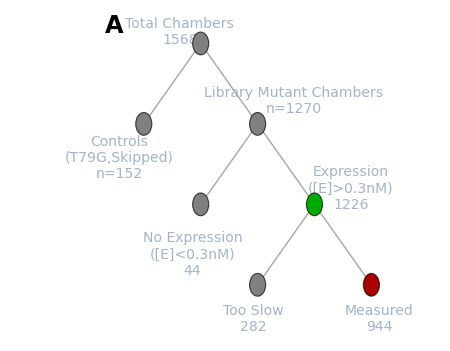

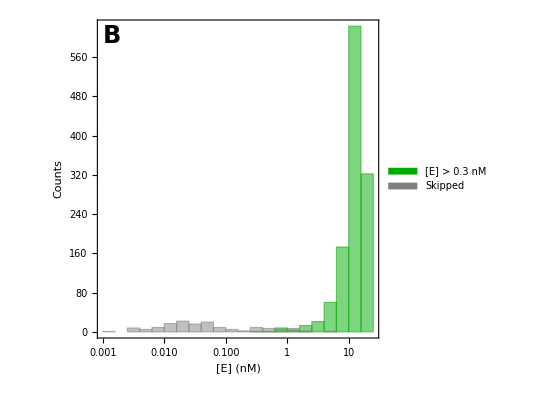

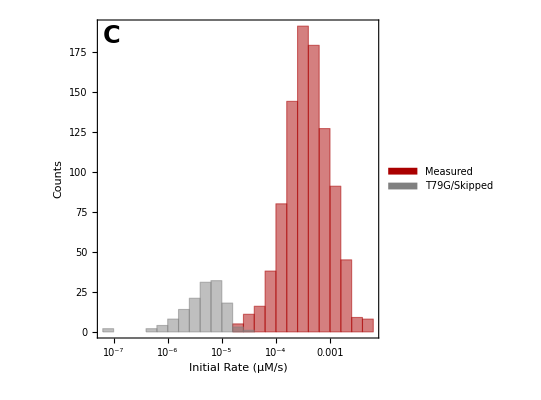

{{K162A,{6.9583,7.50136}},{K162A,{6.65369,8.77055}},{K162A,{6.05566,6.33548}},{K162A,{5.11865,5.73232}},{K162A,{6.25534,4.99954}}}

0.0464559

{{K162A,{6.9583,7.50136}},{K162A,{6.65369,8.77055}},{K162A,{6.05566,6.33548}},{K162A,{5.11865,5.73232}},{K162A,{6.25534,4.99954}}}

{{K162A,{149484.,152943.}},{K162A,{152046.,156603.}},{K162A,{155292.,151779.}},{K162A,{113431.,151940.}},{K162A,{143270.,141309.}}}

{{K162A,{46.5487,49.0468}},{K162A,{43.7611,56.0051}},{K162A,{38.9953,41.7415}},{K162A,{45.1256,37.7274}},{K162A,{43.6612,35.3803}}}

-Graphics- | -Graphics- | -Graphics-
-Graphics- |  | 
Experimental Summary. A) Counts of local limit of quantification control chambers (skipped and catalytically unresolvable mutants), library and known active site mutant chambers (library mutants), chambers which expressed >0.3 nM, and measured and chambers that were not sufficiently above the local limit of quantification (too slow). B) Distribution of enzyme concentrations in chambers with [E]>0.3 nM compared to the measured expression in the Skipped chambers. C) Distribution of rates measured in the chambers sufficiently above the local limit of quantification (Measured) compared to the rates measured in the control chambers, at the highest substrate concentration. D) Correlation between k_cat/K_M replicate measurements for measured library mutants. |  |

/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/temporary_PDF_0000.pdf

```mathematica
Dynamic[n]

start=AbsoluteTime[];

dataset=ds5[Select[#ExpIndex==1&&#AssayType==1&]];

Length[dataset]

Print["Fitting standard curves..."]
ProgressIndicator[Dynamic[count],{1,1568}]

addStandardCurveFits=Dataset@Table[Association[{"Indices"->Normal[dataset[count,"Indices"]],"StdCurveFitObject"->fitStdCurveNew[ToExpression[Normal[dataset[count,"SC_Concentrations"]]],If[NumberQ[ToExpression[Normal[dataset[count,"SC_Median_Chamber"]]][[1]]],ToExpression[Normal[dataset[count,"SC_Median_Chamber"]]],Missing[]]]}],{count,1,1568}];

addStandardCurveFits2=addStandardCurveFits[All,Append[#,{"StdCurveSlope"->If[MissingQ[#StdCurveFitObject],Missing["Nonexistent"],#StdCurveFitObject["BestFitParameters"][[2]]],"StdCurveIntercept"->If[MissingQ[#StdCurveFitObject],Missing["Nonexistent"],#StdCurveFitObject["BestFitParameters"][[1]]],"StdCurveRSquared"->If[MissingQ[#StdCurveFitObject],Missing["Nonexistent"],#StdCurveFitObject["RSquared"]]}]&];

withStdCurveFits=Dataset[JoinAcross[Normal[ds4],Normal[addStandardCurveFits2],{"Indices"},"Left"]];
Print["Adding standard curve plots..."]
ProgressIndicator[Dynamic[count2],{1,1568}]

withStdCurveFitsTemp=withStdCurveFits[Select[#ExpIndex==1&&#AssayType==1&]];

addStandardCurvePlots=Table[Association[{"Indices"->Normal[withStdCurveFitsTemp[count2,"Indices"]],"StandardCurvePlot"->makeStdCurvePlotNew[withStdCurveFitsTemp[count2,"StdCurveSlope"],withStdCurveFitsTemp[count2,"StdCurveIntercept"],ToExpression[withStdCurveFitsTemp[count2,"SC_Concentrations"]],ToExpression[withStdCurveFitsTemp[count2,"SC_Median_Chamber"]]]}],{count2,1,1568}];

AbsoluteTime[]-start

withStdCurvePlot=Dataset[JoinAcross[Normal[withStdCurveFits],addStandardCurvePlots,{"Indices"},"Left"]];

AbsoluteTime[]-start
withProgressCurves=withStdCurvePlot[All,Append[#,"TurnoverTimepoints(uM)"->convertTouM[ToExpression[#MedianIntensities],#StdCurveSlope,#StdCurveIntercept]]&];
cmupData=SemanticImport[cmupAggregatePath];
cmupParams=cmupData[All,{"MutantID","kcatNormMedian","KMMedian","kcat/KMNormMedianLimit","kcat/KMAggLimit"}];
cmupGrouped=cmupParams[GroupBy["MutantID"]];
wtkcatKm=cmupGrouped["WT",1,"kcat/KMNormMedianLimit"]
wtkcat=cmupGrouped["WT",1,"kcatNormMedian"]
wtKm=cmupGrouped["WT",1,"KMMedian"]
cmupParamsForCalc=Dataset[Table[Association[{"MutantID"->cmupGrouped[mutant,1,"MutantID"],"kcat"->If[cmupGrouped[mutant,1,"kcat/KMAggLimit"]==0,Select[Normal[cmupGrouped[mutant,All,"kcatNormMedian"]],NumberQ[#]&][[1]],Median[Select[Normal[cmupGrouped[mutant,All,"kcat/KMNormMedianLimit"]],#>0&]]/wtkcatKm*wtkcat],"Km"->If[cmupGrouped[mutant,1,"kcat/KMAggLimit"]==0,Select[Normal[cmupGrouped[mutant,All,"KMMedian"]],NumberQ[#]&][[1]],wtKm],"kobs"->Select[Normal[cmupGrouped[mutant,All,"kcat/KMNormMedianLimit"]],NumberQ[#]&][[1]],"Limit"->cmupGrouped[mutant,1,"kcat/KMAggLimit"]}],{mutant,1,Length[cmupGrouped]}]][GroupBy["MutantID"]]
obsProgressCurve[times_,concentrations_]:=Module[{temp1,fullProgressCurve},

If[MissingQ[concentrations],Missing[],

temp1={Normal[times],Normal[concentrations]};

fullProgressCurve=Sort[Table[{temp1[[1,n]],temp1[[2,n]]},{n,1,Length[temp1[[1]]]}],#1[[1]]<#2[[1]]&]]

]

progressCurveLambertW[kcat_?NumberQ,KM_,enz_,substrate_,time_]:=(substrate-KM*LambertW[substrate/KM*Exp[(substrate-kcat*enz*time)/KM]])

maxExponent=Round[Log[10,$MaxMachineNumber]]+1;

fitRateSuperposition[mutant_,progresscurve_,enzymeconc_,mecmupConc_]:=Module[{},

If[MissingQ[progresscurve],Table[Missing[],{7}],

chamberTestPC2=progresscurve;

econc=enzymeconc/1000.0;

cmupkcat=cmupParamsForCalc[mutant,1,"kcat"];
cmupKm=cmupParamsForCalc[mutant,1,"Km"];

limitQ=cmupParamsForCalc[mutant,1,"Limit"];

baseline=Min[chamberTestPC2[[All,2]]];

(* if we don't have measurements for kcat and Km then can't fit the superposition function - in these cases defaulting to a fit using the points at t>2500s *)
basicFit=LinearModelFit[Select[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],#[[1]]≥2500.0&],x,x];

basicFitRate=basicFit[[1,2,2]];

basicFitIntercept=basicFit[[1,2,1]];

pcBaselineCorrected=Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}];

p=Graphics[{EdgeForm[{Black,Thickness[0.125]}],FaceForm[Directive[GrayLevel[0.5],Opacity[0.7]]],Disk[],Opacity[0.1]}];

(* also modifying to fit only rates - the testing above is fitting the MecMUP kcat/KM *)

Which[NumberQ[cmupkcat]&&limitQ≠-1,

fit=Quiet[NMinimize[{Sum[((chamberTestPC2[[n,2]]-baseline)-(progressCurveLambertW[cmupkcat,cmupKm,econc,cmup,chamberTestPC2[[n,1]]]+(rate)*chamberTestPC2[[n,1]]))^2,{n,1,Length[chamberTestPC2]}],rate>-0.05&&rate<0.05&&cmup>0.0&&cmup<(mecmupConc/1000.0)},{cmup,rate}]];

lastFivePointsForFlag=Table[{chamberTestPC2[[n,1]],progressCurveLambertW[cmupkcat,cmupKm,econc,mecmupConc/1000.0,chamberTestPC2[[n,1]]]},{n,1,Length[chamberTestPC2]}];

flagFit=LinearModelFit[Select[lastFivePointsForFlag,#[[1]]≥2500.0&],x,x];

{fit[[2,1,2]],fit[[2,2,2]],Show[Plot[progressCurveLambertW[cmupkcat,cmupKm,econc,fit[[2,1,2]],t]+fit[[2,2,2]]*t,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.2,If[Max[chamberTestPC2[[All,2]]]>5.0,Max[chamberTestPC2[[All,2]]]+Abs[Max[chamberTestPC2[[All,2]]]]*0.5,5.5]},AspectRatio->0.8,PlotStyle->Gray],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotMarkers->{p,0.05}],Plot[progressCurveLambertW[cmupkcat,cmupKm,econc,fit[[2,1,2]],t],{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Directive[Gray,Dashed]],ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[18,Black,FontFamily->"Arial"],Epilog->Inset[mutant<>"\n"<>ToString[NumberForm[Round[fit[[2,2,2]],0.0000001],ScientificNotationThreshold->{-maxExponent,maxExponent}]]<>"μM/s"<>"\n[cMUP]="<>ToString[Round[fit[[2,1,2]],0.01]]<>" μM",Scaled[{0.80,0.3}]]],Abs[flagFit[[1,2,2]]],(fit[[2,2,2]]-trueBackgroundRate)/Abs[flagFit[[1,2,2]]],Show[Plot[progressCurveLambertW[cmupkcat,cmupKm,econc,fit[[2,1,2]],t]+fit[[2,2,2]]*t,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Darker[Red]],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotStyle->Directive[PointSize[0.02],Darker[Red],Opacity[0.5]]],PlotRange->All,AspectRatio->0.8,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[Black,18,FontFamily->"Arial"]],pcBaselineCorrected},

NumberQ[cmupkcat]&&limitQ==-1,

lastFivePointsForFlag=Table[{chamberTestPC2[[n,1]],progressCurveLambertW[cmupkcat,cmupKm,econc,mecmupConc/1000.0,chamberTestPC2[[n,1]]]},{n,1,Length[chamberTestPC2]}];

flagFit=LinearModelFit[Select[lastFivePointsForFlag,#[[1]]≥2500.0&],x,x];

{Missing[],basicFitRate,Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{If[(Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1)>0,0,Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1],If[Max[chamberTestPC2[[All,2]]]>5.0,Max[chamberTestPC2[[All,2]]]+Abs[Max[chamberTestPC2[[All,2]]]]*0.5,5.5]},AspectRatio->0.8,PlotStyle->Gray],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotMarkers->{p,0.05}],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[18,Black,FontFamily->"Arial"],Epilog->Inset[mutant<>"\n"<>ToString[NumberForm[Round[basicFitRate,0.0000001],ScientificNotationThreshold->{-maxExponent,maxExponent}]]<>"μM/s",Scaled[{0.80,0.2}]]],Abs[flagFit[[1,2,2]]],(fit[[2,2,2]]-trueBackgroundRate)/Abs[flagFit[[1,2,2]]],Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Darker[Red]],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotStyle->Directive[PointSize[0.02],Darker[Red],Opacity[0.5]]],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[Black,18,FontFamily->"Arial"]],pcBaselineCorrected},

NumberQ[cmupkcat]==False,

{Missing[],basicFitRate,Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{If[(Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1)>0,0,Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1],If[Max[chamberTestPC2[[All,2]]]>5.0,Max[chamberTestPC2[[All,2]]]+Abs[Max[chamberTestPC2[[All,2]]]]*0.5,5.5]},AspectRatio->0.8,PlotStyle->Gray],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotMarkers->{p,0.05}],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[18,Black,FontFamily->"Arial"],Epilog->Inset[mutant<>"\n"<>ToString[NumberForm[Round[basicFitRate,0.0000001],ScientificNotationThreshold->{-maxExponent,maxExponent}]]<>"μM/s",Scaled[{0.80,0.2}]]],Missing[],Missing[],Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Darker[Red]],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotStyle->Directive[PointSize[0.02],Darker[Red],Opacity[0.5]]],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[Black,18,FontFamily->"Arial"]],pcBaselineCorrected}


]]

]
withProgressCurves2=withProgressCurves[All,Append[#,{"ProgressCurve"->obsProgressCurve[ToExpression[#Times],#["TurnoverTimepoints(uM)"]],"EnzymeConc"->(#eGFPSummedI/#eGFPSlope)}]&];
itr=0;

Dynamic[itr]

optDataPoints2=withProgressCurves2[All,Append[#,itrNew=itr+1;itr=itrNew;out=Quiet[fitRateSuperposition[#MutantID,#ProgressCurve,#EnzymeConc,#SubstrateConc]];{"OptLinFitSlope"->out[[2]],"OptLinFitSlopeMinusTrueBackground"->out[[2]]-trueBackgroundRate,"ContaminantConc"->out[[1]],"FitPlot"->out[[3]],"ContaminantRate"->out[[4]],"ContaminantRatio"->out[[5]],"BackgroundFitPlot"->out[[6]],"ProgressCurveBaselineCorrected"->out[[7]]}]&];
indices=Normal[optDataPoints2[Select[#ExpIndex==1&]][All,"Indices"]];
Length[indices]
Dynamic[ind]

nearestLocalBG=Table[Association["Indices"->indices[[ind]],"NearestLocalBackgroundChambers"->findNearestBackgroundChambers[optDataPoints2,indices[[ind]]]],{ind,1,Length[indices]}];
(*nearestBackgroundChambers=Import["/Users/craig/Dropbox/HTMEK_processing/current/per-experiment_QC/nearestLocalBackgroundChambers.wxf"];*)

(*nearestBackgroundChambers=Import["/Users/craig/Dropbox/HTMEK_processing/current/per-experiment_QC/nearestLocalBackgroundChambers_SlowestChip.wxf"];*)

withNearestChambers=Dataset[JoinAcross[Normal[optDataPoints2],nearestLocalBG,"Indices","Left"]];
start=AbsoluteTime[];

count2=0;
Dynamic[count]

withPCs2=withNearestChambers[All,Quiet[Append[#,(Clear[forSelect];count=count2+1;forSelect=#NearestLocalBackgroundChambers;sconc=#SubstrateConc;
expIndex=#ExpIndex;
indices=#Indices;count2=count;

If[MissingQ[#ProgressCurve],"ProgressCurveOptFit2"->Missing[],

bgProgressCurves=Normal[optDataPoints2[Select[MemberQ[forSelect,#Indices]&&#ExpIndex==expIndex&]][All,"FitPlot"]];

{"ProgressCurveOptFit2"->If[Length[bgProgressCurves]>0,Show[DeleteCases[DeleteCases[{#FitPlot,Normal[optDataPoints2[Select[MemberQ[forSelect,#Indices]&&#SubstrateConc==sconc&&#ExpIndex==expIndex&]][All,"BackgroundFitPlot"]]},Missing["Nonexistent"],Infinity],Missing[],Infinity],AspectRatio->0.8,ImageSize->400,AspectRatio->0.6,ImagePadding->{{75,2},{60,8}},Epilog->Inset[Style[ToString[Round[sconc]]<>" μM",16,Black,FontFamily->"Arial"],Scaled[{0.18,0.85}]]],Missing["Nonexistent"]]}]

)]&]];


(*{"ProgressCurveOptFit2"->If[Length[bgProgressCurves]>0,Show[DeleteCases[DeleteCases[{#FitPlot,Normal[optDataPoints2[Select[MemberQ[forSelect,#Indices]&&#SubstrateConc==sconc&&#ExpIndex==expIndex&]][All,"BackgroundFitPlot"]]},Missing["Nonexistent"],Infinity],Missing[]],AspectRatio->0.8,ImageSize->400,AspectRatio->0.6,ImagePadding->{{75,2},{60,8}},Epilog->Inset[Style[ToString[Round[sconc]]<>" μM",16,Black,FontFamily->"Arial"],Scaled[{0.18,0.85}]]],Missing["Nonexistent"]]}*)

AbsoluteTime[]-start
Dynamic[n]
Dynamic[column]

(*datasetIN=withPCs;*)

datasetIN=withPCs2;

inhibitorconcentrations=Normal[datasetIN[Select[#Indices=={1,1}&],"InhibitorConcentrations"]];
substrateconcentrations=Normal[datasetIN[Select[#Indices=={1,1}&],"SubstrateConc"]]
type=Normal[datasetIN[Select[#Indices=={1,1}&],"AssayType"]];

exptIndices=Normal[datasetIN[Select[#Indices=={1,1}&],"ExpIndex"]];

dataset2=datasetIN;

start=AbsoluteTime[];

interpolations=Flatten[Table[Association[{"x"->column,"ExpIndex"->exptIndices[[n]],"AssayType"->type[[n]],"Interpolation"->interpolateDeadMutantsPerColumn[mutantList,exptIndices[[n]],column,dataset2,"OptLinFitSlopeMinusTrueBackground"],"MutantsUsedForLocalBG"->mutantList}],{n,1,Length[substrateconcentrations]},{column,1,28}],1];

dataset3=Dataset[JoinAcross[Normal[dataset2],interpolations,{"x","ExpIndex","AssayType"},"Left"]];

AbsoluteTime[]-start
start=AbsoluteTime[];

dataset=dataset3;

temp=Values[Normal[dataset[All,{"Indices","ExpIndex","OptLinFitSlopeMinusTrueBackground","MutantID","Interpolation"}]]];

localBGs=Table[Association[{"Indices"->temp[[n,1]],"ExpIndex"->temp[[n,2]],"LocalBackgroundRatio"->If[MissingQ[temp[[n,3]]],Missing["Nonexistent"],(temp[[n,3]])/(temp[[n,5,temp[[n,1,2]]]])]}],{n,1,Length[temp]}];

withlocalBG=Dataset[JoinAcross[Normal[dataset],localBGs,{"Indices","ExpIndex"},"Left"]];

AbsoluteTime[]-start

Dynamic[n]

scaleEachAssay=0;

eGFPslope=withlocalBG[1,"eGFPSlope"];

start=AbsoluteTime[];

dataset2=withlocalBG;


boundingMutants={"WT","T79S"};

rateKey="OptLinFitSlopeMinusTrueBackground";

temp=dataset2[Select[#ExpIndex==whichExpt&],{"Indices","ExpIndex",rateKey,"MutantID","Interpolation"}];

upperBound=Mean[Select[Values[Normal[dataset2[Select[#MutantID==boundingMutants[[1]]&&#ExpIndex==whichExpt&&#eGFPSummedI>EcutoffForBG*eGFPslope&],{rateKey}]]],NumberQ[#[[1]]]==True&]][[1]];

lowerBound=Mean[Select[Values[Normal[dataset2[Select[#MutantID==boundingMutants[[2]]&&#ExpIndex==whichExpt&&#eGFPSummedI>EcutoffForBG*eGFPslope&],{rateKey}]]],NumberQ[#[[1]]]==True&]][[1]];

allinColumn=Join@@Flatten[Table[AssociationThread[Table[{column,row},{row,1,56}],Sort[Values[Normal[dataset2[Select[#Indices[[1]]==column&&#ExpIndex==whichExpt&],{"Indices",rateKey,"MutantID"}]]],#1[[1,2]]<#2[[1,2]]&]],{column,1,28}],2];

temp2=temp[All,Append[#,{"Indices"->Normal[#[[1]]],"MaxLocalBackgroundPlot"->generateLocalBGPlot[Normal[#["Indices"]],Normal[#["ExpIndex"]],Normal[#["Interpolation"]]]}]&];

withlocalBGPlots=Dataset[JoinAcross[Normal[dataset2],Normal[temp2],{"Indices"},"Left"]];

CloseKernels[];

LaunchKernels[4];

dataset=withlocalBGPlots;

len=1568;

numKernels=Length[Kernels[]]

chunksize=Round[len/numKernels];
firstChunks =Table[{(chunksize*(n-1))+1, n*chunksize}, {n, numKernels-1}];
intervals=Append[firstChunks, {(chunksize*(numKernels-1))+1, len}];

toCalculate=dataset[GroupBy["Indices"]];

chunked = toCalculate[[#[[1]];;#[[2]]]]&/@intervals;

flattened=Table[chunked[[n]][Catenate],{n,1,Length[chunked]}];

addedMMcalc=Join@@ParallelMap[Quiet[fitMichaelisMenten[#,"OptLinFitSlopeMinusTrueBackground","optlin",eGFPslope,scaleEachAssay]]&,flattened];

AbsoluteTime[]-start

CloseKernels[]
Dynamic[n]

grouped=addedMMcalc[GroupBy["Indices"]];

indicesOut=Values[#]&/@Values[Normal[grouped[All,1,{"MutantID","Indices","fit_mm_kcat","fit_mm_KM"}]]];

addkcatoverkm=Table[Association[{"MutantID"->indicesOut[[n,1]],"Indices"->indicesOut[[n,2]],"fit_mm_kcatoverKM_MMfit"->If[MissingQ[indicesOut[[n,3]]],Missing["Nonexistent"],indicesOut[[n,3]]/(indicesOut[[n,4]]*10^-6)]}],{n,1,1568}];

addedkcatoverkm=Dataset[JoinAcross[Normal[addedMMcalc],addkcatoverkm,"Indices","Left"]]//Quiet;


grouped=addedkcatoverkm[GroupBy["Indices"]];

indicesOut=Values[#]&/@Values[Normal[grouped[All,1,{"MutantID","Indices"}]]];

pGFP=Graphics[{EdgeForm[{Black,Thickness[0.125]}],FaceForm[Directive[Darker[Green],Opacity[0.7]]],Disk[],Opacity[0.1]}];

addedeGFPIntensityPlot=Table[Association[{"MutantID"->indicesOut[[n,1]],"Indices"->indicesOut[[n,2]],"eGFPIntensityPlot"->If[egfpSameFlag==0,ListPlot[Normal[grouped[n,All,"eGFPSummedI"]]/10^6,PlotRange->{0,Max[Normal[grouped[n,All,"eGFPSummedI"]]/10^6]*1.5},Frame->True,Axes->False,PlotMarkers->{pGFP,0.05},FrameStyle->Directive[20,Black,FontFamily->"Arial"],FrameLabel->{"Assay Number","eGFP Intensity (×10^6)"},ImagePadding->{{75,2},{65,5}},AspectRatio->0.8,ImageSize->400],ListPlot[{{1,Normal[grouped[n,1,"eGFPSummedI"]]/10^6}},PlotRange->{{0,Length[Normal[grouped[n,All,"eGFPSummedI"]]]},{0,Max[Normal[grouped[n,All,"eGFPSummedI"]]/10^6]*1.5}},Frame->True,Axes->False,PlotMarkers->{pGFP,0.05},GridLines->{None,{Normal[grouped[n,1,"eGFPSummedI"]]/10^6}},GridLinesStyle->Directive[Dashed,Darker[Green]],FrameStyle->Directive[20,Black,FontFamily->"Arial"],FrameLabel->{"Assay Number","eGFP Intensity (×10^6)"},ImagePadding->{{75,2},{65,5}},AspectRatio->0.8,ImageSize->400,FrameTicks->{{If[IntegerQ[#],#,N[#]]&/@FindDivisions[{0,Max[Normal[grouped[n,All,"eGFPSummedI"]]/10^6]},5],None},{If[IntegerQ[#],#,N[#]]&/@FindDivisions[{0,Length[Normal[grouped[n,All,"eGFPSummedI"]]]},Round[Length[Normal[grouped[n,All,"eGFPSummedI"]]]/2]],None}},Epilog->Inset[Style["eGFP measured\nbefore 1st assay only",14,Darker[Green]],Scaled[{0.7,0.3}]]]]}],{n,1,1568}];

addedeGFPIntensityPlotDataset=Dataset[JoinAcross[JoinAcross[Normal[addedkcatoverkm],addedeGFPIntensityPlot,"Indices","Left"],Normal[wxfForImageStamps[Select[#ExpIndex==1&],{"Indices","eGFPPostSDSImage"}]],"Indices","Left"]]//Quiet;

AbsoluteTime[]-start
normalizedDataset=Normal[addedeGFPIntensityPlotDataset];

replaced=Fold[Replace[#1,#2,Infinity]&,normalizedDataset,{_FittedModel->"NaN",_Graphics->"NaN",_Image->"NaN",_NonlinearModelFit->"NaN",_Times->"NaN",_Overlay->"NaN",_ReplaceAll->"NaN"}];

headers=Keys[replaced[[1]]];

(*values=Map[replaceBracketsBack,Values[replaced],{2}];*)

values=Values[replaced];

datasetForExport=Prepend[values,headers];

Export[StringJoin["~/Desktop/",addedkcatoverkm[1,"GlobalExperimentIndex"],"_MecMUP_LinComb.csv.bz2"],datasetForExport,"Data"];

(* summary table *)

fixLogPlots[gr_]:=gr/.f:(Charting`ScaledTicks|Charting`ScaledFrameTicks)[{Log,Exp}]:>(Part[#,;;, ;;3]&@*f);

p2=Graphics[{EdgeForm[{Black,Thickness[0.125]}],FaceForm[Directive[Gray,Opacity[0.7]]],Disk[],Opacity[0.1]}];

expressed=addedeGFPIntensityPlotDataset[Select[#ExpIndex==1&&#ManualGFPFlag==0&&#EnzymeConc>0.3&]];

Length[expressed]

skipped=addedeGFPIntensityPlotDataset[Select[#ExpIndex==1&&#ManualGFPFlag==0&&#MutantID=="Skipped"&]];

allLibraryChambers=addedeGFPIntensityPlotDataset[Select[#ExpIndex==1&&#MutantID≠"Skipped"&&#MutantID≠"T79G"&]];

expressedLibrary=allLibraryChambers[Select[#EnzymeConc>0.3&&#ManualGFPFlag==0&]];

Length[allLibraryChambers]
Length[expressedLibrary]

tooSlow=addedeGFPIntensityPlotDataset[Select[#ExpIndex==whichExpt&&#LocalBackgroundRatio≤5.0&&MemberQ[Normal[expressedLibrary[All,"Indices"]],#Indices]&]];

Length[tooSlow]

measured=addedeGFPIntensityPlotDataset[Select[#ExpIndex==whichExpt&&#LocalBackgroundRatio>5.0&&MemberQ[Normal[expressedLibrary[All,"Indices"]],#Indices]&]];

Length[measured]

countTree=TreePlot[{1->2,1->3,3->4,3->5,5->6,5->7},VertexSize->Medium,VertexCoordinates->{{0,0},{-1,-1},{1,-1},{0,-2},{2,-2},{1,-3},{3,-3}},EdgeStyle->Gray,Epilog->Inset[Style["A",24,Bold],Scaled[{0.0,1.0}]],VertexLabels->{1->Placed[Style["Total Chambers\n1568",14],{-0.8,1}],2->Placed[Style["Controls\n(T79G,Skipped)\nStyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[skipped]],14],{-1,-1}],3->Placed[Style["Library Mutant Chambers\nStyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[allLibraryChambers]],14],{2.75,1.5}],4->Placed[Style["No Expression\n([E]<0.3nM)\n"<>ToString[Length[allLibraryChambers]-Length[expressedLibrary]],14],{0,-1.7}],5->Placed[Style["Expression\n([E]>0.3nM)\n"<>ToString[Length[expressedLibrary]],14],{2.75,1.2}],7->Placed[Style["Measured\n"<>ToString[Length[measured]],14],{1,-1}],6->Placed[Style["Too Slow\n"<>ToString[Length[tooSlow]],14],{0.25,-1}]},ImageSize->450,VertexStyle->
Join[
{1->Gray}, 
#->Gray&/@{1,2,3,4,6},
#->Darker[Green]&/@{5},
#->Darker[Red]&/@{7}
]]

eConcHist=fixLogPlots@Histogram[{Normal[expressedLibrary[All,"EnzymeConc"]],Normal[skipped[All,"EnzymeConc"]]},"Log",ChartStyle->{Darker[Green],Gray},Frame->True,Axes->False,PlotRange->All,FrameStyle->Directive[20,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->400,FrameLabel->{Style["[E] (nM)",SingleLetterItalics->False],Style["Counts",SingleLetterItalics->False]},Epilog->{Inset[SwatchLegend[{Darker[Green],Gray},Style[#,16]&/@{"[E] > 0.3 nM","Skipped"}],Scaled[{0.25,0.9}]],Inset[Style["B",24,Bold],Scaled[{0.05,0.95}]]}]

rateHist=fixLogPlots@Histogram[{Normal[measured[All,"OptLinFitSlopeMinusTrueBackground"]],Normal[skipped[All,"OptLinFitSlopeMinusTrueBackground"]]},"Log",ChartStyle->{Darker[Red],Gray},Frame->True,Axes->False,PlotRange->All,FrameStyle->Directive[20,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->400,FrameLabel->{Style["Initial Rate (μM/s)",SingleLetterItalics->False],Style["Counts",SingleLetterItalics->False]},Epilog->{Inset[SwatchLegend[{Darker[Red],Gray},Style[#,16]&/@{"Measured","T79G/Skipped"}],Scaled[{0.8,0.9}]],Inset[Style["C",24,Bold],Scaled[{0.05,0.95}]]}]

measured2=measured;

measured3=measured2[All,{"MutantID","fit_mm_kcat"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured3[n,1,"MutantID"],#}&/@Partition[Normal[measured3[n,All,"fit_mm_kcat"]],2],{n,1,Length[measured3]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]]

measured2=measured[All,{"MutantID","fit_mm_kcat","fit_mm_KM","fit_mm_kcatoverKM_MMfit"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured2[n,1,"MutantID"],#}&/@Partition[Normal[measured2[n,All,"fit_mm_kcat"]],2],{n,1,Length[measured2]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]];

rmse=Sqrt[Mean[Table[(Log[10,pairs[[n,2,1]]]-Log[10,pairs[[n,2,2]]])^2,{n,1,Length[pairs]}]]];

pearsonR2=Correlation[Log[10,pairs[[All,2,1]]],Log[10,pairs[[All,2,2]]]]^2;

(*kcatplot=fixLogPlots@Show[ListLogLogPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[pairs[[n,2]],pairs[[n,1]]],pairs[[n,2]]],{n,1,Length[pairs]}],PlotRange->{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}},Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->500,PlotMarkers->{p2,0.02},FrameLabel->{"SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"] (rep.1) (/s)","SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"] (rep.2) (/s)"}],LogLogPlot[{x,x/2,x*2},{x,0.0001,10000},PlotStyle->Directive[Gray,Dashed]],ImagePadding->100];*)

kcatplot=Show[ListPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[Log[10,pairs[[n,2]]],pairs[[n,1]]],Log[10,pairs[[n,2]]]],{n,1,Length[pairs]}],PlotRange->Log[10,{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}}],Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->475,PlotMarkers->{p2,0.02},FrameLabel->{"Log10(SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]) (rep.1) (/s)","Log10(SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]) (rep.2) (/s)"},Epilog->{Inset[Style["SuperscriptBox[StyleBox[\"R\",FontSlant->\"Italic\"], \"2\"]="<>ToString[Round[pearsonR2,0.01]],14],Scaled[{0.2,0.9}]],Inset[Style["RMSE="<>ToString[Round[rmse,0.01]],14],Scaled[{0.2,0.8}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[pairs]],14],Scaled[{0.2,0.7}]],Inset[Style["D",24,Bold],Scaled[{0.05,0.95}]]}],Plot[{x,x-0.301,x+0.301},{x,-5,10},PlotStyle->Directive[Gray,Dashed]],ImagePadding->{{100,20},{100,50}}];

measured2=measured[All,{"MutantID","fit_mm_KM"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured2[n,1,"MutantID"],#}&/@Partition[Normal[measured2[n,All,"fit_mm_KM"]],2],{n,1,Length[measured2]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]];

rmse=Sqrt[Mean[Table[(Log[10,pairs[[n,2,1]]]-Log[10,pairs[[n,2,2]]])^2,{n,1,Length[pairs]}]]];

pearsonR2=Correlation[Log[10,pairs[[All,2,1]]],Log[10,pairs[[All,2,2]]]]^2;

KmPlot=Show[ListPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[Log[10,pairs[[n,2]]],pairs[[n,1]]],Log[10,pairs[[n,2]]]],{n,1,Length[pairs]}],PlotRange->Log[10,{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}}],Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->475,PlotMarkers->{p2,0.02},FrameLabel->{Style["Log[10,SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.1) (/s)",SingleLetterItalics->False],Style["Log[10,SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.2) (/s)",SingleLetterItalics->False]},Epilog->{Inset[Style["SuperscriptBox[StyleBox[\"R\",FontSlant->\"Italic\"], \"2\"]="<>ToString[Round[pearsonR2,0.01]],14],Scaled[{0.2,0.9}]],Inset[Style["RMSE="<>ToString[Round[rmse,0.01]],14],Scaled[{0.2,0.8}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[pairs]],14],Scaled[{0.2,0.7}]],Inset[Style["E",24,Bold],Scaled[{0.05,0.95}]]}],Plot[{x,x-0.301,x+0.301},{x,-5,10},PlotStyle->Directive[Gray,Dashed]],Plot[10,{x,-5,Log[10,0.5]},Filling->-5,FillingStyle->Directive[LightPink,Opacity[0.5]],PlotStyle->Directive[LightPink,Opacity[0.8]]],ImagePadding->{{100,20},{100,50}}];

measured2=measured[All,{"MutantID","fit_mm_kcatoverKM_MMfit"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured2[n,1,"MutantID"],#}&/@Partition[Normal[measured2[n,All,"fit_mm_kcatoverKM_MMfit"]],2],{n,1,Length[measured2]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]];

rmse=Sqrt[Mean[Table[(Log[10,pairs[[n,2,1]]]-Log[10,pairs[[n,2,2]]])^2,{n,1,Length[pairs]}]]];

pearsonR2=Correlation[Log[10,pairs[[All,2,1]]],Log[10,pairs[[All,2,2]]]]^2;

kcatKMplot=Show[ListPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[Log[10,pairs[[n,2]]],pairs[[n,1]]],Log[10,pairs[[n,2]]]],{n,1,Length[pairs]}],PlotRange->Log[10,{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}}],Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->475,PlotMarkers->{p2,0.02},FrameLabel->{Style["Log[10,SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]/SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.1) (/M /s)",SingleLetterItalics->False],Style["Log[10,SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]/SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.2) (/M /s)",SingleLetterItalics->False]},Epilog->{Inset[Style["SuperscriptBox[StyleBox[\"R\",FontSlant->\"Italic\"], \"2\"]="<>ToString[Round[pearsonR2,0.01]],14],Scaled[{0.2,0.9}]],Inset[Style["RMSE="<>ToString[Round[rmse,0.01]],14],Scaled[{0.2,0.8}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[pairs]],14],Scaled[{0.2,0.7}]],Inset[Style["F",24,Bold],Scaled[{0.05,0.95}]]}],Plot[{x,x-0.301,x+0.301},{x,-5,10},PlotStyle->Directive[Gray,Dashed]],ImagePadding->{{100,20},{100,50}}];

(*Grid[{{countTree,kcatplot},{eConcHist,KmPlot},{rateHist,kcatKMplot}}]*)

summaryGrid=Grid[{{countTree,eConcHist,rateHist},{kcatKMplot},{Style["Experimental Summary. A) Counts of local limit of quantification control chambers (skipped and catalytically unresolvable mutants), library and known active site mutant chambers (library mutants), chambers which expressed >0.3 nM, and measured and chambers that were not sufficiently above the local limit of quantification (too slow). B) Distribution of enzyme concentrations in chambers with [E]>0.3 nM compared to the measured expression in the Skipped chambers. C) Distribution of rates measured in the chambers sufficiently above the local limit of quantification (Measured) compared to the rates measured in the control chambers, at the highest substrate concentration. D) Correlation between SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]/SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"] replicate measurements for measured library mutants.",18,FontFamily->"Arial",TextAlignment->Left,SingleLetterItalics->False],SpanFromLeft}}]

Export[StringJoin["/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/temporary_PDF_","0000",".pdf"],summaryGrid,"AllowRasterization"->False]
```

```mathematica
dataset=addedeGFPIntensityPlotDataset;

indices=Sort[Normal[DeleteDuplicates[dataset[[All,"Indices"]]]]];

Do[

(* change 3rd argument to correspond to type of assay: cMUP, MeP, MecMUP, Inhibition *)
(* added 4th argument "unscaled" *)
out=makeGridMecMUP[dataset,indices[[n]],"MecMUP","unscaled"];

Export[StringJoin["/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/temporary_PDF_",StringPadLeft[ToString[n],4,"0"],".pdf"],out,"AllowRasterization"->False];

,{n,1,1568}];

out;

session = StartExternalSession[<|"System"->"Python","Version"->"3.6", "SessionProlog"->{"import os", "from PyPDF2 import PdfFileMerger, PdfFileReader"}|>];

defineRoot = "root='/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/'";
getNames = "pdfs1=[os.path.join(root, dir) for dir in os.listdir(root) if '.pdf' in dir]";
getNames2="pdfs=sorted(pdfs1)";
createMerger = "merger = PdfFileMerger()";
executeMerge = "for pdf in pdfs: merger.append(PdfFileReader(pdf,'rb'))";
executeExport = StringJoin["merger.write('/Users/craig/Desktop/",Values[Normal[dataset[1,{"GlobalExperimentIndex"}]]][[1]],".pdf')"];
completionNotice = "print('PDF Concatenation Complete')";

ExternalEvaluate[session,{defineRoot, getNames,getNames2, createMerger, executeMerge, executeExport, completionNotice}];
```

PDF Concatenation Complete

```mathematica
Length[dataset]
```

6272

#### Dataset 2:

```mathematica
dataset=remapNames[generateDatasetFromCSV[Import["/Users/craig/Dropbox/HTMEK_processing/MecMUP_QC_200220/180528_S2_d2_MecMUP_1_MecMUP_LinComb.csv.bz2"],"GlyScan","180528_S2_d2_MecMUP_1_MecMUP_LinComb"]];

wxfForImageStamps=Import["/Users/craig/Desktop/180528_S2_d2_MecMUP_1_newLBR.wxf"]

dataset[1;;2]
```

Dataset[<>]

```mathematica
keysToKeep={"GlobalExperimentIndex","Date","Experiment","Setup","Device","PhosphateSensorConc","eGFPSlope","x","y","median_chamber","sum_chamber","std_chamber","x_center_chamber","y_center_chamber","radius_chamber","xslice","yslice","MutantID","time_s","median_button_Button_Quant","summed_button_Button_Quant","eGFPSummedI","std_button_Button_Quant","x_button_center_Button_Quant","y_button_center_Button_Quant","radius_button_disk_Button_Quant","median_button_annulus_Button_Quant","summed_button_annulus_normed_Button_Quant","std_button_annulus_localBG_Button_Quant","inner_radius_button_annulus_Button_Quant","outer_radius_button_annulus_Button_Quant","xslice_Button_Quant","yslice_Button_Quant","MutantID_Button_Quant","series_index","Times","MedianIntensities","ExpIndex","AssayType","SubstrateConc","InhibitorConcentrations","Zn2+","SC_Concentrations","SC_Median_Chamber","SC_Median_Chamber","ManualGFPFlag","Indices"};
ds2=dataset[All,Append[#,{"Indices2"->ToExpression[#Indices]}]&];

ds3=ds2[All,{"GlobalExperimentIndex","Date","Experiment","Setup","Device","PhosphateSensorConc","eGFPSlope","x","y","median_chamber","sum_chamber","std_chamber","x_center_chamber","y_center_chamber","radius_chamber","xslice","yslice","MutantID","time_s","median_button_Button_Quant","summed_button_Button_Quant","eGFPSummedI","std_button_Button_Quant","x_button_center_Button_Quant","y_button_center_Button_Quant","radius_button_disk_Button_Quant","median_button_annulus_Button_Quant","summed_button_annulus_normed_Button_Quant","std_button_annulus_localBG_Button_Quant","inner_radius_button_annulus_Button_Quant","outer_radius_button_annulus_Button_Quant","xslice_Button_Quant","yslice_Button_Quant","MutantID_Button_Quant","series_index","Times","MedianIntensities","ExpIndex","AssayType","SubstrateConc","InhibitorConcentrations","Zn2+","SC_Concentrations","SC_Median_Chamber","SC_Median_Chamber","ManualGFPFlag","Indices2"}];

ds4=ds3[All,Append[#,"Indices"->#Indices2]&][All,keysToKeep];

ds4[GroupBy["Indices"]][1;;2,All,"eGFPSummedI"]
ds4[GroupBy["Indices"]][1;;2,All,"SubstrateConc"]
egfpSameFlag=0;
ds5=ds4[All,Append[#,"eGFPConstant"->egfpSameFlag]&];
```

```mathematica
mutantList={"T79G","Skipped"};

whichExpt=3;

EcutoffForBG=0.3;

trueBackgroundRate=-2.3 10^-6;
```

1568

Fitting standard curves...

Adding standard curve plots...

54.204464

55.050621

1.4213×10^6

121.236

85.3261

Dataset[<>]

General::readp: Symbol None is read-protected.

General::stop: Further output of General::readp will be suppressed during this calculation.

1568

General::readp: Symbol None is read-protected.

General::stop: Further output of General::readp will be suppressed during this calculation.

168.04978

{500.,1000.,1500.}

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

20.30026

14.73189

4

288.866

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

391.916532

1225

1400

1106

222

884

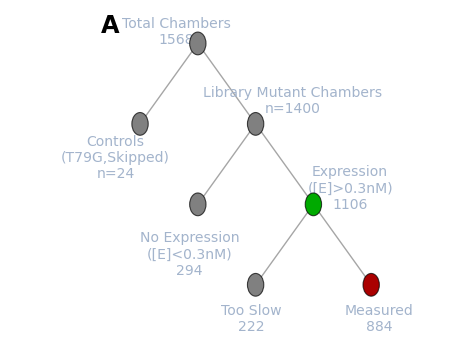

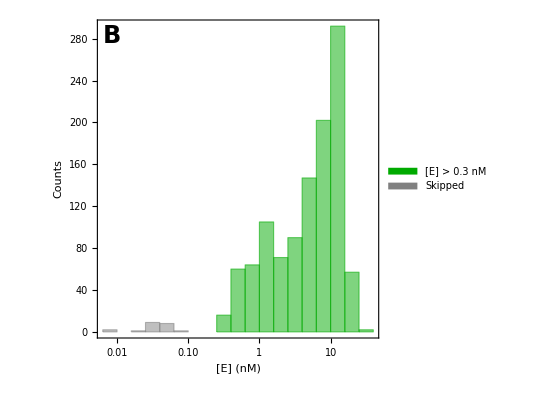

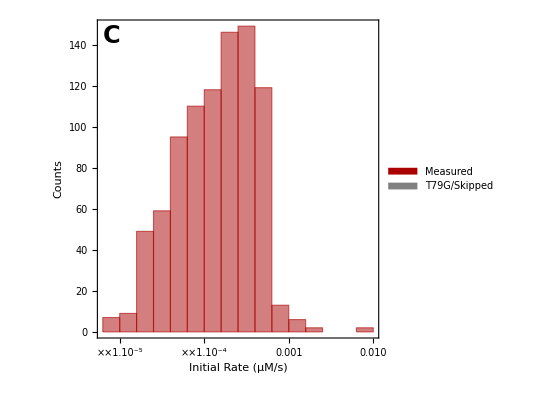

{{H353E,{0.120495,0.125714}},{S315V,{0.382073,0.791017}},{K366V,{1.21512,3.07059}},{G483V,{0.340281,1.28519}},{D73V,{0.662613,0.585975}}}

8.10106×10^-9

{{H353E,{0.120495,0.125714}},{S315V,{0.382073,0.791017}},{K366V,{1.21512,3.07059}},{G483V,{0.340281,1.28519}},{D73V,{0.662613,0.585975}}}

{{H353E,{164672.,179064.}},{S315V,{83355.4,247398.}},{K366V,{125294.,213393.}},{G483V,{66031.1,299525.}},{D73V,{162600.,192176.}}}

{{H353E,{0.731732,0.702063}},{S315V,{4.58366,3.19734}},{K366V,{9.69821,14.3894}},{G483V,{5.15335,4.29075}},{D73V,{4.07512,3.04915}}}

-Graphics- | -Graphics- | -Graphics-
-Graphics- |  | 
Experimental Summary. A) Counts of local limit of quantification control chambers (skipped and catalytically unresolvable mutants), library and known active site mutant chambers (library mutants), chambers which expressed >0.3 nM, and measured and chambers that were not sufficiently above the local limit of quantification (too slow). B) Distribution of enzyme concentrations in chambers with [E]>0.3 nM compared to the measured expression in the Skipped chambers. C) Distribution of rates measured in the chambers sufficiently above the local limit of quantification (Measured) compared to the rates measured in the control chambers, at the highest substrate concentration. D) Correlation between k_cat/K_M replicate measurements for measured library mutants. |  |

/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/temporary_PDF_0000.pdf

```mathematica
Dynamic[n]

start=AbsoluteTime[];

dataset=ds5[Select[#ExpIndex==1&&#AssayType==1&]];

Length[dataset]

Print["Fitting standard curves..."]
ProgressIndicator[Dynamic[count],{1,1568}]

addStandardCurveFits=Dataset@Table[Association[{"Indices"->Normal[dataset[count,"Indices"]],"StdCurveFitObject"->fitStdCurveNew[ToExpression[Normal[dataset[count,"SC_Concentrations"]]],If[NumberQ[ToExpression[Normal[dataset[count,"SC_Median_Chamber"]]][[1]]],ToExpression[Normal[dataset[count,"SC_Median_Chamber"]]],Missing[]]]}],{count,1,1568}];

addStandardCurveFits2=addStandardCurveFits[All,Append[#,{"StdCurveSlope"->If[MissingQ[#StdCurveFitObject],Missing["Nonexistent"],#StdCurveFitObject["BestFitParameters"][[2]]],"StdCurveIntercept"->If[MissingQ[#StdCurveFitObject],Missing["Nonexistent"],#StdCurveFitObject["BestFitParameters"][[1]]],"StdCurveRSquared"->If[MissingQ[#StdCurveFitObject],Missing["Nonexistent"],#StdCurveFitObject["RSquared"]]}]&];

withStdCurveFits=Dataset[JoinAcross[Normal[ds4],Normal[addStandardCurveFits2],{"Indices"},"Left"]];
Print["Adding standard curve plots..."]
ProgressIndicator[Dynamic[count2],{1,1568}]

withStdCurveFitsTemp=withStdCurveFits[Select[#ExpIndex==1&&#AssayType==1&]];

addStandardCurvePlots=Table[Association[{"Indices"->Normal[withStdCurveFitsTemp[count2,"Indices"]],"StandardCurvePlot"->makeStdCurvePlotNew[withStdCurveFitsTemp[count2,"StdCurveSlope"],withStdCurveFitsTemp[count2,"StdCurveIntercept"],ToExpression[withStdCurveFitsTemp[count2,"SC_Concentrations"]],ToExpression[withStdCurveFitsTemp[count2,"SC_Median_Chamber"]]]}],{count2,1,1568}];

AbsoluteTime[]-start

withStdCurvePlot=Dataset[JoinAcross[Normal[withStdCurveFits],addStandardCurvePlots,{"Indices"},"Left"]];

AbsoluteTime[]-start
withProgressCurves=withStdCurvePlot[All,Append[#,"TurnoverTimepoints(uM)"->convertTouM[ToExpression[#MedianIntensities],#StdCurveSlope,#StdCurveIntercept]]&];
cmupData=SemanticImport[cmupAggregatePath];
cmupParams=cmupData[All,{"MutantID","kcatNormMedian","KMMedian","kcat/KMNormMedianLimit","kcat/KMAggLimit"}];
cmupGrouped=cmupParams[GroupBy["MutantID"]];
wtkcatKm=cmupGrouped["WT",1,"kcat/KMNormMedianLimit"]
wtkcat=cmupGrouped["WT",1,"kcatNormMedian"]
wtKm=cmupGrouped["WT",1,"KMMedian"]
cmupParamsForCalc=Dataset[Table[Association[{"MutantID"->cmupGrouped[mutant,1,"MutantID"],"kcat"->If[cmupGrouped[mutant,1,"kcat/KMAggLimit"]==0,Select[Normal[cmupGrouped[mutant,All,"kcatNormMedian"]],NumberQ[#]&][[1]],Median[Select[Normal[cmupGrouped[mutant,All,"kcat/KMNormMedianLimit"]],#>0&]]/wtkcatKm*wtkcat],"Km"->If[cmupGrouped[mutant,1,"kcat/KMAggLimit"]==0,Select[Normal[cmupGrouped[mutant,All,"KMMedian"]],NumberQ[#]&][[1]],wtKm],"kobs"->Select[Normal[cmupGrouped[mutant,All,"kcat/KMNormMedianLimit"]],NumberQ[#]&][[1]],"Limit"->cmupGrouped[mutant,1,"kcat/KMAggLimit"]}],{mutant,1,Length[cmupGrouped]}]][GroupBy["MutantID"]]
obsProgressCurve[times_,concentrations_]:=Module[{temp1,fullProgressCurve},

If[MissingQ[concentrations],Missing[],

temp1={Normal[times],Normal[concentrations]};

fullProgressCurve=Sort[Table[{temp1[[1,n]],temp1[[2,n]]},{n,1,Length[temp1[[1]]]}],#1[[1]]<#2[[1]]&]]

]

progressCurveLambertW[kcat_?NumberQ,KM_,enz_,substrate_,time_]:=(substrate-KM*LambertW[substrate/KM*Exp[(substrate-kcat*enz*time)/KM]])

maxExponent=Round[Log[10,$MaxMachineNumber]]+1;

fitRateSuperposition[mutant_,progresscurve_,enzymeconc_,mecmupConc_]:=Module[{},

If[MissingQ[progresscurve],Table[Missing[],{7}],

chamberTestPC2=progresscurve;

econc=enzymeconc/1000.0;

cmupkcat=cmupParamsForCalc[mutant,1,"kcat"];
cmupKm=cmupParamsForCalc[mutant,1,"Km"];

limitQ=cmupParamsForCalc[mutant,1,"Limit"];

baseline=Min[chamberTestPC2[[All,2]]];

(* if we don't have measurements for kcat and Km then can't fit the superposition function - in these cases defaulting to a fit using the points at t>2500s *)
basicFit=LinearModelFit[Select[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],#[[1]]≥2500.0&],x,x];

basicFitRate=basicFit[[1,2,2]];

basicFitIntercept=basicFit[[1,2,1]];

pcBaselineCorrected=Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}];

p=Graphics[{EdgeForm[{Black,Thickness[0.125]}],FaceForm[Directive[GrayLevel[0.5],Opacity[0.7]]],Disk[],Opacity[0.1]}];

(* also modifying to fit only rates - the testing above is fitting the MecMUP kcat/KM *)

Which[NumberQ[cmupkcat]&&limitQ≠-1,

fit=Quiet[NMinimize[{Sum[((chamberTestPC2[[n,2]]-baseline)-(progressCurveLambertW[cmupkcat,cmupKm,econc,cmup,chamberTestPC2[[n,1]]]+(rate)*chamberTestPC2[[n,1]]))^2,{n,1,Length[chamberTestPC2]}],rate>-0.05&&rate<0.05&&cmup>0.0&&cmup<(mecmupConc/1000.0)},{cmup,rate}]];

lastFivePointsForFlag=Table[{chamberTestPC2[[n,1]],progressCurveLambertW[cmupkcat,cmupKm,econc,mecmupConc/1000.0,chamberTestPC2[[n,1]]]},{n,1,Length[chamberTestPC2]}];

flagFit=LinearModelFit[Select[lastFivePointsForFlag,#[[1]]≥2500.0&],x,x];

{fit[[2,1,2]],fit[[2,2,2]],Show[Plot[progressCurveLambertW[cmupkcat,cmupKm,econc,fit[[2,1,2]],t]+fit[[2,2,2]]*t,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.2,If[Max[chamberTestPC2[[All,2]]]>5.0,Max[chamberTestPC2[[All,2]]]+Abs[Max[chamberTestPC2[[All,2]]]]*0.5,5.5]},AspectRatio->0.8,PlotStyle->Gray],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotMarkers->{p,0.05}],Plot[progressCurveLambertW[cmupkcat,cmupKm,econc,fit[[2,1,2]],t],{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Directive[Gray,Dashed]],ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[18,Black,FontFamily->"Arial"],Epilog->Inset[mutant<>"\n"<>ToString[NumberForm[Round[fit[[2,2,2]],0.0000001],ScientificNotationThreshold->{-maxExponent,maxExponent}]]<>"μM/s"<>"\n[cMUP]="<>ToString[Round[fit[[2,1,2]],0.01]]<>" μM",Scaled[{0.80,0.3}]]],Abs[flagFit[[1,2,2]]],(fit[[2,2,2]]-trueBackgroundRate)/Abs[flagFit[[1,2,2]]],Show[Plot[progressCurveLambertW[cmupkcat,cmupKm,econc,fit[[2,1,2]],t]+fit[[2,2,2]]*t,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Darker[Red]],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotStyle->Directive[PointSize[0.02],Darker[Red],Opacity[0.5]]],PlotRange->All,AspectRatio->0.8,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[Black,18,FontFamily->"Arial"]],pcBaselineCorrected},

NumberQ[cmupkcat]&&limitQ==-1,

lastFivePointsForFlag=Table[{chamberTestPC2[[n,1]],progressCurveLambertW[cmupkcat,cmupKm,econc,mecmupConc/1000.0,chamberTestPC2[[n,1]]]},{n,1,Length[chamberTestPC2]}];

flagFit=LinearModelFit[Select[lastFivePointsForFlag,#[[1]]≥2500.0&],x,x];

{Missing[],basicFitRate,Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{If[(Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1)>0,0,Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1],If[Max[chamberTestPC2[[All,2]]]>5.0,Max[chamberTestPC2[[All,2]]]+Abs[Max[chamberTestPC2[[All,2]]]]*0.5,5.5]},AspectRatio->0.8,PlotStyle->Gray],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotMarkers->{p,0.05}],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[18,Black,FontFamily->"Arial"],Epilog->Inset[mutant<>"\n"<>ToString[NumberForm[Round[basicFitRate,0.0000001],ScientificNotationThreshold->{-maxExponent,maxExponent}]]<>"μM/s",Scaled[{0.80,0.2}]]],Abs[flagFit[[1,2,2]]],(fit[[2,2,2]]-trueBackgroundRate)/Abs[flagFit[[1,2,2]]],Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Darker[Red]],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotStyle->Directive[PointSize[0.02],Darker[Red],Opacity[0.5]]],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[Black,18,FontFamily->"Arial"]],pcBaselineCorrected},

NumberQ[cmupkcat]==False,

{Missing[],basicFitRate,Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{If[(Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1)>0,0,Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1],If[Max[chamberTestPC2[[All,2]]]>5.0,Max[chamberTestPC2[[All,2]]]+Abs[Max[chamberTestPC2[[All,2]]]]*0.5,5.5]},AspectRatio->0.8,PlotStyle->Gray],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotMarkers->{p,0.05}],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[18,Black,FontFamily->"Arial"],Epilog->Inset[mutant<>"\n"<>ToString[NumberForm[Round[basicFitRate,0.0000001],ScientificNotationThreshold->{-maxExponent,maxExponent}]]<>"μM/s",Scaled[{0.80,0.2}]]],Missing[],Missing[],Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Darker[Red]],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotStyle->Directive[PointSize[0.02],Darker[Red],Opacity[0.5]]],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[Black,18,FontFamily->"Arial"]],pcBaselineCorrected}


]]

]
withProgressCurves2=withProgressCurves[All,Append[#,{"ProgressCurve"->obsProgressCurve[ToExpression[#Times],#["TurnoverTimepoints(uM)"]],"EnzymeConc"->(#eGFPSummedI/#eGFPSlope)}]&];
itr=0;

Dynamic[itr]

optDataPoints2=withProgressCurves2[All,Append[#,itrNew=itr+1;itr=itrNew;out=Quiet[fitRateSuperposition[#MutantID,#ProgressCurve,#EnzymeConc,#SubstrateConc]];{"OptLinFitSlope"->out[[2]],"OptLinFitSlopeMinusTrueBackground"->out[[2]]-trueBackgroundRate,"ContaminantConc"->out[[1]],"FitPlot"->out[[3]],"ContaminantRate"->out[[4]],"ContaminantRatio"->out[[5]],"BackgroundFitPlot"->out[[6]],"ProgressCurveBaselineCorrected"->out[[7]]}]&];
indices=Normal[optDataPoints2[Select[#ExpIndex==1&]][All,"Indices"]];
Length[indices]
Dynamic[ind]

nearestLocalBG=Table[Association["Indices"->indices[[ind]],"NearestLocalBackgroundChambers"->findNearestBackgroundChambers[optDataPoints2,indices[[ind]]]],{ind,1,Length[indices]}];
(*nearestBackgroundChambers=Import["/Users/craig/Dropbox/HTMEK_processing/current/per-experiment_QC/nearestLocalBackgroundChambers.wxf"];*)

(*nearestBackgroundChambers=Import["/Users/craig/Dropbox/HTMEK_processing/current/per-experiment_QC/nearestLocalBackgroundChambers_SlowestChip.wxf"];*)

withNearestChambers=Dataset[JoinAcross[Normal[optDataPoints2],nearestLocalBG,"Indices","Left"]];
start=AbsoluteTime[];

count2=0;
Dynamic[count]

withPCs2=withNearestChambers[All,Quiet[Append[#,(Clear[forSelect];count=count2+1;forSelect=#NearestLocalBackgroundChambers;sconc=#SubstrateConc;
expIndex=#ExpIndex;
indices=#Indices;count2=count;

If[MissingQ[#ProgressCurve],"ProgressCurveOptFit2"->Missing[],

bgProgressCurves=Normal[optDataPoints2[Select[MemberQ[forSelect,#Indices]&&#ExpIndex==expIndex&]][All,"FitPlot"]];

{"ProgressCurveOptFit2"->If[Length[bgProgressCurves]>0,Show[DeleteCases[DeleteCases[{#FitPlot,Normal[optDataPoints2[Select[MemberQ[forSelect,#Indices]&&#SubstrateConc==sconc&&#ExpIndex==expIndex&]][All,"BackgroundFitPlot"]]},Missing["Nonexistent"],Infinity],Missing[],Infinity],AspectRatio->0.8,ImageSize->400,AspectRatio->0.6,ImagePadding->{{75,2},{60,8}},Epilog->Inset[Style[ToString[Round[sconc]]<>" μM",16,Black,FontFamily->"Arial"],Scaled[{0.18,0.85}]]],Missing["Nonexistent"]]}]

)]&]];


(*{"ProgressCurveOptFit2"->If[Length[bgProgressCurves]>0,Show[DeleteCases[DeleteCases[{#FitPlot,Normal[optDataPoints2[Select[MemberQ[forSelect,#Indices]&&#SubstrateConc==sconc&&#ExpIndex==expIndex&]][All,"BackgroundFitPlot"]]},Missing["Nonexistent"],Infinity],Missing[]],AspectRatio->0.8,ImageSize->400,AspectRatio->0.6,ImagePadding->{{75,2},{60,8}},Epilog->Inset[Style[ToString[Round[sconc]]<>" μM",16,Black,FontFamily->"Arial"],Scaled[{0.18,0.85}]]],Missing["Nonexistent"]]}*)

AbsoluteTime[]-start
Dynamic[n]
Dynamic[column]

(*datasetIN=withPCs;*)

datasetIN=withPCs2;

inhibitorconcentrations=Normal[datasetIN[Select[#Indices=={1,1}&],"InhibitorConcentrations"]];
substrateconcentrations=Normal[datasetIN[Select[#Indices=={1,1}&],"SubstrateConc"]]
type=Normal[datasetIN[Select[#Indices=={1,1}&],"AssayType"]];

exptIndices=Normal[datasetIN[Select[#Indices=={1,1}&],"ExpIndex"]];

dataset2=datasetIN;

start=AbsoluteTime[];

interpolations=Flatten[Table[Association[{"x"->column,"ExpIndex"->exptIndices[[n]],"AssayType"->type[[n]],"Interpolation"->interpolateDeadMutantsPerColumn[mutantList,exptIndices[[n]],column,dataset2,"OptLinFitSlopeMinusTrueBackground"],"MutantsUsedForLocalBG"->mutantList}],{n,1,Length[substrateconcentrations]},{column,1,28}],1];

dataset3=Dataset[JoinAcross[Normal[dataset2],interpolations,{"x","ExpIndex","AssayType"},"Left"]];

AbsoluteTime[]-start
start=AbsoluteTime[];

dataset=dataset3;

temp=Values[Normal[dataset[All,{"Indices","ExpIndex","OptLinFitSlopeMinusTrueBackground","MutantID","Interpolation"}]]];

localBGs=Table[Association[{"Indices"->temp[[n,1]],"ExpIndex"->temp[[n,2]],"LocalBackgroundRatio"->If[MissingQ[temp[[n,3]]],Missing["Nonexistent"],(temp[[n,3]])/(temp[[n,5,temp[[n,1,2]]]])]}],{n,1,Length[temp]}];

withlocalBG=Dataset[JoinAcross[Normal[dataset],localBGs,{"Indices","ExpIndex"},"Left"]];

AbsoluteTime[]-start

Dynamic[n]

scaleEachAssay=0;

eGFPslope=withlocalBG[1,"eGFPSlope"];

start=AbsoluteTime[];

dataset2=withlocalBG;


boundingMutants={"WT","T79S"};

rateKey="OptLinFitSlopeMinusTrueBackground";

temp=dataset2[Select[#ExpIndex==whichExpt&],{"Indices","ExpIndex",rateKey,"MutantID","Interpolation"}];

upperBound=Mean[Select[Values[Normal[dataset2[Select[#MutantID==boundingMutants[[1]]&&#ExpIndex==whichExpt&&#eGFPSummedI>EcutoffForBG*eGFPslope&],{rateKey}]]],NumberQ[#[[1]]]==True&]][[1]];

lowerBound=Mean[Select[Values[Normal[dataset2[Select[#MutantID==boundingMutants[[2]]&&#ExpIndex==whichExpt&&#eGFPSummedI>EcutoffForBG*eGFPslope&],{rateKey}]]],NumberQ[#[[1]]]==True&]][[1]];

allinColumn=Join@@Flatten[Table[AssociationThread[Table[{column,row},{row,1,56}],Sort[Values[Normal[dataset2[Select[#Indices[[1]]==column&&#ExpIndex==whichExpt&],{"Indices",rateKey,"MutantID"}]]],#1[[1,2]]<#2[[1,2]]&]],{column,1,28}],2];

temp2=temp[All,Append[#,{"Indices"->Normal[#[[1]]],"MaxLocalBackgroundPlot"->generateLocalBGPlot[Normal[#["Indices"]],Normal[#["ExpIndex"]],Normal[#["Interpolation"]]]}]&];

withlocalBGPlots=Dataset[JoinAcross[Normal[dataset2],Normal[temp2],{"Indices"},"Left"]];

CloseKernels[];

LaunchKernels[4];

dataset=withlocalBGPlots;

len=1568;

numKernels=Length[Kernels[]]

chunksize=Round[len/numKernels];
firstChunks =Table[{(chunksize*(n-1))+1, n*chunksize}, {n, numKernels-1}];
intervals=Append[firstChunks, {(chunksize*(numKernels-1))+1, len}];

toCalculate=dataset[GroupBy["Indices"]];

chunked = toCalculate[[#[[1]];;#[[2]]]]&/@intervals;

flattened=Table[chunked[[n]][Catenate],{n,1,Length[chunked]}];

addedMMcalc=Join@@ParallelMap[Quiet[fitMichaelisMenten[#,"OptLinFitSlopeMinusTrueBackground","optlin",eGFPslope,scaleEachAssay]]&,flattened];

AbsoluteTime[]-start

CloseKernels[]
Dynamic[n]

grouped=addedMMcalc[GroupBy["Indices"]];

indicesOut=Values[#]&/@Values[Normal[grouped[All,1,{"MutantID","Indices","fit_mm_kcat","fit_mm_KM"}]]];

addkcatoverkm=Table[Association[{"MutantID"->indicesOut[[n,1]],"Indices"->indicesOut[[n,2]],"fit_mm_kcatoverKM_MMfit"->If[MissingQ[indicesOut[[n,3]]],Missing["Nonexistent"],indicesOut[[n,3]]/(indicesOut[[n,4]]*10^-6)]}],{n,1,1568}];

addedkcatoverkm=Dataset[JoinAcross[Normal[addedMMcalc],addkcatoverkm,"Indices","Left"]]//Quiet;


grouped=addedkcatoverkm[GroupBy["Indices"]];

indicesOut=Values[#]&/@Values[Normal[grouped[All,1,{"MutantID","Indices"}]]];

pGFP=Graphics[{EdgeForm[{Black,Thickness[0.125]}],FaceForm[Directive[Darker[Green],Opacity[0.7]]],Disk[],Opacity[0.1]}];

addedeGFPIntensityPlot=Table[Association[{"MutantID"->indicesOut[[n,1]],"Indices"->indicesOut[[n,2]],"eGFPIntensityPlot"->If[egfpSameFlag==0,ListPlot[Normal[grouped[n,All,"eGFPSummedI"]]/10^6,PlotRange->{0,Max[Normal[grouped[n,All,"eGFPSummedI"]]/10^6]*1.5},Frame->True,Axes->False,PlotMarkers->{pGFP,0.05},FrameStyle->Directive[20,Black,FontFamily->"Arial"],FrameLabel->{"Assay Number","eGFP Intensity (×10^6)"},ImagePadding->{{75,2},{65,5}},AspectRatio->0.8,ImageSize->400],ListPlot[{{1,Normal[grouped[n,1,"eGFPSummedI"]]/10^6}},PlotRange->{{0,Length[Normal[grouped[n,All,"eGFPSummedI"]]]},{0,Max[Normal[grouped[n,All,"eGFPSummedI"]]/10^6]*1.5}},Frame->True,Axes->False,PlotMarkers->{pGFP,0.05},GridLines->{None,{Normal[grouped[n,1,"eGFPSummedI"]]/10^6}},GridLinesStyle->Directive[Dashed,Darker[Green]],FrameStyle->Directive[20,Black,FontFamily->"Arial"],FrameLabel->{"Assay Number","eGFP Intensity (×10^6)"},ImagePadding->{{75,2},{65,5}},AspectRatio->0.8,ImageSize->400,FrameTicks->{{If[IntegerQ[#],#,N[#]]&/@FindDivisions[{0,Max[Normal[grouped[n,All,"eGFPSummedI"]]/10^6]},5],None},{If[IntegerQ[#],#,N[#]]&/@FindDivisions[{0,Length[Normal[grouped[n,All,"eGFPSummedI"]]]},Round[Length[Normal[grouped[n,All,"eGFPSummedI"]]]/2]],None}},Epilog->Inset[Style["eGFP measured\nbefore 1st assay only",14,Darker[Green]],Scaled[{0.7,0.3}]]]]}],{n,1,1568}];

addedeGFPIntensityPlotDataset=Dataset[JoinAcross[JoinAcross[Normal[addedkcatoverkm],addedeGFPIntensityPlot,"Indices","Left"],Normal[wxfForImageStamps[Select[#ExpIndex==1&],{"Indices","eGFPPostSDSImage"}]],"Indices","Left"]]//Quiet;

AbsoluteTime[]-start
normalizedDataset=Normal[addedeGFPIntensityPlotDataset];

replaced=Fold[Replace[#1,#2,Infinity]&,normalizedDataset,{_FittedModel->"NaN",_Graphics->"NaN",_Image->"NaN",_NonlinearModelFit->"NaN",_Times->"NaN",_Overlay->"NaN",_ReplaceAll->"NaN"}];

headers=Keys[replaced[[1]]];

(*values=Map[replaceBracketsBack,Values[replaced],{2}];*)

values=Values[replaced];

datasetForExport=Prepend[values,headers];

Export[StringJoin["~/Desktop/",addedkcatoverkm[1,"GlobalExperimentIndex"],"_MecMUP_LinComb.csv.bz2"],datasetForExport,"Data"];

(* summary table *)

fixLogPlots[gr_]:=gr/.f:(Charting`ScaledTicks|Charting`ScaledFrameTicks)[{Log,Exp}]:>(Part[#,;;, ;;3]&@*f);

p2=Graphics[{EdgeForm[{Black,Thickness[0.125]}],FaceForm[Directive[Gray,Opacity[0.7]]],Disk[],Opacity[0.1]}];

expressed=addedeGFPIntensityPlotDataset[Select[#ExpIndex==1&&#ManualGFPFlag==0&&#EnzymeConc>0.3&]];

Length[expressed]

skipped=addedeGFPIntensityPlotDataset[Select[#ExpIndex==1&&#ManualGFPFlag==0&&#MutantID=="Skipped"&]];

allLibraryChambers=addedeGFPIntensityPlotDataset[Select[#ExpIndex==1&&#MutantID≠"Skipped"&&#MutantID≠"T79G"&]];

expressedLibrary=allLibraryChambers[Select[#EnzymeConc>0.3&&#ManualGFPFlag==0&]];

Length[allLibraryChambers]
Length[expressedLibrary]

tooSlow=addedeGFPIntensityPlotDataset[Select[#ExpIndex==whichExpt&&#LocalBackgroundRatio≤5.0&&MemberQ[Normal[expressedLibrary[All,"Indices"]],#Indices]&]];

Length[tooSlow]

measured=addedeGFPIntensityPlotDataset[Select[#ExpIndex==whichExpt&&#LocalBackgroundRatio>5.0&&MemberQ[Normal[expressedLibrary[All,"Indices"]],#Indices]&]];

Length[measured]

countTree=TreePlot[{1->2,1->3,3->4,3->5,5->6,5->7},VertexSize->Medium,VertexCoordinates->{{0,0},{-1,-1},{1,-1},{0,-2},{2,-2},{1,-3},{3,-3}},EdgeStyle->Gray,Epilog->Inset[Style["A",24,Bold],Scaled[{0.0,1.0}]],VertexLabels->{1->Placed[Style["Total Chambers\n1568",14],{-0.8,1}],2->Placed[Style["Controls\n(T79G,Skipped)\nStyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[skipped]],14],{-1,-1}],3->Placed[Style["Library Mutant Chambers\nStyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[allLibraryChambers]],14],{2.75,1.5}],4->Placed[Style["No Expression\n([E]<0.3nM)\n"<>ToString[Length[allLibraryChambers]-Length[expressedLibrary]],14],{0,-1.7}],5->Placed[Style["Expression\n([E]>0.3nM)\n"<>ToString[Length[expressedLibrary]],14],{2.75,1.2}],7->Placed[Style["Measured\n"<>ToString[Length[measured]],14],{1,-1}],6->Placed[Style["Too Slow\n"<>ToString[Length[tooSlow]],14],{0.25,-1}]},ImageSize->450,VertexStyle->
Join[
{1->Gray}, 
#->Gray&/@{1,2,3,4,6},
#->Darker[Green]&/@{5},
#->Darker[Red]&/@{7}
]]

eConcHist=fixLogPlots@Histogram[{Normal[expressedLibrary[All,"EnzymeConc"]],Normal[skipped[All,"EnzymeConc"]]},"Log",ChartStyle->{Darker[Green],Gray},Frame->True,Axes->False,PlotRange->All,FrameStyle->Directive[20,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->400,FrameLabel->{Style["[E] (nM)",SingleLetterItalics->False],Style["Counts",SingleLetterItalics->False]},Epilog->{Inset[SwatchLegend[{Darker[Green],Gray},Style[#,16]&/@{"[E] > 0.3 nM","Skipped"}],Scaled[{0.25,0.9}]],Inset[Style["B",24,Bold],Scaled[{0.05,0.95}]]}]

rateHist=fixLogPlots@Histogram[{Normal[measured[All,"OptLinFitSlopeMinusTrueBackground"]],Normal[skipped[All,"OptLinFitSlopeMinusTrueBackground"]]},"Log",ChartStyle->{Darker[Red],Gray},Frame->True,Axes->False,PlotRange->All,FrameStyle->Directive[20,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->400,FrameLabel->{Style["Initial Rate (μM/s)",SingleLetterItalics->False],Style["Counts",SingleLetterItalics->False]},Epilog->{Inset[SwatchLegend[{Darker[Red],Gray},Style[#,16]&/@{"Measured","T79G/Skipped"}],Scaled[{0.8,0.9}]],Inset[Style["C",24,Bold],Scaled[{0.05,0.95}]]}]

measured2=measured;

measured3=measured2[All,{"MutantID","fit_mm_kcat"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured3[n,1,"MutantID"],#}&/@Partition[Normal[measured3[n,All,"fit_mm_kcat"]],2],{n,1,Length[measured3]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]]

measured2=measured[All,{"MutantID","fit_mm_kcat","fit_mm_KM","fit_mm_kcatoverKM_MMfit"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured2[n,1,"MutantID"],#}&/@Partition[Normal[measured2[n,All,"fit_mm_kcat"]],2],{n,1,Length[measured2]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]];

rmse=Sqrt[Mean[Table[(Log[10,pairs[[n,2,1]]]-Log[10,pairs[[n,2,2]]])^2,{n,1,Length[pairs]}]]];

pearsonR2=Correlation[Log[10,pairs[[All,2,1]]],Log[10,pairs[[All,2,2]]]]^2;

(*kcatplot=fixLogPlots@Show[ListLogLogPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[pairs[[n,2]],pairs[[n,1]]],pairs[[n,2]]],{n,1,Length[pairs]}],PlotRange->{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}},Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->500,PlotMarkers->{p2,0.02},FrameLabel->{"SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"] (rep.1) (/s)","SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"] (rep.2) (/s)"}],LogLogPlot[{x,x/2,x*2},{x,0.0001,10000},PlotStyle->Directive[Gray,Dashed]],ImagePadding->100];*)

kcatplot=Show[ListPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[Log[10,pairs[[n,2]]],pairs[[n,1]]],Log[10,pairs[[n,2]]]],{n,1,Length[pairs]}],PlotRange->Log[10,{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}}],Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->475,PlotMarkers->{p2,0.02},FrameLabel->{"Log10(SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]) (rep.1) (/s)","Log10(SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]) (rep.2) (/s)"},Epilog->{Inset[Style["SuperscriptBox[StyleBox[\"R\",FontSlant->\"Italic\"], \"2\"]="<>ToString[Round[pearsonR2,0.01]],14],Scaled[{0.2,0.9}]],Inset[Style["RMSE="<>ToString[Round[rmse,0.01]],14],Scaled[{0.2,0.8}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[pairs]],14],Scaled[{0.2,0.7}]],Inset[Style["D",24,Bold],Scaled[{0.05,0.95}]]}],Plot[{x,x-0.301,x+0.301},{x,-5,10},PlotStyle->Directive[Gray,Dashed]],ImagePadding->{{100,20},{100,50}}];

measured2=measured[All,{"MutantID","fit_mm_KM"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured2[n,1,"MutantID"],#}&/@Partition[Normal[measured2[n,All,"fit_mm_KM"]],2],{n,1,Length[measured2]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]];

rmse=Sqrt[Mean[Table[(Log[10,pairs[[n,2,1]]]-Log[10,pairs[[n,2,2]]])^2,{n,1,Length[pairs]}]]];

pearsonR2=Correlation[Log[10,pairs[[All,2,1]]],Log[10,pairs[[All,2,2]]]]^2;

KmPlot=Show[ListPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[Log[10,pairs[[n,2]]],pairs[[n,1]]],Log[10,pairs[[n,2]]]],{n,1,Length[pairs]}],PlotRange->Log[10,{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}}],Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->475,PlotMarkers->{p2,0.02},FrameLabel->{Style["Log[10,SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.1) (/s)",SingleLetterItalics->False],Style["Log[10,SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.2) (/s)",SingleLetterItalics->False]},Epilog->{Inset[Style["SuperscriptBox[StyleBox[\"R\",FontSlant->\"Italic\"], \"2\"]="<>ToString[Round[pearsonR2,0.01]],14],Scaled[{0.2,0.9}]],Inset[Style["RMSE="<>ToString[Round[rmse,0.01]],14],Scaled[{0.2,0.8}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[pairs]],14],Scaled[{0.2,0.7}]],Inset[Style["E",24,Bold],Scaled[{0.05,0.95}]]}],Plot[{x,x-0.301,x+0.301},{x,-5,10},PlotStyle->Directive[Gray,Dashed]],Plot[10,{x,-5,Log[10,0.5]},Filling->-5,FillingStyle->Directive[LightPink,Opacity[0.5]],PlotStyle->Directive[LightPink,Opacity[0.8]]],ImagePadding->{{100,20},{100,50}}];

measured2=measured[All,{"MutantID","fit_mm_kcatoverKM_MMfit"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured2[n,1,"MutantID"],#}&/@Partition[Normal[measured2[n,All,"fit_mm_kcatoverKM_MMfit"]],2],{n,1,Length[measured2]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]];

rmse=Sqrt[Mean[Table[(Log[10,pairs[[n,2,1]]]-Log[10,pairs[[n,2,2]]])^2,{n,1,Length[pairs]}]]];

pearsonR2=Correlation[Log[10,pairs[[All,2,1]]],Log[10,pairs[[All,2,2]]]]^2;

kcatKMplot=Show[ListPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[Log[10,pairs[[n,2]]],pairs[[n,1]]],Log[10,pairs[[n,2]]]],{n,1,Length[pairs]}],PlotRange->Log[10,{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}}],Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->475,PlotMarkers->{p2,0.02},FrameLabel->{Style["Log[10,SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]/SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.1) (/M /s)",SingleLetterItalics->False],Style["Log[10,SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]/SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.2) (/M /s)",SingleLetterItalics->False]},Epilog->{Inset[Style["SuperscriptBox[StyleBox[\"R\",FontSlant->\"Italic\"], \"2\"]="<>ToString[Round[pearsonR2,0.01]],14],Scaled[{0.2,0.9}]],Inset[Style["RMSE="<>ToString[Round[rmse,0.01]],14],Scaled[{0.2,0.8}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[pairs]],14],Scaled[{0.2,0.7}]],Inset[Style["F",24,Bold],Scaled[{0.05,0.95}]]}],Plot[{x,x-0.301,x+0.301},{x,-5,10},PlotStyle->Directive[Gray,Dashed]],ImagePadding->{{100,20},{100,50}}];

(*Grid[{{countTree,kcatplot},{eConcHist,KmPlot},{rateHist,kcatKMplot}}]*)

summaryGrid=Grid[{{countTree,eConcHist,rateHist},{kcatKMplot},{Style["Experimental Summary. A) Counts of local limit of quantification control chambers (skipped and catalytically unresolvable mutants), library and known active site mutant chambers (library mutants), chambers which expressed >0.3 nM, and measured and chambers that were not sufficiently above the local limit of quantification (too slow). B) Distribution of enzyme concentrations in chambers with [E]>0.3 nM compared to the measured expression in the Skipped chambers. C) Distribution of rates measured in the chambers sufficiently above the local limit of quantification (Measured) compared to the rates measured in the control chambers, at the highest substrate concentration. D) Correlation between SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]/SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"] replicate measurements for measured library mutants.",18,FontFamily->"Arial",TextAlignment->Left,SingleLetterItalics->False],SpanFromLeft}}]

Export[StringJoin["/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/temporary_PDF_","0000",".pdf"],summaryGrid,"AllowRasterization"->False]
```

```mathematica
dataset=addedeGFPIntensityPlotDataset;

indices=Sort[Normal[DeleteDuplicates[dataset[[All,"Indices"]]]]];

Do[

(* change 3rd argument to correspond to type of assay: cMUP, MeP, MecMUP, Inhibition *)
(* added 4th argument "unscaled" *)
out=makeGridMecMUP[dataset,indices[[n]],"MecMUP","unscaled"];

Export[StringJoin["/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/temporary_PDF_",StringPadLeft[ToString[n],4,"0"],".pdf"],out,"AllowRasterization"->False];

,{n,1,1568}];

session = StartExternalSession[<|"System"->"Python","Version"->"3.6", "SessionProlog"->{"import os", "from PyPDF2 import PdfFileMerger, PdfFileReader"}|>];

defineRoot = "root='/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/'";
getNames = "pdfs1=[os.path.join(root, dir) for dir in os.listdir(root) if '.pdf' in dir]";
getNames2="pdfs=sorted(pdfs1)";
createMerger = "merger = PdfFileMerger()";
executeMerge = "for pdf in pdfs: merger.append(PdfFileReader(pdf,'rb'))";
executeExport = StringJoin["merger.write('/Users/craig/Desktop/",Values[Normal[dataset[1,{"GlobalExperimentIndex"}]]][[1]],".pdf')"];
completionNotice = "print('PDF Concatenation Complete')";

ExternalEvaluate[session,{defineRoot, getNames,getNames2, createMerger, executeMerge, executeExport, completionNotice}];
```

PDF Concatenation Complete

#### Dataset 3

```mathematica
dataset=remapNames[generateDatasetFromCSV[Import["/Users/craig/Dropbox/HTMEK_processing/MecMUP_QC_200220/190804_S2_d1_MecMUP_1_MecMUP_LinComb.csv.bz2"],"GlyScan","190804_S2_d1_MecMUP_1_MecMUP_LinComb"]];

wxfForImageStamps=Import["/Users/craig/Desktop/190804_S2_d1_MecMUP_1_newLBR.wxf"];

dataset[1;;2]
```

```mathematica
keysToKeep={"GlobalExperimentIndex","Date","Experiment","Setup","Device","PhosphateSensorConc","eGFPSlope","x","y","median_chamber","sum_chamber","std_chamber","x_center_chamber","y_center_chamber","radius_chamber","xslice","yslice","MutantID","time_s","median_button_Button_Quant","summed_button_Button_Quant","eGFPSummedI","std_button_Button_Quant","x_button_center_Button_Quant","y_button_center_Button_Quant","radius_button_disk_Button_Quant","median_button_annulus_Button_Quant","summed_button_annulus_normed_Button_Quant","std_button_annulus_localBG_Button_Quant","inner_radius_button_annulus_Button_Quant","outer_radius_button_annulus_Button_Quant","xslice_Button_Quant","yslice_Button_Quant","MutantID_Button_Quant","series_index","Times","MedianIntensities","ExpIndex","AssayType","SubstrateConc","InhibitorConcentrations","Zn2+","SC_Concentrations","SC_Median_Chamber","SC_Median_Chamber","ManualGFPFlag","Indices"};
ds2=dataset[All,Append[#,{"Indices2"->ToExpression[#Indices]}]&];

ds3=ds2[All,{"GlobalExperimentIndex","Date","Experiment","Setup","Device","PhosphateSensorConc","eGFPSlope","x","y","median_chamber","sum_chamber","std_chamber","x_center_chamber","y_center_chamber","radius_chamber","xslice","yslice","MutantID","time_s","median_button_Button_Quant","summed_button_Button_Quant","eGFPSummedI","std_button_Button_Quant","x_button_center_Button_Quant","y_button_center_Button_Quant","radius_button_disk_Button_Quant","median_button_annulus_Button_Quant","summed_button_annulus_normed_Button_Quant","std_button_annulus_localBG_Button_Quant","inner_radius_button_annulus_Button_Quant","outer_radius_button_annulus_Button_Quant","xslice_Button_Quant","yslice_Button_Quant","MutantID_Button_Quant","series_index","Times","MedianIntensities","ExpIndex","AssayType","SubstrateConc","InhibitorConcentrations","Zn2+","SC_Concentrations","SC_Median_Chamber","SC_Median_Chamber","ManualGFPFlag","Indices2"}];

ds4=ds3[All,Append[#,"Indices"->#Indices2]&][All,keysToKeep];

ds4[GroupBy["Indices"]][1;;2,All,"eGFPSummedI"]
ds4[GroupBy["Indices"]][1;;2,All,"SubstrateConc"]
egfpSameFlag=0;
ds5=ds4[All,Append[#,"eGFPConstant"->egfpSameFlag]&];
```

```mathematica
mutantList={"T79G","Skipped"};

whichExpt=4;

EcutoffForBG=0.3;

trueBackgroundRate=-2.3 10^-6;
```

1568

Fitting standard curves...

Adding standard curve plots...

106.44322

107.63958

1.4213×10^6

121.236

85.3261

Dataset[<>]

General::readp: Symbol None is read-protected.

General::stop: Further output of General::readp will be suppressed during this calculation.

1568

General::readp: Symbol None is read-protected.

General::stop: Further output of General::readp will be suppressed during this calculation.

403.721724

{500.,1000.,1500.,2000.,500.}

31.19786

25.39833

4

243.80824

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

353.903401

1125

1218

901

391

510

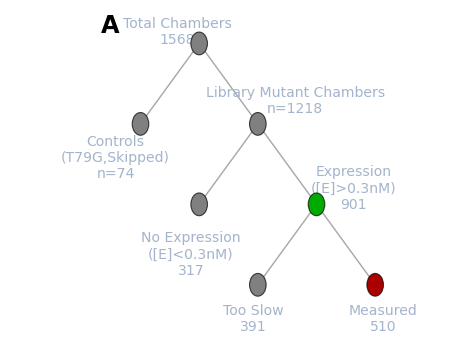

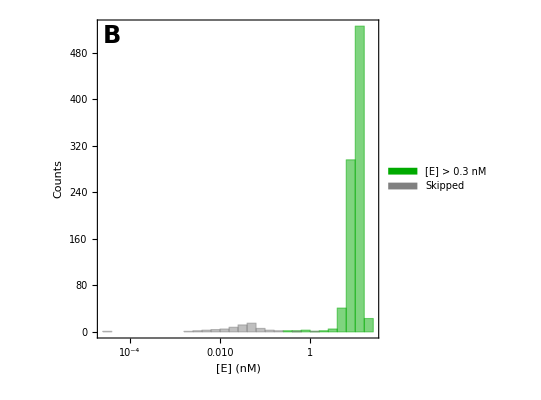

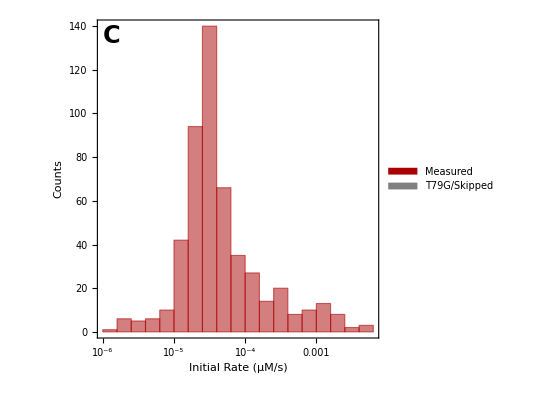

{{G64A,{0.148698,0.0364181}},{G64A,{0.360565,0.192781}},{R463G,{0.263337,0.302113}},{R164A,{0.0904577,7.29784}},{R164A,{7.86636,3.65153}}}

8.95773×10^-11

{{G64A,{0.148698,0.0364181}},{G64A,{0.360565,0.192781}},{R463G,{0.263337,0.302113}},{R164A,{0.0904577,7.29784}},{R164A,{7.86636,3.65153}}}

{{G64A,{326706.,301503.}},{G64A,{331924.,373307.}},{R463G,{295952.,312882.}},{R164A,{2382.2,116843.}},{R164A,{136307.,76309.4}}}

{{G64A,{0.455143,0.120789}},{G64A,{1.08629,0.516415}},{R463G,{0.889797,0.965579}},{R164A,{37.9724,62.4584}},{R164A,{57.7107,47.8517}}}

-Graphics- | -Graphics- | -Graphics-
-Graphics- |  | 
Experimental Summary. A) Counts of local limit of quantification control chambers (skipped and catalytically unresolvable mutants), library and known active site mutant chambers (library mutants), chambers which expressed >0.3 nM, and measured and chambers that were not sufficiently above the local limit of quantification (too slow). B) Distribution of enzyme concentrations in chambers with [E]>0.3 nM compared to the measured expression in the Skipped chambers. C) Distribution of rates measured in the chambers sufficiently above the local limit of quantification (Measured) compared to the rates measured in the control chambers, at the highest substrate concentration. D) Correlation between k_cat/K_M replicate measurements for measured library mutants. |  |

/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/temporary_PDF_0000.pdf

```mathematica
Dynamic[n]

start=AbsoluteTime[];

dataset=ds5[Select[#ExpIndex==1&&#AssayType==1&]];

Length[dataset]

Print["Fitting standard curves..."]
ProgressIndicator[Dynamic[count],{1,1568}]

addStandardCurveFits=Dataset@Table[Association[{"Indices"->Normal[dataset[count,"Indices"]],"StdCurveFitObject"->fitStdCurveNew[ToExpression[Normal[dataset[count,"SC_Concentrations"]]],If[NumberQ[ToExpression[Normal[dataset[count,"SC_Median_Chamber"]]][[1]]],ToExpression[Normal[dataset[count,"SC_Median_Chamber"]]],Missing[]]]}],{count,1,1568}];

addStandardCurveFits2=addStandardCurveFits[All,Append[#,{"StdCurveSlope"->If[MissingQ[#StdCurveFitObject],Missing["Nonexistent"],#StdCurveFitObject["BestFitParameters"][[2]]],"StdCurveIntercept"->If[MissingQ[#StdCurveFitObject],Missing["Nonexistent"],#StdCurveFitObject["BestFitParameters"][[1]]],"StdCurveRSquared"->If[MissingQ[#StdCurveFitObject],Missing["Nonexistent"],#StdCurveFitObject["RSquared"]]}]&];

withStdCurveFits=Dataset[JoinAcross[Normal[ds4],Normal[addStandardCurveFits2],{"Indices"},"Left"]];
Print["Adding standard curve plots..."]
ProgressIndicator[Dynamic[count2],{1,1568}]

withStdCurveFitsTemp=withStdCurveFits[Select[#ExpIndex==1&&#AssayType==1&]];

addStandardCurvePlots=Table[Association[{"Indices"->Normal[withStdCurveFitsTemp[count2,"Indices"]],"StandardCurvePlot"->makeStdCurvePlotNew[withStdCurveFitsTemp[count2,"StdCurveSlope"],withStdCurveFitsTemp[count2,"StdCurveIntercept"],ToExpression[withStdCurveFitsTemp[count2,"SC_Concentrations"]],ToExpression[withStdCurveFitsTemp[count2,"SC_Median_Chamber"]]]}],{count2,1,1568}];

AbsoluteTime[]-start

withStdCurvePlot=Dataset[JoinAcross[Normal[withStdCurveFits],addStandardCurvePlots,{"Indices"},"Left"]];

AbsoluteTime[]-start
withProgressCurves=withStdCurvePlot[All,Append[#,"TurnoverTimepoints(uM)"->convertTouM[ToExpression[#MedianIntensities],#StdCurveSlope,#StdCurveIntercept]]&];
cmupData=SemanticImport[cmupAggregatePath];
cmupParams=cmupData[All,{"MutantID","kcatNormMedian","KMMedian","kcat/KMNormMedianLimit","kcat/KMAggLimit"}];
cmupGrouped=cmupParams[GroupBy["MutantID"]];
wtkcatKm=cmupGrouped["WT",1,"kcat/KMNormMedianLimit"]
wtkcat=cmupGrouped["WT",1,"kcatNormMedian"]
wtKm=cmupGrouped["WT",1,"KMMedian"]
cmupParamsForCalc=Dataset[Table[Association[{"MutantID"->cmupGrouped[mutant,1,"MutantID"],"kcat"->If[cmupGrouped[mutant,1,"kcat/KMAggLimit"]==0,Select[Normal[cmupGrouped[mutant,All,"kcatNormMedian"]],NumberQ[#]&][[1]],Median[Select[Normal[cmupGrouped[mutant,All,"kcat/KMNormMedianLimit"]],#>0&]]/wtkcatKm*wtkcat],"Km"->If[cmupGrouped[mutant,1,"kcat/KMAggLimit"]==0,Select[Normal[cmupGrouped[mutant,All,"KMMedian"]],NumberQ[#]&][[1]],wtKm],"kobs"->Select[Normal[cmupGrouped[mutant,All,"kcat/KMNormMedianLimit"]],NumberQ[#]&][[1]],"Limit"->cmupGrouped[mutant,1,"kcat/KMAggLimit"]}],{mutant,1,Length[cmupGrouped]}]][GroupBy["MutantID"]]
obsProgressCurve[times_,concentrations_]:=Module[{temp1,fullProgressCurve},

If[MissingQ[concentrations],Missing[],

temp1={Normal[times],Normal[concentrations]};

fullProgressCurve=Sort[Table[{temp1[[1,n]],temp1[[2,n]]},{n,1,Length[temp1[[1]]]}],#1[[1]]<#2[[1]]&]]

]

progressCurveLambertW[kcat_?NumberQ,KM_,enz_,substrate_,time_]:=(substrate-KM*LambertW[substrate/KM*Exp[(substrate-kcat*enz*time)/KM]])

maxExponent=Round[Log[10,$MaxMachineNumber]]+1;

fitRateSuperposition[mutant_,progresscurve_,enzymeconc_,mecmupConc_]:=Module[{},

If[MissingQ[progresscurve],Table[Missing[],{7}],

chamberTestPC2=progresscurve;

econc=enzymeconc/1000.0;

cmupkcat=cmupParamsForCalc[mutant,1,"kcat"];
cmupKm=cmupParamsForCalc[mutant,1,"Km"];

limitQ=cmupParamsForCalc[mutant,1,"Limit"];

baseline=Min[chamberTestPC2[[All,2]]];

(* if we don't have measurements for kcat and Km then can't fit the superposition function - in these cases defaulting to a fit using the points at t>2500s *)
basicFit=LinearModelFit[Select[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],#[[1]]≥2500.0&],x,x];

basicFitRate=basicFit[[1,2,2]];

basicFitIntercept=basicFit[[1,2,1]];

pcBaselineCorrected=Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}];

p=Graphics[{EdgeForm[{Black,Thickness[0.125]}],FaceForm[Directive[GrayLevel[0.5],Opacity[0.7]]],Disk[],Opacity[0.1]}];

(* also modifying to fit only rates - the testing above is fitting the MecMUP kcat/KM *)

Which[NumberQ[cmupkcat]&&limitQ≠-1,

fit=Quiet[NMinimize[{Sum[((chamberTestPC2[[n,2]]-baseline)-(progressCurveLambertW[cmupkcat,cmupKm,econc,cmup,chamberTestPC2[[n,1]]]+(rate)*chamberTestPC2[[n,1]]))^2,{n,1,Length[chamberTestPC2]}],rate>-0.05&&rate<0.05&&cmup>0.0&&cmup<(mecmupConc/1000.0)},{cmup,rate}]];

lastFivePointsForFlag=Table[{chamberTestPC2[[n,1]],progressCurveLambertW[cmupkcat,cmupKm,econc,mecmupConc/1000.0,chamberTestPC2[[n,1]]]},{n,1,Length[chamberTestPC2]}];

flagFit=LinearModelFit[Select[lastFivePointsForFlag,#[[1]]≥2500.0&],x,x];

{fit[[2,1,2]],fit[[2,2,2]],Show[Plot[progressCurveLambertW[cmupkcat,cmupKm,econc,fit[[2,1,2]],t]+fit[[2,2,2]]*t,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.2,If[Max[chamberTestPC2[[All,2]]]>5.0,Max[chamberTestPC2[[All,2]]]+Abs[Max[chamberTestPC2[[All,2]]]]*0.5,5.5]},AspectRatio->0.8,PlotStyle->Gray],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotMarkers->{p,0.05}],Plot[progressCurveLambertW[cmupkcat,cmupKm,econc,fit[[2,1,2]],t],{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Directive[Gray,Dashed]],ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[18,Black,FontFamily->"Arial"],Epilog->Inset[mutant<>"\n"<>ToString[NumberForm[Round[fit[[2,2,2]],0.0000001],ScientificNotationThreshold->{-maxExponent,maxExponent}]]<>"μM/s"<>"\n[cMUP]="<>ToString[Round[fit[[2,1,2]],0.01]]<>" μM",Scaled[{0.80,0.3}]]],Abs[flagFit[[1,2,2]]],(fit[[2,2,2]]-trueBackgroundRate)/Abs[flagFit[[1,2,2]]],Show[Plot[progressCurveLambertW[cmupkcat,cmupKm,econc,fit[[2,1,2]],t]+fit[[2,2,2]]*t,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Darker[Red]],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotStyle->Directive[PointSize[0.02],Darker[Red],Opacity[0.5]]],PlotRange->All,AspectRatio->0.8,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[Black,18,FontFamily->"Arial"]],pcBaselineCorrected},

NumberQ[cmupkcat]&&limitQ==-1,

lastFivePointsForFlag=Table[{chamberTestPC2[[n,1]],progressCurveLambertW[cmupkcat,cmupKm,econc,mecmupConc/1000.0,chamberTestPC2[[n,1]]]},{n,1,Length[chamberTestPC2]}];

flagFit=LinearModelFit[Select[lastFivePointsForFlag,#[[1]]≥2500.0&],x,x];

{Missing[],basicFitRate,Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{If[(Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1)>0,0,Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1],If[Max[chamberTestPC2[[All,2]]]>5.0,Max[chamberTestPC2[[All,2]]]+Abs[Max[chamberTestPC2[[All,2]]]]*0.5,5.5]},AspectRatio->0.8,PlotStyle->Gray],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotMarkers->{p,0.05}],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[18,Black,FontFamily->"Arial"],Epilog->Inset[mutant<>"\n"<>ToString[NumberForm[Round[basicFitRate,0.0000001],ScientificNotationThreshold->{-maxExponent,maxExponent}]]<>"μM/s",Scaled[{0.80,0.2}]]],Abs[flagFit[[1,2,2]]],(fit[[2,2,2]]-trueBackgroundRate)/Abs[flagFit[[1,2,2]]],Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Darker[Red]],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotStyle->Directive[PointSize[0.02],Darker[Red],Opacity[0.5]]],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[Black,18,FontFamily->"Arial"]],pcBaselineCorrected},

NumberQ[cmupkcat]==False,

{Missing[],basicFitRate,Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{If[(Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1)>0,0,Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1],If[Max[chamberTestPC2[[All,2]]]>5.0,Max[chamberTestPC2[[All,2]]]+Abs[Max[chamberTestPC2[[All,2]]]]*0.5,5.5]},AspectRatio->0.8,PlotStyle->Gray],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotMarkers->{p,0.05}],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[18,Black,FontFamily->"Arial"],Epilog->Inset[mutant<>"\n"<>ToString[NumberForm[Round[basicFitRate,0.0000001],ScientificNotationThreshold->{-maxExponent,maxExponent}]]<>"μM/s",Scaled[{0.80,0.2}]]],Missing[],Missing[],Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Darker[Red]],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotStyle->Directive[PointSize[0.02],Darker[Red],Opacity[0.5]]],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[Black,18,FontFamily->"Arial"]],pcBaselineCorrected}


]]

]
withProgressCurves2=withProgressCurves[All,Append[#,{"ProgressCurve"->obsProgressCurve[ToExpression[#Times],#["TurnoverTimepoints(uM)"]],"EnzymeConc"->(#eGFPSummedI/#eGFPSlope)}]&];
itr=0;

Dynamic[itr]

optDataPoints2=withProgressCurves2[All,Append[#,itrNew=itr+1;itr=itrNew;out=Quiet[fitRateSuperposition[#MutantID,#ProgressCurve,#EnzymeConc,#SubstrateConc]];{"OptLinFitSlope"->out[[2]],"OptLinFitSlopeMinusTrueBackground"->out[[2]]-trueBackgroundRate,"ContaminantConc"->out[[1]],"FitPlot"->out[[3]],"ContaminantRate"->out[[4]],"ContaminantRatio"->out[[5]],"BackgroundFitPlot"->out[[6]],"ProgressCurveBaselineCorrected"->out[[7]]}]&];
indices=Normal[optDataPoints2[Select[#ExpIndex==1&]][All,"Indices"]];
Length[indices]
Dynamic[ind]

nearestLocalBG=Table[Association["Indices"->indices[[ind]],"NearestLocalBackgroundChambers"->findNearestBackgroundChambers[optDataPoints2,indices[[ind]]]],{ind,1,Length[indices]}];
(*nearestBackgroundChambers=Import["/Users/craig/Dropbox/HTMEK_processing/current/per-experiment_QC/nearestLocalBackgroundChambers.wxf"];*)

(*nearestBackgroundChambers=Import["/Users/craig/Dropbox/HTMEK_processing/current/per-experiment_QC/nearestLocalBackgroundChambers_SlowestChip.wxf"];*)

withNearestChambers=Dataset[JoinAcross[Normal[optDataPoints2],nearestLocalBG,"Indices","Left"]];
start=AbsoluteTime[];

count2=0;
Dynamic[count]

withPCs2=withNearestChambers[All,Quiet[Append[#,(Clear[forSelect];count=count2+1;forSelect=#NearestLocalBackgroundChambers;sconc=#SubstrateConc;
expIndex=#ExpIndex;
indices=#Indices;count2=count;

If[MissingQ[#ProgressCurve],"ProgressCurveOptFit2"->Missing[],

bgProgressCurves=Normal[optDataPoints2[Select[MemberQ[forSelect,#Indices]&&#ExpIndex==expIndex&]][All,"FitPlot"]];

{"ProgressCurveOptFit2"->If[Length[bgProgressCurves]>0,Show[DeleteCases[DeleteCases[{#FitPlot,Normal[optDataPoints2[Select[MemberQ[forSelect,#Indices]&&#SubstrateConc==sconc&&#ExpIndex==expIndex&]][All,"BackgroundFitPlot"]]},Missing["Nonexistent"],Infinity],Missing[],Infinity],AspectRatio->0.8,ImageSize->400,AspectRatio->0.6,ImagePadding->{{75,2},{60,8}},Epilog->Inset[Style[ToString[Round[sconc]]<>" μM",16,Black,FontFamily->"Arial"],Scaled[{0.18,0.85}]]],Missing["Nonexistent"]]}]

)]&]];


(*{"ProgressCurveOptFit2"->If[Length[bgProgressCurves]>0,Show[DeleteCases[DeleteCases[{#FitPlot,Normal[optDataPoints2[Select[MemberQ[forSelect,#Indices]&&#SubstrateConc==sconc&&#ExpIndex==expIndex&]][All,"BackgroundFitPlot"]]},Missing["Nonexistent"],Infinity],Missing[]],AspectRatio->0.8,ImageSize->400,AspectRatio->0.6,ImagePadding->{{75,2},{60,8}},Epilog->Inset[Style[ToString[Round[sconc]]<>" μM",16,Black,FontFamily->"Arial"],Scaled[{0.18,0.85}]]],Missing["Nonexistent"]]}*)

AbsoluteTime[]-start
Dynamic[n]
Dynamic[column]

(*datasetIN=withPCs;*)

datasetIN=withPCs2;

inhibitorconcentrations=Normal[datasetIN[Select[#Indices=={1,1}&],"InhibitorConcentrations"]];
substrateconcentrations=Normal[datasetIN[Select[#Indices=={1,1}&],"SubstrateConc"]]
type=Normal[datasetIN[Select[#Indices=={1,1}&],"AssayType"]];

exptIndices=Normal[datasetIN[Select[#Indices=={1,1}&],"ExpIndex"]];

dataset2=datasetIN;

start=AbsoluteTime[];

interpolations=Flatten[Table[Association[{"x"->column,"ExpIndex"->exptIndices[[n]],"AssayType"->type[[n]],"Interpolation"->interpolateDeadMutantsPerColumn[mutantList,exptIndices[[n]],column,dataset2,"OptLinFitSlopeMinusTrueBackground"],"MutantsUsedForLocalBG"->mutantList}],{n,1,Length[substrateconcentrations]},{column,1,28}],1];

dataset3=Dataset[JoinAcross[Normal[dataset2],interpolations,{"x","ExpIndex","AssayType"},"Left"]];

AbsoluteTime[]-start
start=AbsoluteTime[];

dataset=dataset3;

temp=Values[Normal[dataset[All,{"Indices","ExpIndex","OptLinFitSlopeMinusTrueBackground","MutantID","Interpolation"}]]];

localBGs=Table[Association[{"Indices"->temp[[n,1]],"ExpIndex"->temp[[n,2]],"LocalBackgroundRatio"->If[MissingQ[temp[[n,3]]],Missing["Nonexistent"],(temp[[n,3]])/(temp[[n,5,temp[[n,1,2]]]])]}],{n,1,Length[temp]}];

withlocalBG=Dataset[JoinAcross[Normal[dataset],localBGs,{"Indices","ExpIndex"},"Left"]];

AbsoluteTime[]-start

Dynamic[n]

scaleEachAssay=0;

eGFPslope=withlocalBG[1,"eGFPSlope"];

start=AbsoluteTime[];

dataset2=withlocalBG;


boundingMutants={"WT","T79S"};

rateKey="OptLinFitSlopeMinusTrueBackground";

temp=dataset2[Select[#ExpIndex==whichExpt&],{"Indices","ExpIndex",rateKey,"MutantID","Interpolation"}];

upperBound=Mean[Select[Values[Normal[dataset2[Select[#MutantID==boundingMutants[[1]]&&#ExpIndex==whichExpt&&#eGFPSummedI>EcutoffForBG*eGFPslope&],{rateKey}]]],NumberQ[#[[1]]]==True&]][[1]];

lowerBound=Mean[Select[Values[Normal[dataset2[Select[#MutantID==boundingMutants[[2]]&&#ExpIndex==whichExpt&&#eGFPSummedI>EcutoffForBG*eGFPslope&],{rateKey}]]],NumberQ[#[[1]]]==True&]][[1]];

allinColumn=Join@@Flatten[Table[AssociationThread[Table[{column,row},{row,1,56}],Sort[Values[Normal[dataset2[Select[#Indices[[1]]==column&&#ExpIndex==whichExpt&],{"Indices",rateKey,"MutantID"}]]],#1[[1,2]]<#2[[1,2]]&]],{column,1,28}],2];

temp2=temp[All,Append[#,{"Indices"->Normal[#[[1]]],"MaxLocalBackgroundPlot"->generateLocalBGPlot[Normal[#["Indices"]],Normal[#["ExpIndex"]],Normal[#["Interpolation"]]]}]&];

withlocalBGPlots=Dataset[JoinAcross[Normal[dataset2],Normal[temp2],{"Indices"},"Left"]];

CloseKernels[];

LaunchKernels[4];

dataset=withlocalBGPlots;

len=1568;

numKernels=Length[Kernels[]]

chunksize=Round[len/numKernels];
firstChunks =Table[{(chunksize*(n-1))+1, n*chunksize}, {n, numKernels-1}];
intervals=Append[firstChunks, {(chunksize*(numKernels-1))+1, len}];

toCalculate=dataset[GroupBy["Indices"]];

chunked = toCalculate[[#[[1]];;#[[2]]]]&/@intervals;

flattened=Table[chunked[[n]][Catenate],{n,1,Length[chunked]}];

addedMMcalc=Join@@ParallelMap[Quiet[fitMichaelisMenten[#,"OptLinFitSlopeMinusTrueBackground","optlin",eGFPslope,scaleEachAssay]]&,flattened];

AbsoluteTime[]-start

CloseKernels[]
Dynamic[n]

grouped=addedMMcalc[GroupBy["Indices"]];

indicesOut=Values[#]&/@Values[Normal[grouped[All,1,{"MutantID","Indices","fit_mm_kcat","fit_mm_KM"}]]];

addkcatoverkm=Table[Association[{"MutantID"->indicesOut[[n,1]],"Indices"->indicesOut[[n,2]],"fit_mm_kcatoverKM_MMfit"->If[MissingQ[indicesOut[[n,3]]],Missing["Nonexistent"],indicesOut[[n,3]]/(indicesOut[[n,4]]*10^-6)]}],{n,1,1568}];

addedkcatoverkm=Dataset[JoinAcross[Normal[addedMMcalc],addkcatoverkm,"Indices","Left"]]//Quiet;


grouped=addedkcatoverkm[GroupBy["Indices"]];

indicesOut=Values[#]&/@Values[Normal[grouped[All,1,{"MutantID","Indices"}]]];

pGFP=Graphics[{EdgeForm[{Black,Thickness[0.125]}],FaceForm[Directive[Darker[Green],Opacity[0.7]]],Disk[],Opacity[0.1]}];

addedeGFPIntensityPlot=Table[Association[{"MutantID"->indicesOut[[n,1]],"Indices"->indicesOut[[n,2]],"eGFPIntensityPlot"->If[egfpSameFlag==0,ListPlot[Normal[grouped[n,All,"eGFPSummedI"]]/10^6,PlotRange->{0,Max[Normal[grouped[n,All,"eGFPSummedI"]]/10^6]*1.5},Frame->True,Axes->False,PlotMarkers->{pGFP,0.05},FrameStyle->Directive[20,Black,FontFamily->"Arial"],FrameLabel->{"Assay Number","eGFP Intensity (×10^6)"},ImagePadding->{{75,2},{65,5}},AspectRatio->0.8,ImageSize->400],ListPlot[{{1,Normal[grouped[n,1,"eGFPSummedI"]]/10^6}},PlotRange->{{0,Length[Normal[grouped[n,All,"eGFPSummedI"]]]},{0,Max[Normal[grouped[n,All,"eGFPSummedI"]]/10^6]*1.5}},Frame->True,Axes->False,PlotMarkers->{pGFP,0.05},GridLines->{None,{Normal[grouped[n,1,"eGFPSummedI"]]/10^6}},GridLinesStyle->Directive[Dashed,Darker[Green]],FrameStyle->Directive[20,Black,FontFamily->"Arial"],FrameLabel->{"Assay Number","eGFP Intensity (×10^6)"},ImagePadding->{{75,2},{65,5}},AspectRatio->0.8,ImageSize->400,FrameTicks->{{If[IntegerQ[#],#,N[#]]&/@FindDivisions[{0,Max[Normal[grouped[n,All,"eGFPSummedI"]]/10^6]},5],None},{If[IntegerQ[#],#,N[#]]&/@FindDivisions[{0,Length[Normal[grouped[n,All,"eGFPSummedI"]]]},Round[Length[Normal[grouped[n,All,"eGFPSummedI"]]]/2]],None}},Epilog->Inset[Style["eGFP measured\nbefore 1st assay only",14,Darker[Green]],Scaled[{0.7,0.3}]]]]}],{n,1,1568}];

addedeGFPIntensityPlotDataset=Dataset[JoinAcross[JoinAcross[Normal[addedkcatoverkm],addedeGFPIntensityPlot,"Indices","Left"],Normal[wxfForImageStamps[Select[#ExpIndex==1&],{"Indices","eGFPPostSDSImage"}]],"Indices","Left"]]//Quiet;

AbsoluteTime[]-start
normalizedDataset=Normal[addedeGFPIntensityPlotDataset];

replaced=Fold[Replace[#1,#2,Infinity]&,normalizedDataset,{_FittedModel->"NaN",_Graphics->"NaN",_Image->"NaN",_NonlinearModelFit->"NaN",_Times->"NaN",_Overlay->"NaN",_ReplaceAll->"NaN"}];

headers=Keys[replaced[[1]]];

(*values=Map[replaceBracketsBack,Values[replaced],{2}];*)

values=Values[replaced];

datasetForExport=Prepend[values,headers];

Export[StringJoin["~/Desktop/",addedkcatoverkm[1,"GlobalExperimentIndex"],"_MecMUP_LinComb.csv.bz2"],datasetForExport,"Data"];

(* summary table *)

fixLogPlots[gr_]:=gr/.f:(Charting`ScaledTicks|Charting`ScaledFrameTicks)[{Log,Exp}]:>(Part[#,;;, ;;3]&@*f);

p2=Graphics[{EdgeForm[{Black,Thickness[0.125]}],FaceForm[Directive[Gray,Opacity[0.7]]],Disk[],Opacity[0.1]}];

expressed=addedeGFPIntensityPlotDataset[Select[#ExpIndex==1&&#ManualGFPFlag==0&&#EnzymeConc>0.3&]];

Length[expressed]

skipped=addedeGFPIntensityPlotDataset[Select[#ExpIndex==1&&#ManualGFPFlag==0&&#MutantID=="Skipped"&]];

allLibraryChambers=addedeGFPIntensityPlotDataset[Select[#ExpIndex==1&&#MutantID≠"Skipped"&&#MutantID≠"T79G"&]];

expressedLibrary=allLibraryChambers[Select[#EnzymeConc>0.3&&#ManualGFPFlag==0&]];

Length[allLibraryChambers]
Length[expressedLibrary]

tooSlow=addedeGFPIntensityPlotDataset[Select[#ExpIndex==whichExpt&&#LocalBackgroundRatio≤5.0&&MemberQ[Normal[expressedLibrary[All,"Indices"]],#Indices]&]];

Length[tooSlow]

measured=addedeGFPIntensityPlotDataset[Select[#ExpIndex==whichExpt&&#LocalBackgroundRatio>5.0&&MemberQ[Normal[expressedLibrary[All,"Indices"]],#Indices]&]];

Length[measured]

countTree=TreePlot[{1->2,1->3,3->4,3->5,5->6,5->7},VertexSize->Medium,VertexCoordinates->{{0,0},{-1,-1},{1,-1},{0,-2},{2,-2},{1,-3},{3,-3}},EdgeStyle->Gray,Epilog->Inset[Style["A",24,Bold],Scaled[{0.0,1.0}]],VertexLabels->{1->Placed[Style["Total Chambers\n1568",14],{-0.8,1}],2->Placed[Style["Controls\n(T79G,Skipped)\nStyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[skipped]],14],{-1,-1}],3->Placed[Style["Library Mutant Chambers\nStyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[allLibraryChambers]],14],{2.75,1.5}],4->Placed[Style["No Expression\n([E]<0.3nM)\n"<>ToString[Length[allLibraryChambers]-Length[expressedLibrary]],14],{0,-1.7}],5->Placed[Style["Expression\n([E]>0.3nM)\n"<>ToString[Length[expressedLibrary]],14],{2.75,1.2}],7->Placed[Style["Measured\n"<>ToString[Length[measured]],14],{1,-1}],6->Placed[Style["Too Slow\n"<>ToString[Length[tooSlow]],14],{0.25,-1}]},ImageSize->450,VertexStyle->
Join[
{1->Gray}, 
#->Gray&/@{1,2,3,4,6},
#->Darker[Green]&/@{5},
#->Darker[Red]&/@{7}
]]

eConcHist=fixLogPlots@Histogram[{Normal[expressedLibrary[All,"EnzymeConc"]],Normal[skipped[All,"EnzymeConc"]]},"Log",ChartStyle->{Darker[Green],Gray},Frame->True,Axes->False,PlotRange->All,FrameStyle->Directive[20,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->400,FrameLabel->{Style["[E] (nM)",SingleLetterItalics->False],Style["Counts",SingleLetterItalics->False]},Epilog->{Inset[SwatchLegend[{Darker[Green],Gray},Style[#,16]&/@{"[E] > 0.3 nM","Skipped"}],Scaled[{0.25,0.9}]],Inset[Style["B",24,Bold],Scaled[{0.05,0.95}]]}]

rateHist=fixLogPlots@Histogram[{Normal[measured[All,"OptLinFitSlopeMinusTrueBackground"]],Normal[skipped[All,"OptLinFitSlopeMinusTrueBackground"]]},"Log",ChartStyle->{Darker[Red],Gray},Frame->True,Axes->False,PlotRange->All,FrameStyle->Directive[20,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->400,FrameLabel->{Style["Initial Rate (μM/s)",SingleLetterItalics->False],Style["Counts",SingleLetterItalics->False]},Epilog->{Inset[SwatchLegend[{Darker[Red],Gray},Style[#,16]&/@{"Measured","T79G/Skipped"}],Scaled[{0.8,0.9}]],Inset[Style["C",24,Bold],Scaled[{0.05,0.95}]]}]

measured2=measured;

measured3=measured2[All,{"MutantID","fit_mm_kcat"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured3[n,1,"MutantID"],#}&/@Partition[Normal[measured3[n,All,"fit_mm_kcat"]],2],{n,1,Length[measured3]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]]

measured2=measured[All,{"MutantID","fit_mm_kcat","fit_mm_KM","fit_mm_kcatoverKM_MMfit"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured2[n,1,"MutantID"],#}&/@Partition[Normal[measured2[n,All,"fit_mm_kcat"]],2],{n,1,Length[measured2]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]];

rmse=Sqrt[Mean[Table[(Log[10,pairs[[n,2,1]]]-Log[10,pairs[[n,2,2]]])^2,{n,1,Length[pairs]}]]];

pearsonR2=Correlation[Log[10,pairs[[All,2,1]]],Log[10,pairs[[All,2,2]]]]^2;

(*kcatplot=fixLogPlots@Show[ListLogLogPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[pairs[[n,2]],pairs[[n,1]]],pairs[[n,2]]],{n,1,Length[pairs]}],PlotRange->{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}},Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->500,PlotMarkers->{p2,0.02},FrameLabel->{"SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"] (rep.1) (/s)","SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"] (rep.2) (/s)"}],LogLogPlot[{x,x/2,x*2},{x,0.0001,10000},PlotStyle->Directive[Gray,Dashed]],ImagePadding->100];*)

kcatplot=Show[ListPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[Log[10,pairs[[n,2]]],pairs[[n,1]]],Log[10,pairs[[n,2]]]],{n,1,Length[pairs]}],PlotRange->Log[10,{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}}],Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->475,PlotMarkers->{p2,0.02},FrameLabel->{"Log10(SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]) (rep.1) (/s)","Log10(SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]) (rep.2) (/s)"},Epilog->{Inset[Style["SuperscriptBox[StyleBox[\"R\",FontSlant->\"Italic\"], \"2\"]="<>ToString[Round[pearsonR2,0.01]],14],Scaled[{0.2,0.9}]],Inset[Style["RMSE="<>ToString[Round[rmse,0.01]],14],Scaled[{0.2,0.8}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[pairs]],14],Scaled[{0.2,0.7}]],Inset[Style["D",24,Bold],Scaled[{0.05,0.95}]]}],Plot[{x,x-0.301,x+0.301},{x,-5,10},PlotStyle->Directive[Gray,Dashed]],ImagePadding->{{100,20},{100,50}}];

measured2=measured[All,{"MutantID","fit_mm_KM"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured2[n,1,"MutantID"],#}&/@Partition[Normal[measured2[n,All,"fit_mm_KM"]],2],{n,1,Length[measured2]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]];

rmse=Sqrt[Mean[Table[(Log[10,pairs[[n,2,1]]]-Log[10,pairs[[n,2,2]]])^2,{n,1,Length[pairs]}]]];

pearsonR2=Correlation[Log[10,pairs[[All,2,1]]],Log[10,pairs[[All,2,2]]]]^2;

KmPlot=Show[ListPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[Log[10,pairs[[n,2]]],pairs[[n,1]]],Log[10,pairs[[n,2]]]],{n,1,Length[pairs]}],PlotRange->Log[10,{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}}],Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->475,PlotMarkers->{p2,0.02},FrameLabel->{Style["Log[10,SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.1) (/s)",SingleLetterItalics->False],Style["Log[10,SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.2) (/s)",SingleLetterItalics->False]},Epilog->{Inset[Style["SuperscriptBox[StyleBox[\"R\",FontSlant->\"Italic\"], \"2\"]="<>ToString[Round[pearsonR2,0.01]],14],Scaled[{0.2,0.9}]],Inset[Style["RMSE="<>ToString[Round[rmse,0.01]],14],Scaled[{0.2,0.8}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[pairs]],14],Scaled[{0.2,0.7}]],Inset[Style["E",24,Bold],Scaled[{0.05,0.95}]]}],Plot[{x,x-0.301,x+0.301},{x,-5,10},PlotStyle->Directive[Gray,Dashed]],Plot[10,{x,-5,Log[10,0.5]},Filling->-5,FillingStyle->Directive[LightPink,Opacity[0.5]],PlotStyle->Directive[LightPink,Opacity[0.8]]],ImagePadding->{{100,20},{100,50}}];

measured2=measured[All,{"MutantID","fit_mm_kcatoverKM_MMfit"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured2[n,1,"MutantID"],#}&/@Partition[Normal[measured2[n,All,"fit_mm_kcatoverKM_MMfit"]],2],{n,1,Length[measured2]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]];

rmse=Sqrt[Mean[Table[(Log[10,pairs[[n,2,1]]]-Log[10,pairs[[n,2,2]]])^2,{n,1,Length[pairs]}]]];

pearsonR2=Correlation[Log[10,pairs[[All,2,1]]],Log[10,pairs[[All,2,2]]]]^2;

kcatKMplot=Show[ListPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[Log[10,pairs[[n,2]]],pairs[[n,1]]],Log[10,pairs[[n,2]]]],{n,1,Length[pairs]}],PlotRange->Log[10,{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}}],Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->475,PlotMarkers->{p2,0.02},FrameLabel->{Style["Log[10,SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]/SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.1) (/M /s)",SingleLetterItalics->False],Style["Log[10,SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]/SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.2) (/M /s)",SingleLetterItalics->False]},Epilog->{Inset[Style["SuperscriptBox[StyleBox[\"R\",FontSlant->\"Italic\"], \"2\"]="<>ToString[Round[pearsonR2,0.01]],14],Scaled[{0.2,0.9}]],Inset[Style["RMSE="<>ToString[Round[rmse,0.01]],14],Scaled[{0.2,0.8}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[pairs]],14],Scaled[{0.2,0.7}]],Inset[Style["F",24,Bold],Scaled[{0.05,0.95}]]}],Plot[{x,x-0.301,x+0.301},{x,-5,10},PlotStyle->Directive[Gray,Dashed]],ImagePadding->{{100,20},{100,50}}];

(*Grid[{{countTree,kcatplot},{eConcHist,KmPlot},{rateHist,kcatKMplot}}]*)

summaryGrid=Grid[{{countTree,eConcHist,rateHist},{kcatKMplot},{Style["Experimental Summary. A) Counts of local limit of quantification control chambers (skipped and catalytically unresolvable mutants), library and known active site mutant chambers (library mutants), chambers which expressed >0.3 nM, and measured and chambers that were not sufficiently above the local limit of quantification (too slow). B) Distribution of enzyme concentrations in chambers with [E]>0.3 nM compared to the measured expression in the Skipped chambers. C) Distribution of rates measured in the chambers sufficiently above the local limit of quantification (Measured) compared to the rates measured in the control chambers, at the highest substrate concentration. D) Correlation between SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]/SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"] replicate measurements for measured library mutants.",18,FontFamily->"Arial",TextAlignment->Left,SingleLetterItalics->False],SpanFromLeft}}]

Export[StringJoin["/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/temporary_PDF_","0000",".pdf"],summaryGrid,"AllowRasterization"->False]
```

```mathematica
dataset=addedeGFPIntensityPlotDataset;

indices=Sort[Normal[DeleteDuplicates[dataset[[All,"Indices"]]]]];

Do[

(* change 3rd argument to correspond to type of assay: cMUP, MeP, MecMUP, Inhibition *)
(* added 4th argument "unscaled" *)
out=makeGridMecMUP[dataset,indices[[n]],"MecMUP","unscaled"];

Export[StringJoin["/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/temporary_PDF_",StringPadLeft[ToString[n],4,"0"],".pdf"],out,"AllowRasterization"->False];

,{n,1,1568}];

session = StartExternalSession[<|"System"->"Python","Version"->"3.6", "SessionProlog"->{"import os", "from PyPDF2 import PdfFileMerger, PdfFileReader"}|>];

defineRoot = "root='/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/'";
getNames = "pdfs1=[os.path.join(root, dir) for dir in os.listdir(root) if '.pdf' in dir]";
getNames2="pdfs=sorted(pdfs1)";
createMerger = "merger = PdfFileMerger()";
executeMerge = "for pdf in pdfs: merger.append(PdfFileReader(pdf,'rb'))";
executeExport = StringJoin["merger.write('/Users/craig/Desktop/",Values[Normal[dataset[1,{"GlobalExperimentIndex"}]]][[1]],".pdf')"];
completionNotice = "print('PDF Concatenation Complete')";

ExternalEvaluate[session,{defineRoot, getNames,getNames2, createMerger, executeMerge, executeExport, completionNotice}];
```

PDF Concatenation Complete

#### Dataset 4

```mathematica
dataset=remapNames[generateDatasetFromCSV[Import["/Users/craig/Dropbox/HTMEK_processing/MecMUP_QC_200220/180531_S2_d1_MecMUP_1_MecMUP_LinComb.csv.bz2"],"GlyScan","180531_S2_d1_MecMUP_1_MecMUP_LinComb"]];

wxfForImageStamps=Import["/Users/craig/Desktop/180531_S2_d1_MecMUP_1_newLBR.wxf"];

dataset[1;;2]
```

```mathematica
keysToKeep={"GlobalExperimentIndex","Date","Experiment","Setup","Device","PhosphateSensorConc","eGFPSlope","x","y","median_chamber","sum_chamber","std_chamber","x_center_chamber","y_center_chamber","radius_chamber","xslice","yslice","MutantID","time_s","median_button_Button_Quant","summed_button_Button_Quant","eGFPSummedI","std_button_Button_Quant","x_button_center_Button_Quant","y_button_center_Button_Quant","radius_button_disk_Button_Quant","median_button_annulus_Button_Quant","summed_button_annulus_normed_Button_Quant","std_button_annulus_localBG_Button_Quant","inner_radius_button_annulus_Button_Quant","outer_radius_button_annulus_Button_Quant","xslice_Button_Quant","yslice_Button_Quant","MutantID_Button_Quant","series_index","Times","MedianIntensities","ExpIndex","AssayType","SubstrateConc","InhibitorConcentrations","Zn2+","SC_Concentrations","SC_Median_Chamber","SC_Median_Chamber","ManualGFPFlag","Indices"};
ds2=dataset[All,Append[#,{"Indices2"->ToExpression[#Indices]}]&];

ds3=ds2[All,{"GlobalExperimentIndex","Date","Experiment","Setup","Device","PhosphateSensorConc","eGFPSlope","x","y","median_chamber","sum_chamber","std_chamber","x_center_chamber","y_center_chamber","radius_chamber","xslice","yslice","MutantID","time_s","median_button_Button_Quant","summed_button_Button_Quant","eGFPSummedI","std_button_Button_Quant","x_button_center_Button_Quant","y_button_center_Button_Quant","radius_button_disk_Button_Quant","median_button_annulus_Button_Quant","summed_button_annulus_normed_Button_Quant","std_button_annulus_localBG_Button_Quant","inner_radius_button_annulus_Button_Quant","outer_radius_button_annulus_Button_Quant","xslice_Button_Quant","yslice_Button_Quant","MutantID_Button_Quant","series_index","Times","MedianIntensities","ExpIndex","AssayType","SubstrateConc","InhibitorConcentrations","Zn2+","SC_Concentrations","SC_Median_Chamber","SC_Median_Chamber","ManualGFPFlag","Indices2"}];

ds4=ds3[All,Append[#,"Indices"->#Indices2]&][All,keysToKeep];

ds4[GroupBy["Indices"]][1;;2,All,"eGFPSummedI"]
ds4[GroupBy["Indices"]][1;;2,All,"SubstrateConc"]
egfpSameFlag=0;
ds5=ds4[All,Append[#,"eGFPConstant"->egfpSameFlag]&];
```

```mathematica
mutantList={"T79G","Skipped"};

whichExpt=4;

EcutoffForBG=0.3;

trueBackgroundRate=-2.3 10^-6;
```

1568

Fitting standard curves...

Adding standard curve plots...

63.285705

64.512939

1.4213×10^6

121.236

85.3261

Dataset[<>]

General::readp: Symbol None is read-protected.

General::stop: Further output of General::readp will be suppressed during this calculation.

1568

General::readp: Symbol None is read-protected.

General::stop: Further output of General::readp will be suppressed during this calculation.

397.664258

{500.,1000.,1500.,2000.,500.}

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

34.58432

24.38439

4

241.6845

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

345.56247

1404

1270

1250

343

907

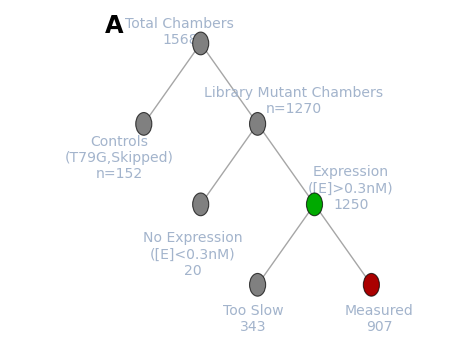

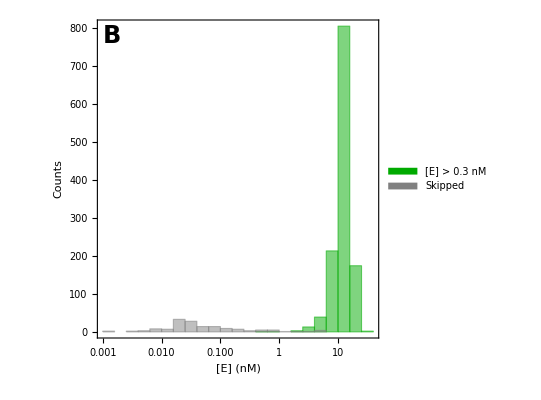

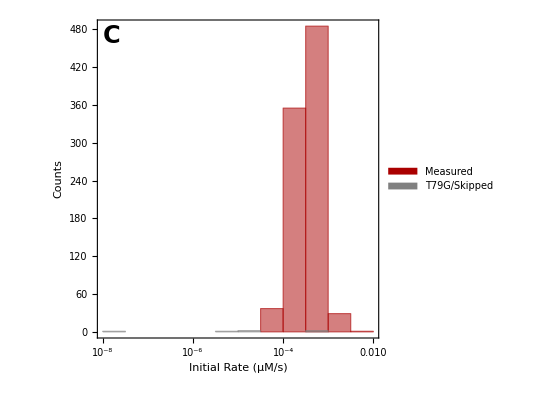

{{V373G,{3.05604,1.69859}},{G474A,{1.2604,1.43733}},{K162A,{0.143886,0.357901}},{K162A,{0.308352,0.103709}},{K162A,{0.230966,0.321927}}}

0.0169342

{{V373G,{3.05604,1.69859}},{G474A,{1.2604,1.43733}},{K162A,{0.143886,0.357901}},{K162A,{0.308352,0.103709}},{K162A,{0.230966,0.321927}}}

{{V373G,{193787.,195677.}},{G474A,{205851.,191835.}},{K162A,{3122.58,8760.67}},{K162A,{7224.39,3347.16}},{K162A,{9642.92,9268.09}}}

{{V373G,{15.7701,8.68061}},{G474A,{6.12287,7.49253}},{K162A,{46.0792,40.8531}},{K162A,{42.6821,30.9841}},{K162A,{23.9519,34.735}}}

-Graphics- | -Graphics- | -Graphics-
-Graphics- |  | 
Experimental Summary. A) Counts of local limit of quantification control chambers (skipped and catalytically unresolvable mutants), library and known active site mutant chambers (library mutants), chambers which expressed >0.3 nM, and measured and chambers that were not sufficiently above the local limit of quantification (too slow). B) Distribution of enzyme concentrations in chambers with [E]>0.3 nM compared to the measured expression in the Skipped chambers. C) Distribution of rates measured in the chambers sufficiently above the local limit of quantification (Measured) compared to the rates measured in the control chambers, at the highest substrate concentration. D) Correlation between k_cat/K_M replicate measurements for measured library mutants. |  |

/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/temporary_PDF_0000.pdf

```mathematica
Dynamic[n]

start=AbsoluteTime[];

dataset=ds5[Select[#ExpIndex==1&&#AssayType==1&]];

Length[dataset]

Print["Fitting standard curves..."]
ProgressIndicator[Dynamic[count],{1,1568}]

addStandardCurveFits=Dataset@Table[Association[{"Indices"->Normal[dataset[count,"Indices"]],"StdCurveFitObject"->fitStdCurveNew[ToExpression[Normal[dataset[count,"SC_Concentrations"]]],If[NumberQ[ToExpression[Normal[dataset[count,"SC_Median_Chamber"]]][[1]]],ToExpression[Normal[dataset[count,"SC_Median_Chamber"]]],Missing[]]]}],{count,1,1568}];

addStandardCurveFits2=addStandardCurveFits[All,Append[#,{"StdCurveSlope"->If[MissingQ[#StdCurveFitObject],Missing["Nonexistent"],#StdCurveFitObject["BestFitParameters"][[2]]],"StdCurveIntercept"->If[MissingQ[#StdCurveFitObject],Missing["Nonexistent"],#StdCurveFitObject["BestFitParameters"][[1]]],"StdCurveRSquared"->If[MissingQ[#StdCurveFitObject],Missing["Nonexistent"],#StdCurveFitObject["RSquared"]]}]&];

withStdCurveFits=Dataset[JoinAcross[Normal[ds4],Normal[addStandardCurveFits2],{"Indices"},"Left"]];
Print["Adding standard curve plots..."]
ProgressIndicator[Dynamic[count2],{1,1568}]

withStdCurveFitsTemp=withStdCurveFits[Select[#ExpIndex==1&&#AssayType==1&]];

addStandardCurvePlots=Table[Association[{"Indices"->Normal[withStdCurveFitsTemp[count2,"Indices"]],"StandardCurvePlot"->makeStdCurvePlotNew[withStdCurveFitsTemp[count2,"StdCurveSlope"],withStdCurveFitsTemp[count2,"StdCurveIntercept"],ToExpression[withStdCurveFitsTemp[count2,"SC_Concentrations"]],ToExpression[withStdCurveFitsTemp[count2,"SC_Median_Chamber"]]]}],{count2,1,1568}];

AbsoluteTime[]-start

withStdCurvePlot=Dataset[JoinAcross[Normal[withStdCurveFits],addStandardCurvePlots,{"Indices"},"Left"]];

AbsoluteTime[]-start
withProgressCurves=withStdCurvePlot[All,Append[#,"TurnoverTimepoints(uM)"->convertTouM[ToExpression[#MedianIntensities],#StdCurveSlope,#StdCurveIntercept]]&];
cmupData=SemanticImport[cmupAggregatePath];
cmupParams=cmupData[All,{"MutantID","kcatNormMedian","KMMedian","kcat/KMNormMedianLimit","kcat/KMAggLimit"}];
cmupGrouped=cmupParams[GroupBy["MutantID"]];
wtkcatKm=cmupGrouped["WT",1,"kcat/KMNormMedianLimit"]
wtkcat=cmupGrouped["WT",1,"kcatNormMedian"]
wtKm=cmupGrouped["WT",1,"KMMedian"]
cmupParamsForCalc=Dataset[Table[Association[{"MutantID"->cmupGrouped[mutant,1,"MutantID"],"kcat"->If[cmupGrouped[mutant,1,"kcat/KMAggLimit"]==0,Select[Normal[cmupGrouped[mutant,All,"kcatNormMedian"]],NumberQ[#]&][[1]],Median[Select[Normal[cmupGrouped[mutant,All,"kcat/KMNormMedianLimit"]],#>0&]]/wtkcatKm*wtkcat],"Km"->If[cmupGrouped[mutant,1,"kcat/KMAggLimit"]==0,Select[Normal[cmupGrouped[mutant,All,"KMMedian"]],NumberQ[#]&][[1]],wtKm],"kobs"->Select[Normal[cmupGrouped[mutant,All,"kcat/KMNormMedianLimit"]],NumberQ[#]&][[1]],"Limit"->cmupGrouped[mutant,1,"kcat/KMAggLimit"]}],{mutant,1,Length[cmupGrouped]}]][GroupBy["MutantID"]]
obsProgressCurve[times_,concentrations_]:=Module[{temp1,fullProgressCurve},

If[MissingQ[concentrations],Missing[],

temp1={Normal[times],Normal[concentrations]};

fullProgressCurve=Sort[Table[{temp1[[1,n]],temp1[[2,n]]},{n,1,Length[temp1[[1]]]}],#1[[1]]<#2[[1]]&]]

]

progressCurveLambertW[kcat_?NumberQ,KM_,enz_,substrate_,time_]:=(substrate-KM*LambertW[substrate/KM*Exp[(substrate-kcat*enz*time)/KM]])

maxExponent=Round[Log[10,$MaxMachineNumber]]+1;

fitRateSuperposition[mutant_,progresscurve_,enzymeconc_,mecmupConc_]:=Module[{},

If[MissingQ[progresscurve],Table[Missing[],{7}],

chamberTestPC2=progresscurve;

econc=enzymeconc/1000.0;

cmupkcat=cmupParamsForCalc[mutant,1,"kcat"];
cmupKm=cmupParamsForCalc[mutant,1,"Km"];

limitQ=cmupParamsForCalc[mutant,1,"Limit"];

baseline=Min[chamberTestPC2[[All,2]]];

(* if we don't have measurements for kcat and Km then can't fit the superposition function - in these cases defaulting to a fit using the points at t>2500s *)
basicFit=LinearModelFit[Select[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],#[[1]]≥2500.0&],x,x];

basicFitRate=basicFit[[1,2,2]];

basicFitIntercept=basicFit[[1,2,1]];

pcBaselineCorrected=Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}];

p=Graphics[{EdgeForm[{Black,Thickness[0.125]}],FaceForm[Directive[GrayLevel[0.5],Opacity[0.7]]],Disk[],Opacity[0.1]}];

(* also modifying to fit only rates - the testing above is fitting the MecMUP kcat/KM *)

Which[NumberQ[cmupkcat]&&limitQ≠-1,

fit=Quiet[NMinimize[{Sum[((chamberTestPC2[[n,2]]-baseline)-(progressCurveLambertW[cmupkcat,cmupKm,econc,cmup,chamberTestPC2[[n,1]]]+(rate)*chamberTestPC2[[n,1]]))^2,{n,1,Length[chamberTestPC2]}],rate>-0.05&&rate<0.05&&cmup>0.0&&cmup<(mecmupConc/1000.0)},{cmup,rate}]];

lastFivePointsForFlag=Table[{chamberTestPC2[[n,1]],progressCurveLambertW[cmupkcat,cmupKm,econc,mecmupConc/1000.0,chamberTestPC2[[n,1]]]},{n,1,Length[chamberTestPC2]}];

flagFit=LinearModelFit[Select[lastFivePointsForFlag,#[[1]]≥2500.0&],x,x];

{fit[[2,1,2]],fit[[2,2,2]],Show[Plot[progressCurveLambertW[cmupkcat,cmupKm,econc,fit[[2,1,2]],t]+fit[[2,2,2]]*t,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.2,If[Max[chamberTestPC2[[All,2]]]>5.0,Max[chamberTestPC2[[All,2]]]+Abs[Max[chamberTestPC2[[All,2]]]]*0.5,5.5]},AspectRatio->0.8,PlotStyle->Gray],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotMarkers->{p,0.05}],Plot[progressCurveLambertW[cmupkcat,cmupKm,econc,fit[[2,1,2]],t],{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Directive[Gray,Dashed]],ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[18,Black,FontFamily->"Arial"],Epilog->Inset[mutant<>"\n"<>ToString[NumberForm[Round[fit[[2,2,2]],0.0000001],ScientificNotationThreshold->{-maxExponent,maxExponent}]]<>"μM/s"<>"\n[cMUP]="<>ToString[Round[fit[[2,1,2]],0.01]]<>" μM",Scaled[{0.80,0.3}]]],Abs[flagFit[[1,2,2]]],(fit[[2,2,2]]-trueBackgroundRate)/Abs[flagFit[[1,2,2]]],Show[Plot[progressCurveLambertW[cmupkcat,cmupKm,econc,fit[[2,1,2]],t]+fit[[2,2,2]]*t,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Darker[Red]],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotStyle->Directive[PointSize[0.02],Darker[Red],Opacity[0.5]]],PlotRange->All,AspectRatio->0.8,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[Black,18,FontFamily->"Arial"]],pcBaselineCorrected},

NumberQ[cmupkcat]&&limitQ==-1,

lastFivePointsForFlag=Table[{chamberTestPC2[[n,1]],progressCurveLambertW[cmupkcat,cmupKm,econc,mecmupConc/1000.0,chamberTestPC2[[n,1]]]},{n,1,Length[chamberTestPC2]}];

flagFit=LinearModelFit[Select[lastFivePointsForFlag,#[[1]]≥2500.0&],x,x];

{Missing[],basicFitRate,Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{If[(Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1)>0,0,Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1],If[Max[chamberTestPC2[[All,2]]]>5.0,Max[chamberTestPC2[[All,2]]]+Abs[Max[chamberTestPC2[[All,2]]]]*0.5,5.5]},AspectRatio->0.8,PlotStyle->Gray],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotMarkers->{p,0.05}],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[18,Black,FontFamily->"Arial"],Epilog->Inset[mutant<>"\n"<>ToString[NumberForm[Round[basicFitRate,0.0000001],ScientificNotationThreshold->{-maxExponent,maxExponent}]]<>"μM/s",Scaled[{0.80,0.2}]]],Abs[flagFit[[1,2,2]]],(fit[[2,2,2]]-trueBackgroundRate)/Abs[flagFit[[1,2,2]]],Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Darker[Red]],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotStyle->Directive[PointSize[0.02],Darker[Red],Opacity[0.5]]],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[Black,18,FontFamily->"Arial"]],pcBaselineCorrected},

NumberQ[cmupkcat]==False,

{Missing[],basicFitRate,Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{If[(Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1)>0,0,Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1],If[Max[chamberTestPC2[[All,2]]]>5.0,Max[chamberTestPC2[[All,2]]]+Abs[Max[chamberTestPC2[[All,2]]]]*0.5,5.5]},AspectRatio->0.8,PlotStyle->Gray],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotMarkers->{p,0.05}],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[18,Black,FontFamily->"Arial"],Epilog->Inset[mutant<>"\n"<>ToString[NumberForm[Round[basicFitRate,0.0000001],ScientificNotationThreshold->{-maxExponent,maxExponent}]]<>"μM/s",Scaled[{0.80,0.2}]]],Missing[],Missing[],Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Darker[Red]],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotStyle->Directive[PointSize[0.02],Darker[Red],Opacity[0.5]]],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[Black,18,FontFamily->"Arial"]],pcBaselineCorrected}


]]

]
withProgressCurves2=withProgressCurves[All,Append[#,{"ProgressCurve"->obsProgressCurve[ToExpression[#Times],#["TurnoverTimepoints(uM)"]],"EnzymeConc"->(#eGFPSummedI/#eGFPSlope)}]&];
itr=0;

Dynamic[itr]

optDataPoints2=withProgressCurves2[All,Append[#,itrNew=itr+1;itr=itrNew;out=Quiet[fitRateSuperposition[#MutantID,#ProgressCurve,#EnzymeConc,#SubstrateConc]];{"OptLinFitSlope"->out[[2]],"OptLinFitSlopeMinusTrueBackground"->out[[2]]-trueBackgroundRate,"ContaminantConc"->out[[1]],"FitPlot"->out[[3]],"ContaminantRate"->out[[4]],"ContaminantRatio"->out[[5]],"BackgroundFitPlot"->out[[6]],"ProgressCurveBaselineCorrected"->out[[7]]}]&];
indices=Normal[optDataPoints2[Select[#ExpIndex==1&]][All,"Indices"]];
Length[indices]
Dynamic[ind]

nearestLocalBG=Table[Association["Indices"->indices[[ind]],"NearestLocalBackgroundChambers"->findNearestBackgroundChambers[optDataPoints2,indices[[ind]]]],{ind,1,Length[indices]}];
(*nearestBackgroundChambers=Import["/Users/craig/Dropbox/HTMEK_processing/current/per-experiment_QC/nearestLocalBackgroundChambers.wxf"];*)

(*nearestBackgroundChambers=Import["/Users/craig/Dropbox/HTMEK_processing/current/per-experiment_QC/nearestLocalBackgroundChambers_SlowestChip.wxf"];*)

withNearestChambers=Dataset[JoinAcross[Normal[optDataPoints2],nearestLocalBG,"Indices","Left"]];
start=AbsoluteTime[];

count2=0;
Dynamic[count]

withPCs2=withNearestChambers[All,Quiet[Append[#,(Clear[forSelect];count=count2+1;forSelect=#NearestLocalBackgroundChambers;sconc=#SubstrateConc;
expIndex=#ExpIndex;
indices=#Indices;count2=count;

If[MissingQ[#ProgressCurve],"ProgressCurveOptFit2"->Missing[],

bgProgressCurves=Normal[optDataPoints2[Select[MemberQ[forSelect,#Indices]&&#ExpIndex==expIndex&]][All,"FitPlot"]];

{"ProgressCurveOptFit2"->If[Length[bgProgressCurves]>0,Show[DeleteCases[DeleteCases[{#FitPlot,Normal[optDataPoints2[Select[MemberQ[forSelect,#Indices]&&#SubstrateConc==sconc&&#ExpIndex==expIndex&]][All,"BackgroundFitPlot"]]},Missing["Nonexistent"],Infinity],Missing[],Infinity],AspectRatio->0.8,ImageSize->400,AspectRatio->0.6,ImagePadding->{{75,2},{60,8}},Epilog->Inset[Style[ToString[Round[sconc]]<>" μM",16,Black,FontFamily->"Arial"],Scaled[{0.18,0.85}]]],Missing["Nonexistent"]]}]

)]&]];


(*{"ProgressCurveOptFit2"->If[Length[bgProgressCurves]>0,Show[DeleteCases[DeleteCases[{#FitPlot,Normal[optDataPoints2[Select[MemberQ[forSelect,#Indices]&&#SubstrateConc==sconc&&#ExpIndex==expIndex&]][All,"BackgroundFitPlot"]]},Missing["Nonexistent"],Infinity],Missing[]],AspectRatio->0.8,ImageSize->400,AspectRatio->0.6,ImagePadding->{{75,2},{60,8}},Epilog->Inset[Style[ToString[Round[sconc]]<>" μM",16,Black,FontFamily->"Arial"],Scaled[{0.18,0.85}]]],Missing["Nonexistent"]]}*)

AbsoluteTime[]-start
Dynamic[n]
Dynamic[column]

(*datasetIN=withPCs;*)

datasetIN=withPCs2;

inhibitorconcentrations=Normal[datasetIN[Select[#Indices=={1,1}&],"InhibitorConcentrations"]];
substrateconcentrations=Normal[datasetIN[Select[#Indices=={1,1}&],"SubstrateConc"]]
type=Normal[datasetIN[Select[#Indices=={1,1}&],"AssayType"]];

exptIndices=Normal[datasetIN[Select[#Indices=={1,1}&],"ExpIndex"]];

dataset2=datasetIN;

start=AbsoluteTime[];

interpolations=Flatten[Table[Association[{"x"->column,"ExpIndex"->exptIndices[[n]],"AssayType"->type[[n]],"Interpolation"->interpolateDeadMutantsPerColumn[mutantList,exptIndices[[n]],column,dataset2,"OptLinFitSlopeMinusTrueBackground"],"MutantsUsedForLocalBG"->mutantList}],{n,1,Length[substrateconcentrations]},{column,1,28}],1];

dataset3=Dataset[JoinAcross[Normal[dataset2],interpolations,{"x","ExpIndex","AssayType"},"Left"]];

AbsoluteTime[]-start
start=AbsoluteTime[];

dataset=dataset3;

temp=Values[Normal[dataset[All,{"Indices","ExpIndex","OptLinFitSlopeMinusTrueBackground","MutantID","Interpolation"}]]];

localBGs=Table[Association[{"Indices"->temp[[n,1]],"ExpIndex"->temp[[n,2]],"LocalBackgroundRatio"->If[MissingQ[temp[[n,3]]],Missing["Nonexistent"],(temp[[n,3]])/(temp[[n,5,temp[[n,1,2]]]])]}],{n,1,Length[temp]}];

withlocalBG=Dataset[JoinAcross[Normal[dataset],localBGs,{"Indices","ExpIndex"},"Left"]];

AbsoluteTime[]-start

Dynamic[n]

scaleEachAssay=0;

eGFPslope=withlocalBG[1,"eGFPSlope"];

start=AbsoluteTime[];

dataset2=withlocalBG;


boundingMutants={"WT","T79S"};

rateKey="OptLinFitSlopeMinusTrueBackground";

temp=dataset2[Select[#ExpIndex==whichExpt&],{"Indices","ExpIndex",rateKey,"MutantID","Interpolation"}];

upperBound=Mean[Select[Values[Normal[dataset2[Select[#MutantID==boundingMutants[[1]]&&#ExpIndex==whichExpt&&#eGFPSummedI>EcutoffForBG*eGFPslope&],{rateKey}]]],NumberQ[#[[1]]]==True&]][[1]];

lowerBound=Mean[Select[Values[Normal[dataset2[Select[#MutantID==boundingMutants[[2]]&&#ExpIndex==whichExpt&&#eGFPSummedI>EcutoffForBG*eGFPslope&],{rateKey}]]],NumberQ[#[[1]]]==True&]][[1]];

allinColumn=Join@@Flatten[Table[AssociationThread[Table[{column,row},{row,1,56}],Sort[Values[Normal[dataset2[Select[#Indices[[1]]==column&&#ExpIndex==whichExpt&],{"Indices",rateKey,"MutantID"}]]],#1[[1,2]]<#2[[1,2]]&]],{column,1,28}],2];

temp2=temp[All,Append[#,{"Indices"->Normal[#[[1]]],"MaxLocalBackgroundPlot"->generateLocalBGPlot[Normal[#["Indices"]],Normal[#["ExpIndex"]],Normal[#["Interpolation"]]]}]&];

withlocalBGPlots=Dataset[JoinAcross[Normal[dataset2],Normal[temp2],{"Indices"},"Left"]];

CloseKernels[];

LaunchKernels[4];

dataset=withlocalBGPlots;

len=1568;

numKernels=Length[Kernels[]]

chunksize=Round[len/numKernels];
firstChunks =Table[{(chunksize*(n-1))+1, n*chunksize}, {n, numKernels-1}];
intervals=Append[firstChunks, {(chunksize*(numKernels-1))+1, len}];

toCalculate=dataset[GroupBy["Indices"]];

chunked = toCalculate[[#[[1]];;#[[2]]]]&/@intervals;

flattened=Table[chunked[[n]][Catenate],{n,1,Length[chunked]}];

addedMMcalc=Join@@ParallelMap[Quiet[fitMichaelisMenten[#,"OptLinFitSlopeMinusTrueBackground","optlin",eGFPslope,scaleEachAssay]]&,flattened];

AbsoluteTime[]-start

CloseKernels[]
Dynamic[n]

grouped=addedMMcalc[GroupBy["Indices"]];

indicesOut=Values[#]&/@Values[Normal[grouped[All,1,{"MutantID","Indices","fit_mm_kcat","fit_mm_KM"}]]];

addkcatoverkm=Table[Association[{"MutantID"->indicesOut[[n,1]],"Indices"->indicesOut[[n,2]],"fit_mm_kcatoverKM_MMfit"->If[MissingQ[indicesOut[[n,3]]],Missing["Nonexistent"],indicesOut[[n,3]]/(indicesOut[[n,4]]*10^-6)]}],{n,1,1568}];

addedkcatoverkm=Dataset[JoinAcross[Normal[addedMMcalc],addkcatoverkm,"Indices","Left"]]//Quiet;


grouped=addedkcatoverkm[GroupBy["Indices"]];

indicesOut=Values[#]&/@Values[Normal[grouped[All,1,{"MutantID","Indices"}]]];

pGFP=Graphics[{EdgeForm[{Black,Thickness[0.125]}],FaceForm[Directive[Darker[Green],Opacity[0.7]]],Disk[],Opacity[0.1]}];

addedeGFPIntensityPlot=Table[Association[{"MutantID"->indicesOut[[n,1]],"Indices"->indicesOut[[n,2]],"eGFPIntensityPlot"->If[egfpSameFlag==0,ListPlot[Normal[grouped[n,All,"eGFPSummedI"]]/10^6,PlotRange->{0,Max[Normal[grouped[n,All,"eGFPSummedI"]]/10^6]*1.5},Frame->True,Axes->False,PlotMarkers->{pGFP,0.05},FrameStyle->Directive[20,Black,FontFamily->"Arial"],FrameLabel->{"Assay Number","eGFP Intensity (×10^6)"},ImagePadding->{{75,2},{65,5}},AspectRatio->0.8,ImageSize->400],ListPlot[{{1,Normal[grouped[n,1,"eGFPSummedI"]]/10^6}},PlotRange->{{0,Length[Normal[grouped[n,All,"eGFPSummedI"]]]},{0,Max[Normal[grouped[n,All,"eGFPSummedI"]]/10^6]*1.5}},Frame->True,Axes->False,PlotMarkers->{pGFP,0.05},GridLines->{None,{Normal[grouped[n,1,"eGFPSummedI"]]/10^6}},GridLinesStyle->Directive[Dashed,Darker[Green]],FrameStyle->Directive[20,Black,FontFamily->"Arial"],FrameLabel->{"Assay Number","eGFP Intensity (×10^6)"},ImagePadding->{{75,2},{65,5}},AspectRatio->0.8,ImageSize->400,FrameTicks->{{If[IntegerQ[#],#,N[#]]&/@FindDivisions[{0,Max[Normal[grouped[n,All,"eGFPSummedI"]]/10^6]},5],None},{If[IntegerQ[#],#,N[#]]&/@FindDivisions[{0,Length[Normal[grouped[n,All,"eGFPSummedI"]]]},Round[Length[Normal[grouped[n,All,"eGFPSummedI"]]]/2]],None}},Epilog->Inset[Style["eGFP measured\nbefore 1st assay only",14,Darker[Green]],Scaled[{0.7,0.3}]]]]}],{n,1,1568}];

addedeGFPIntensityPlotDataset=Dataset[JoinAcross[JoinAcross[Normal[addedkcatoverkm],addedeGFPIntensityPlot,"Indices","Left"],Normal[wxfForImageStamps[Select[#ExpIndex==1&],{"Indices","eGFPPostSDSImage"}]],"Indices","Left"]]//Quiet;

AbsoluteTime[]-start
normalizedDataset=Normal[addedeGFPIntensityPlotDataset];

replaced=Fold[Replace[#1,#2,Infinity]&,normalizedDataset,{_FittedModel->"NaN",_Graphics->"NaN",_Image->"NaN",_NonlinearModelFit->"NaN",_Times->"NaN",_Overlay->"NaN",_ReplaceAll->"NaN"}];

headers=Keys[replaced[[1]]];

(*values=Map[replaceBracketsBack,Values[replaced],{2}];*)

values=Values[replaced];

datasetForExport=Prepend[values,headers];

Export[StringJoin["~/Desktop/",addedkcatoverkm[1,"GlobalExperimentIndex"],"_MecMUP_LinComb.csv.bz2"],datasetForExport,"Data"];

(* summary table *)

fixLogPlots[gr_]:=gr/.f:(Charting`ScaledTicks|Charting`ScaledFrameTicks)[{Log,Exp}]:>(Part[#,;;, ;;3]&@*f);

p2=Graphics[{EdgeForm[{Black,Thickness[0.125]}],FaceForm[Directive[Gray,Opacity[0.7]]],Disk[],Opacity[0.1]}];

expressed=addedeGFPIntensityPlotDataset[Select[#ExpIndex==1&&#ManualGFPFlag==0&&#EnzymeConc>0.3&]];

Length[expressed]

skipped=addedeGFPIntensityPlotDataset[Select[#ExpIndex==1&&#ManualGFPFlag==0&&#MutantID=="Skipped"&]];

allLibraryChambers=addedeGFPIntensityPlotDataset[Select[#ExpIndex==1&&#MutantID≠"Skipped"&&#MutantID≠"T79G"&]];

expressedLibrary=allLibraryChambers[Select[#EnzymeConc>0.3&&#ManualGFPFlag==0&]];

Length[allLibraryChambers]
Length[expressedLibrary]

tooSlow=addedeGFPIntensityPlotDataset[Select[#ExpIndex==whichExpt&&#LocalBackgroundRatio≤5.0&&MemberQ[Normal[expressedLibrary[All,"Indices"]],#Indices]&]];

Length[tooSlow]

measured=addedeGFPIntensityPlotDataset[Select[#ExpIndex==whichExpt&&#LocalBackgroundRatio>5.0&&MemberQ[Normal[expressedLibrary[All,"Indices"]],#Indices]&]];

Length[measured]

countTree=TreePlot[{1->2,1->3,3->4,3->5,5->6,5->7},VertexSize->Medium,VertexCoordinates->{{0,0},{-1,-1},{1,-1},{0,-2},{2,-2},{1,-3},{3,-3}},EdgeStyle->Gray,Epilog->Inset[Style["A",24,Bold],Scaled[{0.0,1.0}]],VertexLabels->{1->Placed[Style["Total Chambers\n1568",14],{-0.8,1}],2->Placed[Style["Controls\n(T79G,Skipped)\nStyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[skipped]],14],{-1,-1}],3->Placed[Style["Library Mutant Chambers\nStyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[allLibraryChambers]],14],{2.75,1.5}],4->Placed[Style["No Expression\n([E]<0.3nM)\n"<>ToString[Length[allLibraryChambers]-Length[expressedLibrary]],14],{0,-1.7}],5->Placed[Style["Expression\n([E]>0.3nM)\n"<>ToString[Length[expressedLibrary]],14],{2.75,1.2}],7->Placed[Style["Measured\n"<>ToString[Length[measured]],14],{1,-1}],6->Placed[Style["Too Slow\n"<>ToString[Length[tooSlow]],14],{0.25,-1}]},ImageSize->450,VertexStyle->
Join[
{1->Gray}, 
#->Gray&/@{1,2,3,4,6},
#->Darker[Green]&/@{5},
#->Darker[Red]&/@{7}
]]

eConcHist=fixLogPlots@Histogram[{Normal[expressedLibrary[All,"EnzymeConc"]],Normal[skipped[All,"EnzymeConc"]]},"Log",ChartStyle->{Darker[Green],Gray},Frame->True,Axes->False,PlotRange->All,FrameStyle->Directive[20,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->400,FrameLabel->{Style["[E] (nM)",SingleLetterItalics->False],Style["Counts",SingleLetterItalics->False]},Epilog->{Inset[SwatchLegend[{Darker[Green],Gray},Style[#,16]&/@{"[E] > 0.3 nM","Skipped"}],Scaled[{0.25,0.9}]],Inset[Style["B",24,Bold],Scaled[{0.05,0.95}]]}]

rateHist=fixLogPlots@Histogram[{Normal[measured[All,"OptLinFitSlopeMinusTrueBackground"]],Normal[skipped[All,"OptLinFitSlopeMinusTrueBackground"]]},"Log",ChartStyle->{Darker[Red],Gray},Frame->True,Axes->False,PlotRange->All,FrameStyle->Directive[20,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->400,FrameLabel->{Style["Initial Rate (μM/s)",SingleLetterItalics->False],Style["Counts",SingleLetterItalics->False]},Epilog->{Inset[SwatchLegend[{Darker[Red],Gray},Style[#,16]&/@{"Measured","T79G/Skipped"}],Scaled[{0.8,0.9}]],Inset[Style["C",24,Bold],Scaled[{0.05,0.95}]]}]

measured2=measured;

measured3=measured2[All,{"MutantID","fit_mm_kcat"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured3[n,1,"MutantID"],#}&/@Partition[Normal[measured3[n,All,"fit_mm_kcat"]],2],{n,1,Length[measured3]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]]

measured2=measured[All,{"MutantID","fit_mm_kcat","fit_mm_KM","fit_mm_kcatoverKM_MMfit"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured2[n,1,"MutantID"],#}&/@Partition[Normal[measured2[n,All,"fit_mm_kcat"]],2],{n,1,Length[measured2]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]];

rmse=Sqrt[Mean[Table[(Log[10,pairs[[n,2,1]]]-Log[10,pairs[[n,2,2]]])^2,{n,1,Length[pairs]}]]];

pearsonR2=Correlation[Log[10,pairs[[All,2,1]]],Log[10,pairs[[All,2,2]]]]^2;

(*kcatplot=fixLogPlots@Show[ListLogLogPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[pairs[[n,2]],pairs[[n,1]]],pairs[[n,2]]],{n,1,Length[pairs]}],PlotRange->{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}},Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->500,PlotMarkers->{p2,0.02},FrameLabel->{"SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"] (rep.1) (/s)","SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"] (rep.2) (/s)"}],LogLogPlot[{x,x/2,x*2},{x,0.0001,10000},PlotStyle->Directive[Gray,Dashed]],ImagePadding->100];*)

kcatplot=Show[ListPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[Log[10,pairs[[n,2]]],pairs[[n,1]]],Log[10,pairs[[n,2]]]],{n,1,Length[pairs]}],PlotRange->Log[10,{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}}],Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->475,PlotMarkers->{p2,0.02},FrameLabel->{"Log10(SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]) (rep.1) (/s)","Log10(SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]) (rep.2) (/s)"},Epilog->{Inset[Style["SuperscriptBox[StyleBox[\"R\",FontSlant->\"Italic\"], \"2\"]="<>ToString[Round[pearsonR2,0.01]],14],Scaled[{0.2,0.9}]],Inset[Style["RMSE="<>ToString[Round[rmse,0.01]],14],Scaled[{0.2,0.8}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[pairs]],14],Scaled[{0.2,0.7}]],Inset[Style["D",24,Bold],Scaled[{0.05,0.95}]]}],Plot[{x,x-0.301,x+0.301},{x,-5,10},PlotStyle->Directive[Gray,Dashed]],ImagePadding->{{100,20},{100,50}}];

measured2=measured[All,{"MutantID","fit_mm_KM"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured2[n,1,"MutantID"],#}&/@Partition[Normal[measured2[n,All,"fit_mm_KM"]],2],{n,1,Length[measured2]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]];

rmse=Sqrt[Mean[Table[(Log[10,pairs[[n,2,1]]]-Log[10,pairs[[n,2,2]]])^2,{n,1,Length[pairs]}]]];

pearsonR2=Correlation[Log[10,pairs[[All,2,1]]],Log[10,pairs[[All,2,2]]]]^2;

KmPlot=Show[ListPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[Log[10,pairs[[n,2]]],pairs[[n,1]]],Log[10,pairs[[n,2]]]],{n,1,Length[pairs]}],PlotRange->Log[10,{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}}],Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->475,PlotMarkers->{p2,0.02},FrameLabel->{Style["Log[10,SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.1) (/s)",SingleLetterItalics->False],Style["Log[10,SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.2) (/s)",SingleLetterItalics->False]},Epilog->{Inset[Style["SuperscriptBox[StyleBox[\"R\",FontSlant->\"Italic\"], \"2\"]="<>ToString[Round[pearsonR2,0.01]],14],Scaled[{0.2,0.9}]],Inset[Style["RMSE="<>ToString[Round[rmse,0.01]],14],Scaled[{0.2,0.8}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[pairs]],14],Scaled[{0.2,0.7}]],Inset[Style["E",24,Bold],Scaled[{0.05,0.95}]]}],Plot[{x,x-0.301,x+0.301},{x,-5,10},PlotStyle->Directive[Gray,Dashed]],Plot[10,{x,-5,Log[10,0.5]},Filling->-5,FillingStyle->Directive[LightPink,Opacity[0.5]],PlotStyle->Directive[LightPink,Opacity[0.8]]],ImagePadding->{{100,20},{100,50}}];

measured2=measured[All,{"MutantID","fit_mm_kcatoverKM_MMfit"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured2[n,1,"MutantID"],#}&/@Partition[Normal[measured2[n,All,"fit_mm_kcatoverKM_MMfit"]],2],{n,1,Length[measured2]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]];

rmse=Sqrt[Mean[Table[(Log[10,pairs[[n,2,1]]]-Log[10,pairs[[n,2,2]]])^2,{n,1,Length[pairs]}]]];

pearsonR2=Correlation[Log[10,pairs[[All,2,1]]],Log[10,pairs[[All,2,2]]]]^2;

kcatKMplot=Show[ListPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[Log[10,pairs[[n,2]]],pairs[[n,1]]],Log[10,pairs[[n,2]]]],{n,1,Length[pairs]}],PlotRange->Log[10,{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}}],Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->475,PlotMarkers->{p2,0.02},FrameLabel->{Style["Log[10,SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]/SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.1) (/M /s)",SingleLetterItalics->False],Style["Log[10,SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]/SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.2) (/M /s)",SingleLetterItalics->False]},Epilog->{Inset[Style["SuperscriptBox[StyleBox[\"R\",FontSlant->\"Italic\"], \"2\"]="<>ToString[Round[pearsonR2,0.01]],14],Scaled[{0.2,0.9}]],Inset[Style["RMSE="<>ToString[Round[rmse,0.01]],14],Scaled[{0.2,0.8}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[pairs]],14],Scaled[{0.2,0.7}]],Inset[Style["F",24,Bold],Scaled[{0.05,0.95}]]}],Plot[{x,x-0.301,x+0.301},{x,-5,10},PlotStyle->Directive[Gray,Dashed]],ImagePadding->{{100,20},{100,50}}];

(*Grid[{{countTree,kcatplot},{eConcHist,KmPlot},{rateHist,kcatKMplot}}]*)

summaryGrid=Grid[{{countTree,eConcHist,rateHist},{kcatKMplot},{Style["Experimental Summary. A) Counts of local limit of quantification control chambers (skipped and catalytically unresolvable mutants), library and known active site mutant chambers (library mutants), chambers which expressed >0.3 nM, and measured and chambers that were not sufficiently above the local limit of quantification (too slow). B) Distribution of enzyme concentrations in chambers with [E]>0.3 nM compared to the measured expression in the Skipped chambers. C) Distribution of rates measured in the chambers sufficiently above the local limit of quantification (Measured) compared to the rates measured in the control chambers, at the highest substrate concentration. D) Correlation between SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]/SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"] replicate measurements for measured library mutants.",18,FontFamily->"Arial",TextAlignment->Left,SingleLetterItalics->False],SpanFromLeft}}]

Export[StringJoin["/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/temporary_PDF_","0000",".pdf"],summaryGrid,"AllowRasterization"->False]
```

```mathematica
dataset=addedeGFPIntensityPlotDataset;

indices=Sort[Normal[DeleteDuplicates[dataset[[All,"Indices"]]]]];

Do[

(* change 3rd argument to correspond to type of assay: cMUP, MeP, MecMUP, Inhibition *)
(* added 4th argument "unscaled" *)
out=makeGridMecMUP[dataset,indices[[n]],"MecMUP","unscaled"];

Export[StringJoin["/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/temporary_PDF_",StringPadLeft[ToString[n],4,"0"],".pdf"],out,"AllowRasterization"->False];

,{n,1,1568}];

session = StartExternalSession[<|"System"->"Python","Version"->"3.6", "SessionProlog"->{"import os", "from PyPDF2 import PdfFileMerger, PdfFileReader"}|>];

defineRoot = "root='/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/'";
getNames = "pdfs1=[os.path.join(root, dir) for dir in os.listdir(root) if '.pdf' in dir]";
getNames2="pdfs=sorted(pdfs1)";
createMerger = "merger = PdfFileMerger()";
executeMerge = "for pdf in pdfs: merger.append(PdfFileReader(pdf,'rb'))";
executeExport = StringJoin["merger.write('/Users/craig/Desktop/",Values[Normal[dataset[1,{"GlobalExperimentIndex"}]]][[1]],".pdf')"];
completionNotice = "print('PDF Concatenation Complete')";

ExternalEvaluate[session,{defineRoot, getNames,getNames2, createMerger, executeMerge, executeExport, completionNotice}];
```

PDF Concatenation Complete

#### Dataset 5

```mathematica
dataset=remapNames[generateDatasetFromCSV[Import["/Users/craig/Dropbox/HTMEK_processing/MecMUP_QC_200220/180513_S3_d1_MecMUP_1_MecMUP_LinComb.csv.bz2"],"GlyScan","180513_S3_d1_MecMUP_1_MecMUP_LinComb"]];

wxfForImageStamps=Import["/Users/craig/Desktop/180513_S3_d1_MecMUP_1_newLBR.wxf"]

dataset[1;;2]
```

Dataset[<>]

Remapping expIndex 4 to 3:

```mathematica
keysToKeep={"GlobalExperimentIndex","Date","Experiment","Setup","Device","PhosphateSensorConc","eGFPSlope","x","y","median_chamber","sum_chamber","std_chamber","x_center_chamber","y_center_chamber","radius_chamber","xslice","yslice","MutantID","time_s","median_button_Button_Quant","summed_button_Button_Quant","eGFPSummedI","std_button_Button_Quant","x_button_center_Button_Quant","y_button_center_Button_Quant","radius_button_disk_Button_Quant","median_button_annulus_Button_Quant","summed_button_annulus_normed_Button_Quant","std_button_annulus_localBG_Button_Quant","inner_radius_button_annulus_Button_Quant","outer_radius_button_annulus_Button_Quant","xslice_Button_Quant","yslice_Button_Quant","MutantID_Button_Quant","series_index","Times","MedianIntensities","ExpIndex","AssayType","SubstrateConc","InhibitorConcentrations","Zn2+","SC_Concentrations","SC_Median_Chamber","SC_Median_Chamber","ManualGFPFlag","Indices"};
ds2=dataset[All,Append[#,{"Indices2"->ToExpression[#Indices],"ExpIndex2"->Which[#ExpIndex==1,1,#ExpIndex==2,2,#ExpIndex==4,3]}]&];

ds3=ds2[All,{"GlobalExperimentIndex","Date","Experiment","Setup","Device","PhosphateSensorConc","eGFPSlope","x","y","median_chamber","sum_chamber","std_chamber","x_center_chamber","y_center_chamber","radius_chamber","xslice","yslice","MutantID","time_s","median_button_Button_Quant","summed_button_Button_Quant","eGFPSummedI","std_button_Button_Quant","x_button_center_Button_Quant","y_button_center_Button_Quant","radius_button_disk_Button_Quant","median_button_annulus_Button_Quant","summed_button_annulus_normed_Button_Quant","std_button_annulus_localBG_Button_Quant","inner_radius_button_annulus_Button_Quant","outer_radius_button_annulus_Button_Quant","xslice_Button_Quant","yslice_Button_Quant","MutantID_Button_Quant","series_index","Times","MedianIntensities","AssayType","SubstrateConc","InhibitorConcentrations","Zn2+","SC_Concentrations","SC_Median_Chamber","SC_Median_Chamber","ManualGFPFlag","Indices2","ExpIndex2"}];

ds4=ds3[All,Append[#,{"Indices"->#Indices2,"ExpIndex"->#ExpIndex2}]&][All,keysToKeep];

ds4[GroupBy["Indices"]][1;;2,All,"eGFPSummedI"]
ds4[GroupBy["Indices"]][1;;2,All,"SubstrateConc"]
egfpSameFlag=0;
ds5=ds4[All,Append[#,"eGFPConstant"->egfpSameFlag]&];
```

```mathematica
mutantList={"T79G","Skipped"};

whichExpt=3;

EcutoffForBG=0.3;

trueBackgroundRate=-2.3 10^-6;
```

1568

Fitting standard curves...

Adding standard curve plots...

60.20085

61.075991

1.4213×10^6

121.236

85.3261

Dataset[<>]

General::readp: Symbol None is read-protected.

General::stop: Further output of General::readp will be suppressed during this calculation.

1568

General::readp: Symbol None is read-protected.

General::stop: Further output of General::readp will be suppressed during this calculation.

144.33292

{500.,1000.,2000.}

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

13.39593

6.542686

4

201.80329

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

278.31448

1419

1270

1240

302

938

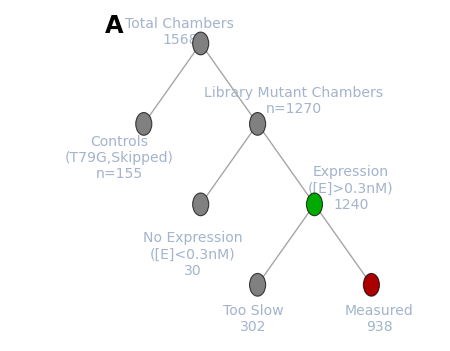

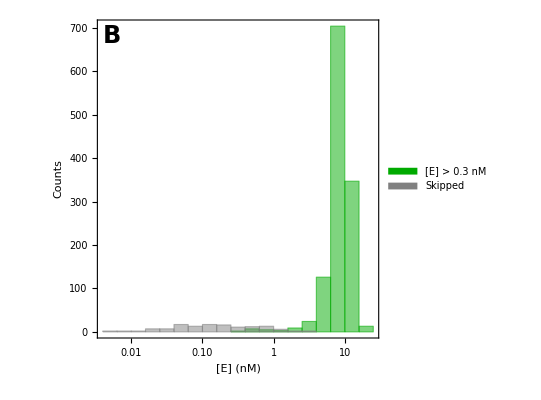

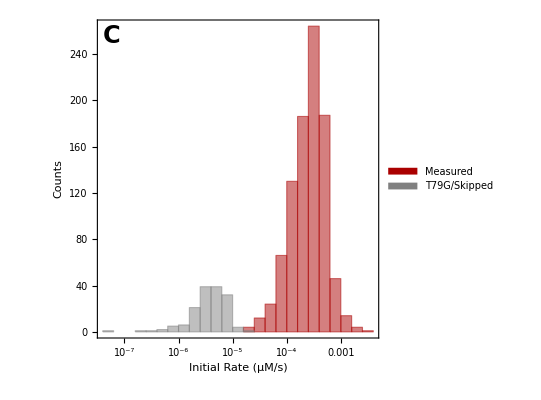

{{T517G,{1.67098,1.71267}},{T79S,{0.024822,0.0320797}},{T79S,{0.0434653,0.0859456}},{T79S,{0.0897216,0.139946}},{T79S,{0.0912403,0.0852351}}}

0.024822

{{T517G,{1.67098,1.71267}},{T79S,{0.024822,0.0320797}},{T79S,{0.0434653,0.0859456}},{T79S,{0.0897216,0.139946}},{T79S,{0.0912403,0.0852351}}}

{{T517G,{226588.,209931.}},{T79S,{2643.95,3696.61}},{T79S,{5701.28,17539.2}},{T79S,{17874.7,25088.2}},{T79S,{12985.7,13833.6}}}

{{T517G,{7.37456,8.15824}},{T79S,{9.38825,8.67815}},{T79S,{7.62378,4.9002}},{T79S,{5.01947,5.57814}},{T79S,{7.0262,6.16147}}}

-Graphics- | -Graphics- | -Graphics-
-Graphics- |  | 
Experimental Summary. A) Counts of local limit of quantification control chambers (skipped and catalytically unresolvable mutants), library and known active site mutant chambers (library mutants), chambers which expressed >0.3 nM, and measured and chambers that were not sufficiently above the local limit of quantification (too slow). B) Distribution of enzyme concentrations in chambers with [E]>0.3 nM compared to the measured expression in the Skipped chambers. C) Distribution of rates measured in the chambers sufficiently above the local limit of quantification (Measured) compared to the rates measured in the control chambers, at the highest substrate concentration. D) Correlation between k_cat/K_M replicate measurements for measured library mutants. |  |

/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/temporary_PDF_0000.pdf

```mathematica
Dynamic[n]

start=AbsoluteTime[];

dataset=ds5[Select[#ExpIndex==1&&#AssayType==1&]];

Length[dataset]

Print["Fitting standard curves..."]
ProgressIndicator[Dynamic[count],{1,1568}]

addStandardCurveFits=Dataset@Table[Association[{"Indices"->Normal[dataset[count,"Indices"]],"StdCurveFitObject"->fitStdCurveNew[ToExpression[Normal[dataset[count,"SC_Concentrations"]]],If[NumberQ[ToExpression[Normal[dataset[count,"SC_Median_Chamber"]]][[1]]],ToExpression[Normal[dataset[count,"SC_Median_Chamber"]]],Missing[]]]}],{count,1,1568}];

addStandardCurveFits2=addStandardCurveFits[All,Append[#,{"StdCurveSlope"->If[MissingQ[#StdCurveFitObject],Missing["Nonexistent"],#StdCurveFitObject["BestFitParameters"][[2]]],"StdCurveIntercept"->If[MissingQ[#StdCurveFitObject],Missing["Nonexistent"],#StdCurveFitObject["BestFitParameters"][[1]]],"StdCurveRSquared"->If[MissingQ[#StdCurveFitObject],Missing["Nonexistent"],#StdCurveFitObject["RSquared"]]}]&];

withStdCurveFits=Dataset[JoinAcross[Normal[ds4],Normal[addStandardCurveFits2],{"Indices"},"Left"]];
Print["Adding standard curve plots..."]
ProgressIndicator[Dynamic[count2],{1,1568}]

withStdCurveFitsTemp=withStdCurveFits[Select[#ExpIndex==1&&#AssayType==1&]];

addStandardCurvePlots=Table[Association[{"Indices"->Normal[withStdCurveFitsTemp[count2,"Indices"]],"StandardCurvePlot"->makeStdCurvePlotNew[withStdCurveFitsTemp[count2,"StdCurveSlope"],withStdCurveFitsTemp[count2,"StdCurveIntercept"],ToExpression[withStdCurveFitsTemp[count2,"SC_Concentrations"]],ToExpression[withStdCurveFitsTemp[count2,"SC_Median_Chamber"]]]}],{count2,1,1568}];

AbsoluteTime[]-start

withStdCurvePlot=Dataset[JoinAcross[Normal[withStdCurveFits],addStandardCurvePlots,{"Indices"},"Left"]];

AbsoluteTime[]-start
withProgressCurves=withStdCurvePlot[All,Append[#,"TurnoverTimepoints(uM)"->convertTouM[ToExpression[#MedianIntensities],#StdCurveSlope,#StdCurveIntercept]]&];
cmupData=SemanticImport[cmupAggregatePath];
cmupParams=cmupData[All,{"MutantID","kcatNormMedian","KMMedian","kcat/KMNormMedianLimit","kcat/KMAggLimit"}];
cmupGrouped=cmupParams[GroupBy["MutantID"]];
wtkcatKm=cmupGrouped["WT",1,"kcat/KMNormMedianLimit"]
wtkcat=cmupGrouped["WT",1,"kcatNormMedian"]
wtKm=cmupGrouped["WT",1,"KMMedian"]
cmupParamsForCalc=Dataset[Table[Association[{"MutantID"->cmupGrouped[mutant,1,"MutantID"],"kcat"->If[cmupGrouped[mutant,1,"kcat/KMAggLimit"]==0,Select[Normal[cmupGrouped[mutant,All,"kcatNormMedian"]],NumberQ[#]&][[1]],Median[Select[Normal[cmupGrouped[mutant,All,"kcat/KMNormMedianLimit"]],#>0&]]/wtkcatKm*wtkcat],"Km"->If[cmupGrouped[mutant,1,"kcat/KMAggLimit"]==0,Select[Normal[cmupGrouped[mutant,All,"KMMedian"]],NumberQ[#]&][[1]],wtKm],"kobs"->Select[Normal[cmupGrouped[mutant,All,"kcat/KMNormMedianLimit"]],NumberQ[#]&][[1]],"Limit"->cmupGrouped[mutant,1,"kcat/KMAggLimit"]}],{mutant,1,Length[cmupGrouped]}]][GroupBy["MutantID"]]
obsProgressCurve[times_,concentrations_]:=Module[{temp1,fullProgressCurve},

If[MissingQ[concentrations],Missing[],

temp1={Normal[times],Normal[concentrations]};

fullProgressCurve=Sort[Table[{temp1[[1,n]],temp1[[2,n]]},{n,1,Length[temp1[[1]]]}],#1[[1]]<#2[[1]]&]]

]

progressCurveLambertW[kcat_?NumberQ,KM_,enz_,substrate_,time_]:=(substrate-KM*LambertW[substrate/KM*Exp[(substrate-kcat*enz*time)/KM]])

maxExponent=Round[Log[10,$MaxMachineNumber]]+1;

fitRateSuperposition[mutant_,progresscurve_,enzymeconc_,mecmupConc_]:=Module[{},

If[MissingQ[progresscurve],Table[Missing[],{7}],

chamberTestPC2=progresscurve;

econc=enzymeconc/1000.0;

cmupkcat=cmupParamsForCalc[mutant,1,"kcat"];
cmupKm=cmupParamsForCalc[mutant,1,"Km"];

limitQ=cmupParamsForCalc[mutant,1,"Limit"];

baseline=Min[chamberTestPC2[[All,2]]];

(* if we don't have measurements for kcat and Km then can't fit the superposition function - in these cases defaulting to a fit using the points at t>2500s *)
basicFit=LinearModelFit[Select[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],#[[1]]≥2500.0&],x,x];

basicFitRate=basicFit[[1,2,2]];

basicFitIntercept=basicFit[[1,2,1]];

pcBaselineCorrected=Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}];

p=Graphics[{EdgeForm[{Black,Thickness[0.125]}],FaceForm[Directive[GrayLevel[0.5],Opacity[0.7]]],Disk[],Opacity[0.1]}];

(* also modifying to fit only rates - the testing above is fitting the MecMUP kcat/KM *)

Which[NumberQ[cmupkcat]&&limitQ≠-1,

fit=Quiet[NMinimize[{Sum[((chamberTestPC2[[n,2]]-baseline)-(progressCurveLambertW[cmupkcat,cmupKm,econc,cmup,chamberTestPC2[[n,1]]]+(rate)*chamberTestPC2[[n,1]]))^2,{n,1,Length[chamberTestPC2]}],rate>-0.05&&rate<0.05&&cmup>0.0&&cmup<(mecmupConc/1000.0)},{cmup,rate}]];

lastFivePointsForFlag=Table[{chamberTestPC2[[n,1]],progressCurveLambertW[cmupkcat,cmupKm,econc,mecmupConc/1000.0,chamberTestPC2[[n,1]]]},{n,1,Length[chamberTestPC2]}];

flagFit=LinearModelFit[Select[lastFivePointsForFlag,#[[1]]≥2500.0&],x,x];

{fit[[2,1,2]],fit[[2,2,2]],Show[Plot[progressCurveLambertW[cmupkcat,cmupKm,econc,fit[[2,1,2]],t]+fit[[2,2,2]]*t,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.2,If[Max[chamberTestPC2[[All,2]]]>5.0,Max[chamberTestPC2[[All,2]]]+Abs[Max[chamberTestPC2[[All,2]]]]*0.5,5.5]},AspectRatio->0.8,PlotStyle->Gray],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotMarkers->{p,0.05}],Plot[progressCurveLambertW[cmupkcat,cmupKm,econc,fit[[2,1,2]],t],{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Directive[Gray,Dashed]],ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[18,Black,FontFamily->"Arial"],Epilog->Inset[mutant<>"\n"<>ToString[NumberForm[Round[fit[[2,2,2]],0.0000001],ScientificNotationThreshold->{-maxExponent,maxExponent}]]<>"μM/s"<>"\n[cMUP]="<>ToString[Round[fit[[2,1,2]],0.01]]<>" μM",Scaled[{0.80,0.3}]]],Abs[flagFit[[1,2,2]]],(fit[[2,2,2]]-trueBackgroundRate)/Abs[flagFit[[1,2,2]]],Show[Plot[progressCurveLambertW[cmupkcat,cmupKm,econc,fit[[2,1,2]],t]+fit[[2,2,2]]*t,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Darker[Red]],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotStyle->Directive[PointSize[0.02],Darker[Red],Opacity[0.5]]],PlotRange->All,AspectRatio->0.8,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[Black,18,FontFamily->"Arial"]],pcBaselineCorrected},

NumberQ[cmupkcat]&&limitQ==-1,

lastFivePointsForFlag=Table[{chamberTestPC2[[n,1]],progressCurveLambertW[cmupkcat,cmupKm,econc,mecmupConc/1000.0,chamberTestPC2[[n,1]]]},{n,1,Length[chamberTestPC2]}];

flagFit=LinearModelFit[Select[lastFivePointsForFlag,#[[1]]≥2500.0&],x,x];

{Missing[],basicFitRate,Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{If[(Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1)>0,0,Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1],If[Max[chamberTestPC2[[All,2]]]>5.0,Max[chamberTestPC2[[All,2]]]+Abs[Max[chamberTestPC2[[All,2]]]]*0.5,5.5]},AspectRatio->0.8,PlotStyle->Gray],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotMarkers->{p,0.05}],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[18,Black,FontFamily->"Arial"],Epilog->Inset[mutant<>"\n"<>ToString[NumberForm[Round[basicFitRate,0.0000001],ScientificNotationThreshold->{-maxExponent,maxExponent}]]<>"μM/s",Scaled[{0.80,0.2}]]],Abs[flagFit[[1,2,2]]],(fit[[2,2,2]]-trueBackgroundRate)/Abs[flagFit[[1,2,2]]],Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Darker[Red]],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotStyle->Directive[PointSize[0.02],Darker[Red],Opacity[0.5]]],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[Black,18,FontFamily->"Arial"]],pcBaselineCorrected},

NumberQ[cmupkcat]==False,

{Missing[],basicFitRate,Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{If[(Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1)>0,0,Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1],If[Max[chamberTestPC2[[All,2]]]>5.0,Max[chamberTestPC2[[All,2]]]+Abs[Max[chamberTestPC2[[All,2]]]]*0.5,5.5]},AspectRatio->0.8,PlotStyle->Gray],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotMarkers->{p,0.05}],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[18,Black,FontFamily->"Arial"],Epilog->Inset[mutant<>"\n"<>ToString[NumberForm[Round[basicFitRate,0.0000001],ScientificNotationThreshold->{-maxExponent,maxExponent}]]<>"μM/s",Scaled[{0.80,0.2}]]],Missing[],Missing[],Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Darker[Red]],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotStyle->Directive[PointSize[0.02],Darker[Red],Opacity[0.5]]],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[Black,18,FontFamily->"Arial"]],pcBaselineCorrected}


]]

]
withProgressCurves2=withProgressCurves[All,Append[#,{"ProgressCurve"->obsProgressCurve[ToExpression[#Times],#["TurnoverTimepoints(uM)"]],"EnzymeConc"->(#eGFPSummedI/#eGFPSlope)}]&];
itr=0;

Dynamic[itr]

optDataPoints2=withProgressCurves2[All,Append[#,itrNew=itr+1;itr=itrNew;out=Quiet[fitRateSuperposition[#MutantID,#ProgressCurve,#EnzymeConc,#SubstrateConc]];{"OptLinFitSlope"->out[[2]],"OptLinFitSlopeMinusTrueBackground"->out[[2]]-trueBackgroundRate,"ContaminantConc"->out[[1]],"FitPlot"->out[[3]],"ContaminantRate"->out[[4]],"ContaminantRatio"->out[[5]],"BackgroundFitPlot"->out[[6]],"ProgressCurveBaselineCorrected"->out[[7]]}]&];
indices=Normal[optDataPoints2[Select[#ExpIndex==1&]][All,"Indices"]];
Length[indices]
Dynamic[ind]

nearestLocalBG=Table[Association["Indices"->indices[[ind]],"NearestLocalBackgroundChambers"->findNearestBackgroundChambers[optDataPoints2,indices[[ind]]]],{ind,1,Length[indices]}];
(*nearestBackgroundChambers=Import["/Users/craig/Dropbox/HTMEK_processing/current/per-experiment_QC/nearestLocalBackgroundChambers.wxf"];*)

(*nearestBackgroundChambers=Import["/Users/craig/Dropbox/HTMEK_processing/current/per-experiment_QC/nearestLocalBackgroundChambers_SlowestChip.wxf"];*)

withNearestChambers=Dataset[JoinAcross[Normal[optDataPoints2],nearestLocalBG,"Indices","Left"]];
start=AbsoluteTime[];

count2=0;
Dynamic[count]

withPCs2=withNearestChambers[All,Quiet[Append[#,(Clear[forSelect];count=count2+1;forSelect=#NearestLocalBackgroundChambers;sconc=#SubstrateConc;
expIndex=#ExpIndex;
indices=#Indices;count2=count;

If[MissingQ[#ProgressCurve],"ProgressCurveOptFit2"->Missing[],

bgProgressCurves=Normal[optDataPoints2[Select[MemberQ[forSelect,#Indices]&&#ExpIndex==expIndex&]][All,"FitPlot"]];

{"ProgressCurveOptFit2"->If[Length[bgProgressCurves]>0,Show[DeleteCases[DeleteCases[{#FitPlot,Normal[optDataPoints2[Select[MemberQ[forSelect,#Indices]&&#SubstrateConc==sconc&&#ExpIndex==expIndex&]][All,"BackgroundFitPlot"]]},Missing["Nonexistent"],Infinity],Missing[],Infinity],AspectRatio->0.8,ImageSize->400,AspectRatio->0.6,ImagePadding->{{75,2},{60,8}},Epilog->Inset[Style[ToString[Round[sconc]]<>" μM",16,Black,FontFamily->"Arial"],Scaled[{0.18,0.85}]]],Missing["Nonexistent"]]}]

)]&]];


(*{"ProgressCurveOptFit2"->If[Length[bgProgressCurves]>0,Show[DeleteCases[DeleteCases[{#FitPlot,Normal[optDataPoints2[Select[MemberQ[forSelect,#Indices]&&#SubstrateConc==sconc&&#ExpIndex==expIndex&]][All,"BackgroundFitPlot"]]},Missing["Nonexistent"],Infinity],Missing[]],AspectRatio->0.8,ImageSize->400,AspectRatio->0.6,ImagePadding->{{75,2},{60,8}},Epilog->Inset[Style[ToString[Round[sconc]]<>" μM",16,Black,FontFamily->"Arial"],Scaled[{0.18,0.85}]]],Missing["Nonexistent"]]}*)

AbsoluteTime[]-start
Dynamic[n]
Dynamic[column]

(*datasetIN=withPCs;*)

datasetIN=withPCs2;

inhibitorconcentrations=Normal[datasetIN[Select[#Indices=={1,1}&],"InhibitorConcentrations"]];
substrateconcentrations=Normal[datasetIN[Select[#Indices=={1,1}&],"SubstrateConc"]]
type=Normal[datasetIN[Select[#Indices=={1,1}&],"AssayType"]];

exptIndices=Normal[datasetIN[Select[#Indices=={1,1}&],"ExpIndex"]];

dataset2=datasetIN;

start=AbsoluteTime[];

interpolations=Flatten[Table[Association[{"x"->column,"ExpIndex"->exptIndices[[n]],"AssayType"->type[[n]],"Interpolation"->interpolateDeadMutantsPerColumn[mutantList,exptIndices[[n]],column,dataset2,"OptLinFitSlopeMinusTrueBackground"],"MutantsUsedForLocalBG"->mutantList}],{n,1,Length[substrateconcentrations]},{column,1,28}],1];

dataset3=Dataset[JoinAcross[Normal[dataset2],interpolations,{"x","ExpIndex","AssayType"},"Left"]];

AbsoluteTime[]-start
start=AbsoluteTime[];

dataset=dataset3;

temp=Values[Normal[dataset[All,{"Indices","ExpIndex","OptLinFitSlopeMinusTrueBackground","MutantID","Interpolation"}]]];

localBGs=Table[Association[{"Indices"->temp[[n,1]],"ExpIndex"->temp[[n,2]],"LocalBackgroundRatio"->If[MissingQ[temp[[n,3]]],Missing["Nonexistent"],(temp[[n,3]])/(temp[[n,5,temp[[n,1,2]]]])]}],{n,1,Length[temp]}];

withlocalBG=Dataset[JoinAcross[Normal[dataset],localBGs,{"Indices","ExpIndex"},"Left"]];

AbsoluteTime[]-start

Dynamic[n]

scaleEachAssay=0;

eGFPslope=withlocalBG[1,"eGFPSlope"];

start=AbsoluteTime[];

dataset2=withlocalBG;


boundingMutants={"WT","T79S"};

rateKey="OptLinFitSlopeMinusTrueBackground";

temp=dataset2[Select[#ExpIndex==whichExpt&],{"Indices","ExpIndex",rateKey,"MutantID","Interpolation"}];

upperBound=Mean[Select[Values[Normal[dataset2[Select[#MutantID==boundingMutants[[1]]&&#ExpIndex==whichExpt&&#eGFPSummedI>EcutoffForBG*eGFPslope&],{rateKey}]]],NumberQ[#[[1]]]==True&]][[1]];

lowerBound=Mean[Select[Values[Normal[dataset2[Select[#MutantID==boundingMutants[[2]]&&#ExpIndex==whichExpt&&#eGFPSummedI>EcutoffForBG*eGFPslope&],{rateKey}]]],NumberQ[#[[1]]]==True&]][[1]];

allinColumn=Join@@Flatten[Table[AssociationThread[Table[{column,row},{row,1,56}],Sort[Values[Normal[dataset2[Select[#Indices[[1]]==column&&#ExpIndex==whichExpt&],{"Indices",rateKey,"MutantID"}]]],#1[[1,2]]<#2[[1,2]]&]],{column,1,28}],2];

temp2=temp[All,Append[#,{"Indices"->Normal[#[[1]]],"MaxLocalBackgroundPlot"->generateLocalBGPlot[Normal[#["Indices"]],Normal[#["ExpIndex"]],Normal[#["Interpolation"]]]}]&];

withlocalBGPlots=Dataset[JoinAcross[Normal[dataset2],Normal[temp2],{"Indices"},"Left"]];

CloseKernels[];

LaunchKernels[4];

dataset=withlocalBGPlots;

len=1568;

numKernels=Length[Kernels[]]

chunksize=Round[len/numKernels];
firstChunks =Table[{(chunksize*(n-1))+1, n*chunksize}, {n, numKernels-1}];
intervals=Append[firstChunks, {(chunksize*(numKernels-1))+1, len}];

toCalculate=dataset[GroupBy["Indices"]];

chunked = toCalculate[[#[[1]];;#[[2]]]]&/@intervals;

flattened=Table[chunked[[n]][Catenate],{n,1,Length[chunked]}];

addedMMcalc=Join@@ParallelMap[Quiet[fitMichaelisMenten[#,"OptLinFitSlopeMinusTrueBackground","optlin",eGFPslope,scaleEachAssay]]&,flattened];

AbsoluteTime[]-start

CloseKernels[]
Dynamic[n]

grouped=addedMMcalc[GroupBy["Indices"]];

indicesOut=Values[#]&/@Values[Normal[grouped[All,1,{"MutantID","Indices","fit_mm_kcat","fit_mm_KM"}]]];

addkcatoverkm=Table[Association[{"MutantID"->indicesOut[[n,1]],"Indices"->indicesOut[[n,2]],"fit_mm_kcatoverKM_MMfit"->If[MissingQ[indicesOut[[n,3]]],Missing["Nonexistent"],indicesOut[[n,3]]/(indicesOut[[n,4]]*10^-6)]}],{n,1,1568}];

addedkcatoverkm=Dataset[JoinAcross[Normal[addedMMcalc],addkcatoverkm,"Indices","Left"]]//Quiet;


grouped=addedkcatoverkm[GroupBy["Indices"]];

indicesOut=Values[#]&/@Values[Normal[grouped[All,1,{"MutantID","Indices"}]]];

pGFP=Graphics[{EdgeForm[{Black,Thickness[0.125]}],FaceForm[Directive[Darker[Green],Opacity[0.7]]],Disk[],Opacity[0.1]}];

addedeGFPIntensityPlot=Table[Association[{"MutantID"->indicesOut[[n,1]],"Indices"->indicesOut[[n,2]],"eGFPIntensityPlot"->If[egfpSameFlag==0,ListPlot[Normal[grouped[n,All,"eGFPSummedI"]]/10^6,PlotRange->{0,Max[Normal[grouped[n,All,"eGFPSummedI"]]/10^6]*1.5},Frame->True,Axes->False,PlotMarkers->{pGFP,0.05},FrameStyle->Directive[20,Black,FontFamily->"Arial"],FrameLabel->{"Assay Number","eGFP Intensity (×10^6)"},ImagePadding->{{75,2},{65,5}},AspectRatio->0.8,ImageSize->400],ListPlot[{{1,Normal[grouped[n,1,"eGFPSummedI"]]/10^6}},PlotRange->{{0,Length[Normal[grouped[n,All,"eGFPSummedI"]]]},{0,Max[Normal[grouped[n,All,"eGFPSummedI"]]/10^6]*1.5}},Frame->True,Axes->False,PlotMarkers->{pGFP,0.05},GridLines->{None,{Normal[grouped[n,1,"eGFPSummedI"]]/10^6}},GridLinesStyle->Directive[Dashed,Darker[Green]],FrameStyle->Directive[20,Black,FontFamily->"Arial"],FrameLabel->{"Assay Number","eGFP Intensity (×10^6)"},ImagePadding->{{75,2},{65,5}},AspectRatio->0.8,ImageSize->400,FrameTicks->{{If[IntegerQ[#],#,N[#]]&/@FindDivisions[{0,Max[Normal[grouped[n,All,"eGFPSummedI"]]/10^6]},5],None},{If[IntegerQ[#],#,N[#]]&/@FindDivisions[{0,Length[Normal[grouped[n,All,"eGFPSummedI"]]]},Round[Length[Normal[grouped[n,All,"eGFPSummedI"]]]/2]],None}},Epilog->Inset[Style["eGFP measured\nbefore 1st assay only",14,Darker[Green]],Scaled[{0.7,0.3}]]]]}],{n,1,1568}];

addedeGFPIntensityPlotDataset=Dataset[JoinAcross[JoinAcross[Normal[addedkcatoverkm],addedeGFPIntensityPlot,"Indices","Left"],Normal[wxfForImageStamps[Select[#ExpIndex==1&],{"Indices","eGFPPostSDSImage"}]],"Indices","Left"]]//Quiet;

AbsoluteTime[]-start
normalizedDataset=Normal[addedeGFPIntensityPlotDataset];

replaced=Fold[Replace[#1,#2,Infinity]&,normalizedDataset,{_FittedModel->"NaN",_Graphics->"NaN",_Image->"NaN",_NonlinearModelFit->"NaN",_Times->"NaN",_Overlay->"NaN",_ReplaceAll->"NaN"}];

headers=Keys[replaced[[1]]];

(*values=Map[replaceBracketsBack,Values[replaced],{2}];*)

values=Values[replaced];

datasetForExport=Prepend[values,headers];

Export[StringJoin["~/Desktop/",addedkcatoverkm[1,"GlobalExperimentIndex"],"_MecMUP_LinComb.csv.bz2"],datasetForExport,"Data"];

(* summary table *)

fixLogPlots[gr_]:=gr/.f:(Charting`ScaledTicks|Charting`ScaledFrameTicks)[{Log,Exp}]:>(Part[#,;;, ;;3]&@*f);

p2=Graphics[{EdgeForm[{Black,Thickness[0.125]}],FaceForm[Directive[Gray,Opacity[0.7]]],Disk[],Opacity[0.1]}];

expressed=addedeGFPIntensityPlotDataset[Select[#ExpIndex==1&&#ManualGFPFlag==0&&#EnzymeConc>0.3&]];

Length[expressed]

skipped=addedeGFPIntensityPlotDataset[Select[#ExpIndex==1&&#ManualGFPFlag==0&&#MutantID=="Skipped"&]];

allLibraryChambers=addedeGFPIntensityPlotDataset[Select[#ExpIndex==1&&#MutantID≠"Skipped"&&#MutantID≠"T79G"&]];

expressedLibrary=allLibraryChambers[Select[#EnzymeConc>0.3&&#ManualGFPFlag==0&]];

Length[allLibraryChambers]
Length[expressedLibrary]

tooSlow=addedeGFPIntensityPlotDataset[Select[#ExpIndex==whichExpt&&#LocalBackgroundRatio≤5.0&&MemberQ[Normal[expressedLibrary[All,"Indices"]],#Indices]&]];

Length[tooSlow]

measured=addedeGFPIntensityPlotDataset[Select[#ExpIndex==whichExpt&&#LocalBackgroundRatio>5.0&&MemberQ[Normal[expressedLibrary[All,"Indices"]],#Indices]&]];

Length[measured]

countTree=TreePlot[{1->2,1->3,3->4,3->5,5->6,5->7},VertexSize->Medium,VertexCoordinates->{{0,0},{-1,-1},{1,-1},{0,-2},{2,-2},{1,-3},{3,-3}},EdgeStyle->Gray,Epilog->Inset[Style["A",24,Bold],Scaled[{0.0,1.0}]],VertexLabels->{1->Placed[Style["Total Chambers\n1568",14],{-0.8,1}],2->Placed[Style["Controls\n(T79G,Skipped)\nStyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[skipped]],14],{-1,-1}],3->Placed[Style["Library Mutant Chambers\nStyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[allLibraryChambers]],14],{2.75,1.5}],4->Placed[Style["No Expression\n([E]<0.3nM)\n"<>ToString[Length[allLibraryChambers]-Length[expressedLibrary]],14],{0,-1.7}],5->Placed[Style["Expression\n([E]>0.3nM)\n"<>ToString[Length[expressedLibrary]],14],{2.75,1.2}],7->Placed[Style["Measured\n"<>ToString[Length[measured]],14],{1,-1}],6->Placed[Style["Too Slow\n"<>ToString[Length[tooSlow]],14],{0.25,-1}]},ImageSize->450,VertexStyle->
Join[
{1->Gray}, 
#->Gray&/@{1,2,3,4,6},
#->Darker[Green]&/@{5},
#->Darker[Red]&/@{7}
]]

eConcHist=fixLogPlots@Histogram[{Normal[expressedLibrary[All,"EnzymeConc"]],Normal[skipped[All,"EnzymeConc"]]},"Log",ChartStyle->{Darker[Green],Gray},Frame->True,Axes->False,PlotRange->All,FrameStyle->Directive[20,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->400,FrameLabel->{Style["[E] (nM)",SingleLetterItalics->False],Style["Counts",SingleLetterItalics->False]},Epilog->{Inset[SwatchLegend[{Darker[Green],Gray},Style[#,16]&/@{"[E] > 0.3 nM","Skipped"}],Scaled[{0.25,0.9}]],Inset[Style["B",24,Bold],Scaled[{0.05,0.95}]]}]

rateHist=fixLogPlots@Histogram[{Normal[measured[All,"OptLinFitSlopeMinusTrueBackground"]],Normal[skipped[All,"OptLinFitSlopeMinusTrueBackground"]]},"Log",ChartStyle->{Darker[Red],Gray},Frame->True,Axes->False,PlotRange->All,FrameStyle->Directive[20,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->400,FrameLabel->{Style["Initial Rate (μM/s)",SingleLetterItalics->False],Style["Counts",SingleLetterItalics->False]},Epilog->{Inset[SwatchLegend[{Darker[Red],Gray},Style[#,16]&/@{"Measured","T79G/Skipped"}],Scaled[{0.8,0.9}]],Inset[Style["C",24,Bold],Scaled[{0.05,0.95}]]}]

measured2=measured;

measured3=measured2[All,{"MutantID","fit_mm_kcat"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured3[n,1,"MutantID"],#}&/@Partition[Normal[measured3[n,All,"fit_mm_kcat"]],2],{n,1,Length[measured3]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]]

measured2=measured[All,{"MutantID","fit_mm_kcat","fit_mm_KM","fit_mm_kcatoverKM_MMfit"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured2[n,1,"MutantID"],#}&/@Partition[Normal[measured2[n,All,"fit_mm_kcat"]],2],{n,1,Length[measured2]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]];

rmse=Sqrt[Mean[Table[(Log[10,pairs[[n,2,1]]]-Log[10,pairs[[n,2,2]]])^2,{n,1,Length[pairs]}]]];

pearsonR2=Correlation[Log[10,pairs[[All,2,1]]],Log[10,pairs[[All,2,2]]]]^2;

(*kcatplot=fixLogPlots@Show[ListLogLogPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[pairs[[n,2]],pairs[[n,1]]],pairs[[n,2]]],{n,1,Length[pairs]}],PlotRange->{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}},Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->500,PlotMarkers->{p2,0.02},FrameLabel->{"SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"] (rep.1) (/s)","SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"] (rep.2) (/s)"}],LogLogPlot[{x,x/2,x*2},{x,0.0001,10000},PlotStyle->Directive[Gray,Dashed]],ImagePadding->100];*)

kcatplot=Show[ListPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[Log[10,pairs[[n,2]]],pairs[[n,1]]],Log[10,pairs[[n,2]]]],{n,1,Length[pairs]}],PlotRange->Log[10,{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}}],Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->475,PlotMarkers->{p2,0.02},FrameLabel->{"Log10(SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]) (rep.1) (/s)","Log10(SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]) (rep.2) (/s)"},Epilog->{Inset[Style["SuperscriptBox[StyleBox[\"R\",FontSlant->\"Italic\"], \"2\"]="<>ToString[Round[pearsonR2,0.01]],14],Scaled[{0.2,0.9}]],Inset[Style["RMSE="<>ToString[Round[rmse,0.01]],14],Scaled[{0.2,0.8}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[pairs]],14],Scaled[{0.2,0.7}]],Inset[Style["D",24,Bold],Scaled[{0.05,0.95}]]}],Plot[{x,x-0.301,x+0.301},{x,-5,10},PlotStyle->Directive[Gray,Dashed]],ImagePadding->{{100,20},{100,50}}];

measured2=measured[All,{"MutantID","fit_mm_KM"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured2[n,1,"MutantID"],#}&/@Partition[Normal[measured2[n,All,"fit_mm_KM"]],2],{n,1,Length[measured2]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]];

rmse=Sqrt[Mean[Table[(Log[10,pairs[[n,2,1]]]-Log[10,pairs[[n,2,2]]])^2,{n,1,Length[pairs]}]]];

pearsonR2=Correlation[Log[10,pairs[[All,2,1]]],Log[10,pairs[[All,2,2]]]]^2;

KmPlot=Show[ListPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[Log[10,pairs[[n,2]]],pairs[[n,1]]],Log[10,pairs[[n,2]]]],{n,1,Length[pairs]}],PlotRange->Log[10,{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}}],Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->475,PlotMarkers->{p2,0.02},FrameLabel->{Style["Log[10,SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.1) (/s)",SingleLetterItalics->False],Style["Log[10,SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.2) (/s)",SingleLetterItalics->False]},Epilog->{Inset[Style["SuperscriptBox[StyleBox[\"R\",FontSlant->\"Italic\"], \"2\"]="<>ToString[Round[pearsonR2,0.01]],14],Scaled[{0.2,0.9}]],Inset[Style["RMSE="<>ToString[Round[rmse,0.01]],14],Scaled[{0.2,0.8}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[pairs]],14],Scaled[{0.2,0.7}]],Inset[Style["E",24,Bold],Scaled[{0.05,0.95}]]}],Plot[{x,x-0.301,x+0.301},{x,-5,10},PlotStyle->Directive[Gray,Dashed]],Plot[10,{x,-5,Log[10,0.5]},Filling->-5,FillingStyle->Directive[LightPink,Opacity[0.5]],PlotStyle->Directive[LightPink,Opacity[0.8]]],ImagePadding->{{100,20},{100,50}}];

measured2=measured[All,{"MutantID","fit_mm_kcatoverKM_MMfit"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured2[n,1,"MutantID"],#}&/@Partition[Normal[measured2[n,All,"fit_mm_kcatoverKM_MMfit"]],2],{n,1,Length[measured2]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]];

rmse=Sqrt[Mean[Table[(Log[10,pairs[[n,2,1]]]-Log[10,pairs[[n,2,2]]])^2,{n,1,Length[pairs]}]]];

pearsonR2=Correlation[Log[10,pairs[[All,2,1]]],Log[10,pairs[[All,2,2]]]]^2;

kcatKMplot=Show[ListPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[Log[10,pairs[[n,2]]],pairs[[n,1]]],Log[10,pairs[[n,2]]]],{n,1,Length[pairs]}],PlotRange->Log[10,{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}}],Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->475,PlotMarkers->{p2,0.02},FrameLabel->{Style["Log[10,SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]/SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.1) (/M /s)",SingleLetterItalics->False],Style["Log[10,SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]/SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.2) (/M /s)",SingleLetterItalics->False]},Epilog->{Inset[Style["SuperscriptBox[StyleBox[\"R\",FontSlant->\"Italic\"], \"2\"]="<>ToString[Round[pearsonR2,0.01]],14],Scaled[{0.2,0.9}]],Inset[Style["RMSE="<>ToString[Round[rmse,0.01]],14],Scaled[{0.2,0.8}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[pairs]],14],Scaled[{0.2,0.7}]],Inset[Style["F",24,Bold],Scaled[{0.05,0.95}]]}],Plot[{x,x-0.301,x+0.301},{x,-5,10},PlotStyle->Directive[Gray,Dashed]],ImagePadding->{{100,20},{100,50}}];

(*Grid[{{countTree,kcatplot},{eConcHist,KmPlot},{rateHist,kcatKMplot}}]*)

summaryGrid=Grid[{{countTree,eConcHist,rateHist},{kcatKMplot},{Style["Experimental Summary. A) Counts of local limit of quantification control chambers (skipped and catalytically unresolvable mutants), library and known active site mutant chambers (library mutants), chambers which expressed >0.3 nM, and measured and chambers that were not sufficiently above the local limit of quantification (too slow). B) Distribution of enzyme concentrations in chambers with [E]>0.3 nM compared to the measured expression in the Skipped chambers. C) Distribution of rates measured in the chambers sufficiently above the local limit of quantification (Measured) compared to the rates measured in the control chambers, at the highest substrate concentration. D) Correlation between SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]/SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"] replicate measurements for measured library mutants.",18,FontFamily->"Arial",TextAlignment->Left,SingleLetterItalics->False],SpanFromLeft}}]

Export[StringJoin["/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/temporary_PDF_","0000",".pdf"],summaryGrid,"AllowRasterization"->False]
```

```mathematica
dataset=addedeGFPIntensityPlotDataset;

indices=Sort[Normal[DeleteDuplicates[dataset[[All,"Indices"]]]]];

Do[

(* change 3rd argument to correspond to type of assay: cMUP, MeP, MecMUP, Inhibition *)
(* added 4th argument "unscaled" *)
out=makeGridMecMUP[dataset,indices[[n]],"MecMUP","unscaled"];

Export[StringJoin["/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/temporary_PDF_",StringPadLeft[ToString[n],4,"0"],".pdf"],out,"AllowRasterization"->False];

,{n,1,1568}];

session = StartExternalSession[<|"System"->"Python","Version"->"3.6", "SessionProlog"->{"import os", "from PyPDF2 import PdfFileMerger, PdfFileReader"}|>];

defineRoot = "root='/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/'";
getNames = "pdfs1=[os.path.join(root, dir) for dir in os.listdir(root) if '.pdf' in dir]";
getNames2="pdfs=sorted(pdfs1)";
createMerger = "merger = PdfFileMerger()";
executeMerge = "for pdf in pdfs: merger.append(PdfFileReader(pdf,'rb'))";
executeExport = StringJoin["merger.write('/Users/craig/Desktop/",Values[Normal[dataset[1,{"GlobalExperimentIndex"}]]][[1]],".pdf')"];
completionNotice = "print('PDF Concatenation Complete')";

ExternalEvaluate[session,{defineRoot, getNames,getNames2, createMerger, executeMerge, executeExport, completionNotice}];
```

PDF Concatenation Complete

#### Dataset 6

```mathematica
dataset=remapNames[generateDatasetFromCSV[Import["/Users/craig/Dropbox/HTMEK_processing/MecMUP_QC_200220/180402_S3_d2_MecMUP_1_MecMUP_LinComb.csv.bz2"],"GlyScan","180402_S3_d2_MecMUP_1_MecMUP_LinComb"]];

wxfForImageStamps=Import["/Users/craig/Desktop/180402_S3_d2_MecMUP_1_newLBR.wxf"];

dataset[1;;2]
```

```mathematica
keysToKeep={"GlobalExperimentIndex","Date","Experiment","Setup","Device","PhosphateSensorConc","eGFPSlope","x","y","median_chamber","sum_chamber","std_chamber","x_center_chamber","y_center_chamber","radius_chamber","xslice","yslice","MutantID","time_s","median_button_Button_Quant","summed_button_Button_Quant","eGFPSummedI","std_button_Button_Quant","x_button_center_Button_Quant","y_button_center_Button_Quant","radius_button_disk_Button_Quant","median_button_annulus_Button_Quant","summed_button_annulus_normed_Button_Quant","std_button_annulus_localBG_Button_Quant","inner_radius_button_annulus_Button_Quant","outer_radius_button_annulus_Button_Quant","xslice_Button_Quant","yslice_Button_Quant","MutantID_Button_Quant","series_index","Times","MedianIntensities","ExpIndex","AssayType","SubstrateConc","InhibitorConcentrations","Zn2+","SC_Concentrations","SC_Median_Chamber","SC_Median_Chamber","ManualGFPFlag","Indices"};
ds2=dataset[All,Append[#,{"Indices2"->ToExpression[#Indices]}]&];

ds3=ds2[All,{"GlobalExperimentIndex","Date","Experiment","Setup","Device","PhosphateSensorConc","eGFPSlope","x","y","median_chamber","sum_chamber","std_chamber","x_center_chamber","y_center_chamber","radius_chamber","xslice","yslice","MutantID","time_s","median_button_Button_Quant","summed_button_Button_Quant","eGFPSummedI","std_button_Button_Quant","x_button_center_Button_Quant","y_button_center_Button_Quant","radius_button_disk_Button_Quant","median_button_annulus_Button_Quant","summed_button_annulus_normed_Button_Quant","std_button_annulus_localBG_Button_Quant","inner_radius_button_annulus_Button_Quant","outer_radius_button_annulus_Button_Quant","xslice_Button_Quant","yslice_Button_Quant","MutantID_Button_Quant","series_index","Times","MedianIntensities","ExpIndex","AssayType","SubstrateConc","InhibitorConcentrations","Zn2+","SC_Concentrations","SC_Median_Chamber","SC_Median_Chamber","ManualGFPFlag","Indices2"}];

ds4=ds3[All,Append[#,"Indices"->#Indices2]&][All,keysToKeep];

ds4[GroupBy["Indices"]][1;;2,All,"eGFPSummedI"]
ds4[GroupBy["Indices"]][1;;2,All,"SubstrateConc"]
egfpSameFlag=0;
ds5=ds4[All,Append[#,"eGFPConstant"->egfpSameFlag]&];
```

```mathematica
mutantList={"T79G","Skipped"};

whichExpt=5;

EcutoffForBG=0.3;

trueBackgroundRate=-2.3 10^-6;
```

1568

Fitting standard curves...

Adding standard curve plots...

55.171435

56.342195

1.4213×10^6

121.236

85.3261

Dataset[<>]

General::readp: Symbol None is read-protected.

General::stop: Further output of General::readp will be suppressed during this calculation.

1568

General::readp: Symbol None is read-protected.

General::stop: Further output of General::readp will be suppressed during this calculation.

384.268156

{500.,1000.,1000.,1500.,2000.}

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

20.75434

10.46596

4

238.18435

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

323.7055

1462

1400

1331

362

969

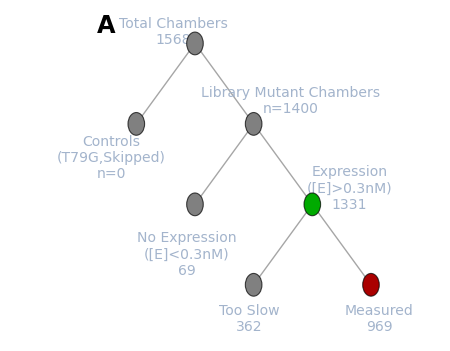

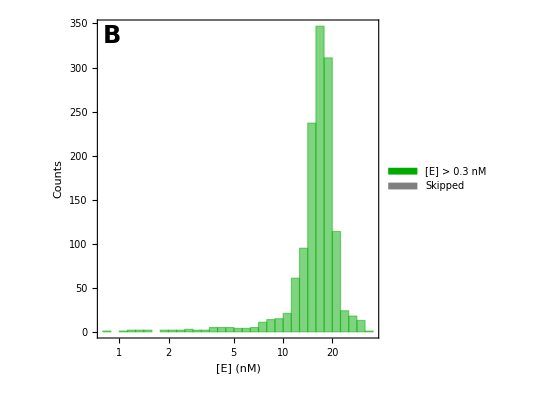

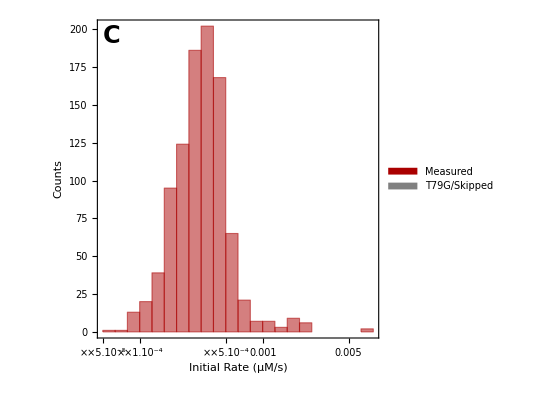

{{H515V,{1.64904,1.21982}},{D375V,{1.77969,1.07152}},{E449V,{1.96838,0.14532}},{M398V,{2.02786,0.722201}},{R463V,{0.0291067,0.683728}}}

0.0105836

{{H515V,{1.64904,1.21982}},{D375V,{1.77969,1.07152}},{E449V,{1.96838,0.14532}},{M398V,{2.02786,0.722201}},{R463V,{0.0291067,0.683728}}}

{{H515V,{190955.,109609.}},{D375V,{209905.,130504.}},{E449V,{214959.,12639.3}},{M398V,{224374.,75750.9}},{R463V,{4566.39,253650.}}}

{{H515V,{8.63572,11.1288}},{D375V,{8.47853,8.21064}},{E449V,{9.15701,11.4974}},{M398V,{9.03785,9.53389}},{R463V,{6.37411,2.69556}}}

-Graphics- | -Graphics- | -Graphics-
-Graphics- |  | 
Experimental Summary. A) Counts of local limit of quantification control chambers (skipped and catalytically unresolvable mutants), library and known active site mutant chambers (library mutants), chambers which expressed >0.3 nM, and measured and chambers that were not sufficiently above the local limit of quantification (too slow). B) Distribution of enzyme concentrations in chambers with [E]>0.3 nM compared to the measured expression in the Skipped chambers. C) Distribution of rates measured in the chambers sufficiently above the local limit of quantification (Measured) compared to the rates measured in the control chambers, at the highest substrate concentration. D) Correlation between k_cat/K_M replicate measurements for measured library mutants. |  |

/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/temporary_PDF_0000.pdf

```mathematica
Dynamic[n]

start=AbsoluteTime[];

dataset=ds5[Select[#ExpIndex==1&&#AssayType==1&]];

Length[dataset]

Print["Fitting standard curves..."]
ProgressIndicator[Dynamic[count],{1,1568}]

addStandardCurveFits=Dataset@Table[Association[{"Indices"->Normal[dataset[count,"Indices"]],"StdCurveFitObject"->fitStdCurveNew[ToExpression[Normal[dataset[count,"SC_Concentrations"]]],If[NumberQ[ToExpression[Normal[dataset[count,"SC_Median_Chamber"]]][[1]]],ToExpression[Normal[dataset[count,"SC_Median_Chamber"]]],Missing[]]]}],{count,1,1568}];

addStandardCurveFits2=addStandardCurveFits[All,Append[#,{"StdCurveSlope"->If[MissingQ[#StdCurveFitObject],Missing["Nonexistent"],#StdCurveFitObject["BestFitParameters"][[2]]],"StdCurveIntercept"->If[MissingQ[#StdCurveFitObject],Missing["Nonexistent"],#StdCurveFitObject["BestFitParameters"][[1]]],"StdCurveRSquared"->If[MissingQ[#StdCurveFitObject],Missing["Nonexistent"],#StdCurveFitObject["RSquared"]]}]&];

withStdCurveFits=Dataset[JoinAcross[Normal[ds4],Normal[addStandardCurveFits2],{"Indices"},"Left"]];
Print["Adding standard curve plots..."]
ProgressIndicator[Dynamic[count2],{1,1568}]

withStdCurveFitsTemp=withStdCurveFits[Select[#ExpIndex==1&&#AssayType==1&]];

addStandardCurvePlots=Table[Association[{"Indices"->Normal[withStdCurveFitsTemp[count2,"Indices"]],"StandardCurvePlot"->makeStdCurvePlotNew[withStdCurveFitsTemp[count2,"StdCurveSlope"],withStdCurveFitsTemp[count2,"StdCurveIntercept"],ToExpression[withStdCurveFitsTemp[count2,"SC_Concentrations"]],ToExpression[withStdCurveFitsTemp[count2,"SC_Median_Chamber"]]]}],{count2,1,1568}];

AbsoluteTime[]-start

withStdCurvePlot=Dataset[JoinAcross[Normal[withStdCurveFits],addStandardCurvePlots,{"Indices"},"Left"]];

AbsoluteTime[]-start
withProgressCurves=withStdCurvePlot[All,Append[#,"TurnoverTimepoints(uM)"->convertTouM[ToExpression[#MedianIntensities],#StdCurveSlope,#StdCurveIntercept]]&];
cmupData=SemanticImport[cmupAggregatePath];
cmupParams=cmupData[All,{"MutantID","kcatNormMedian","KMMedian","kcat/KMNormMedianLimit","kcat/KMAggLimit"}];
cmupGrouped=cmupParams[GroupBy["MutantID"]];
wtkcatKm=cmupGrouped["WT",1,"kcat/KMNormMedianLimit"]
wtkcat=cmupGrouped["WT",1,"kcatNormMedian"]
wtKm=cmupGrouped["WT",1,"KMMedian"]
cmupParamsForCalc=Dataset[Table[Association[{"MutantID"->cmupGrouped[mutant,1,"MutantID"],"kcat"->If[cmupGrouped[mutant,1,"kcat/KMAggLimit"]==0,Select[Normal[cmupGrouped[mutant,All,"kcatNormMedian"]],NumberQ[#]&][[1]],Median[Select[Normal[cmupGrouped[mutant,All,"kcat/KMNormMedianLimit"]],#>0&]]/wtkcatKm*wtkcat],"Km"->If[cmupGrouped[mutant,1,"kcat/KMAggLimit"]==0,Select[Normal[cmupGrouped[mutant,All,"KMMedian"]],NumberQ[#]&][[1]],wtKm],"kobs"->Select[Normal[cmupGrouped[mutant,All,"kcat/KMNormMedianLimit"]],NumberQ[#]&][[1]],"Limit"->cmupGrouped[mutant,1,"kcat/KMAggLimit"]}],{mutant,1,Length[cmupGrouped]}]][GroupBy["MutantID"]]
obsProgressCurve[times_,concentrations_]:=Module[{temp1,fullProgressCurve},

If[MissingQ[concentrations],Missing[],

temp1={Normal[times],Normal[concentrations]};

fullProgressCurve=Sort[Table[{temp1[[1,n]],temp1[[2,n]]},{n,1,Length[temp1[[1]]]}],#1[[1]]<#2[[1]]&]]

]

progressCurveLambertW[kcat_?NumberQ,KM_,enz_,substrate_,time_]:=(substrate-KM*LambertW[substrate/KM*Exp[(substrate-kcat*enz*time)/KM]])

maxExponent=Round[Log[10,$MaxMachineNumber]]+1;

fitRateSuperposition[mutant_,progresscurve_,enzymeconc_,mecmupConc_]:=Module[{},

If[MissingQ[progresscurve],Table[Missing[],{7}],

chamberTestPC2=progresscurve;

econc=enzymeconc/1000.0;

cmupkcat=cmupParamsForCalc[mutant,1,"kcat"];
cmupKm=cmupParamsForCalc[mutant,1,"Km"];

limitQ=cmupParamsForCalc[mutant,1,"Limit"];

baseline=Min[chamberTestPC2[[All,2]]];

(* if we don't have measurements for kcat and Km then can't fit the superposition function - in these cases defaulting to a fit using the points at t>2500s *)
basicFit=LinearModelFit[Select[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],#[[1]]≥2500.0&],x,x];

basicFitRate=basicFit[[1,2,2]];

basicFitIntercept=basicFit[[1,2,1]];

pcBaselineCorrected=Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}];

p=Graphics[{EdgeForm[{Black,Thickness[0.125]}],FaceForm[Directive[GrayLevel[0.5],Opacity[0.7]]],Disk[],Opacity[0.1]}];

(* also modifying to fit only rates - the testing above is fitting the MecMUP kcat/KM *)

Which[NumberQ[cmupkcat]&&limitQ≠-1,

fit=Quiet[NMinimize[{Sum[((chamberTestPC2[[n,2]]-baseline)-(progressCurveLambertW[cmupkcat,cmupKm,econc,cmup,chamberTestPC2[[n,1]]]+(rate)*chamberTestPC2[[n,1]]))^2,{n,1,Length[chamberTestPC2]}],rate>-0.05&&rate<0.05&&cmup>0.0&&cmup<(mecmupConc/1000.0)},{cmup,rate}]];

lastFivePointsForFlag=Table[{chamberTestPC2[[n,1]],progressCurveLambertW[cmupkcat,cmupKm,econc,mecmupConc/1000.0,chamberTestPC2[[n,1]]]},{n,1,Length[chamberTestPC2]}];

flagFit=LinearModelFit[Select[lastFivePointsForFlag,#[[1]]≥2500.0&],x,x];

{fit[[2,1,2]],fit[[2,2,2]],Show[Plot[progressCurveLambertW[cmupkcat,cmupKm,econc,fit[[2,1,2]],t]+fit[[2,2,2]]*t,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.2,If[Max[chamberTestPC2[[All,2]]]>5.0,Max[chamberTestPC2[[All,2]]]+Abs[Max[chamberTestPC2[[All,2]]]]*0.5,5.5]},AspectRatio->0.8,PlotStyle->Gray],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotMarkers->{p,0.05}],Plot[progressCurveLambertW[cmupkcat,cmupKm,econc,fit[[2,1,2]],t],{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Directive[Gray,Dashed]],ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[18,Black,FontFamily->"Arial"],Epilog->Inset[mutant<>"\n"<>ToString[NumberForm[Round[fit[[2,2,2]],0.0000001],ScientificNotationThreshold->{-maxExponent,maxExponent}]]<>"μM/s"<>"\n[cMUP]="<>ToString[Round[fit[[2,1,2]],0.01]]<>" μM",Scaled[{0.80,0.3}]]],Abs[flagFit[[1,2,2]]],(fit[[2,2,2]]-trueBackgroundRate)/Abs[flagFit[[1,2,2]]],Show[Plot[progressCurveLambertW[cmupkcat,cmupKm,econc,fit[[2,1,2]],t]+fit[[2,2,2]]*t,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Darker[Red]],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotStyle->Directive[PointSize[0.02],Darker[Red],Opacity[0.5]]],PlotRange->All,AspectRatio->0.8,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[Black,18,FontFamily->"Arial"]],pcBaselineCorrected},

NumberQ[cmupkcat]&&limitQ==-1,

lastFivePointsForFlag=Table[{chamberTestPC2[[n,1]],progressCurveLambertW[cmupkcat,cmupKm,econc,mecmupConc/1000.0,chamberTestPC2[[n,1]]]},{n,1,Length[chamberTestPC2]}];

flagFit=LinearModelFit[Select[lastFivePointsForFlag,#[[1]]≥2500.0&],x,x];

{Missing[],basicFitRate,Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{If[(Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1)>0,0,Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1],If[Max[chamberTestPC2[[All,2]]]>5.0,Max[chamberTestPC2[[All,2]]]+Abs[Max[chamberTestPC2[[All,2]]]]*0.5,5.5]},AspectRatio->0.8,PlotStyle->Gray],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotMarkers->{p,0.05}],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[18,Black,FontFamily->"Arial"],Epilog->Inset[mutant<>"\n"<>ToString[NumberForm[Round[basicFitRate,0.0000001],ScientificNotationThreshold->{-maxExponent,maxExponent}]]<>"μM/s",Scaled[{0.80,0.2}]]],Abs[flagFit[[1,2,2]]],(fit[[2,2,2]]-trueBackgroundRate)/Abs[flagFit[[1,2,2]]],Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Darker[Red]],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotStyle->Directive[PointSize[0.02],Darker[Red],Opacity[0.5]]],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[Black,18,FontFamily->"Arial"]],pcBaselineCorrected},

NumberQ[cmupkcat]==False,

{Missing[],basicFitRate,Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{If[(Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1)>0,0,Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1],If[Max[chamberTestPC2[[All,2]]]>5.0,Max[chamberTestPC2[[All,2]]]+Abs[Max[chamberTestPC2[[All,2]]]]*0.5,5.5]},AspectRatio->0.8,PlotStyle->Gray],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotMarkers->{p,0.05}],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[18,Black,FontFamily->"Arial"],Epilog->Inset[mutant<>"\n"<>ToString[NumberForm[Round[basicFitRate,0.0000001],ScientificNotationThreshold->{-maxExponent,maxExponent}]]<>"μM/s",Scaled[{0.80,0.2}]]],Missing[],Missing[],Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Darker[Red]],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotStyle->Directive[PointSize[0.02],Darker[Red],Opacity[0.5]]],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[Black,18,FontFamily->"Arial"]],pcBaselineCorrected}


]]

]
withProgressCurves2=withProgressCurves[All,Append[#,{"ProgressCurve"->obsProgressCurve[ToExpression[#Times],#["TurnoverTimepoints(uM)"]],"EnzymeConc"->(#eGFPSummedI/#eGFPSlope)}]&];
itr=0;

Dynamic[itr]

optDataPoints2=withProgressCurves2[All,Append[#,itrNew=itr+1;itr=itrNew;out=Quiet[fitRateSuperposition[#MutantID,#ProgressCurve,#EnzymeConc,#SubstrateConc]];{"OptLinFitSlope"->out[[2]],"OptLinFitSlopeMinusTrueBackground"->out[[2]]-trueBackgroundRate,"ContaminantConc"->out[[1]],"FitPlot"->out[[3]],"ContaminantRate"->out[[4]],"ContaminantRatio"->out[[5]],"BackgroundFitPlot"->out[[6]],"ProgressCurveBaselineCorrected"->out[[7]]}]&];
indices=Normal[optDataPoints2[Select[#ExpIndex==1&]][All,"Indices"]];
Length[indices]
Dynamic[ind]

nearestLocalBG=Table[Association["Indices"->indices[[ind]],"NearestLocalBackgroundChambers"->findNearestBackgroundChambers[optDataPoints2,indices[[ind]]]],{ind,1,Length[indices]}];
(*nearestBackgroundChambers=Import["/Users/craig/Dropbox/HTMEK_processing/current/per-experiment_QC/nearestLocalBackgroundChambers.wxf"];*)

(*nearestBackgroundChambers=Import["/Users/craig/Dropbox/HTMEK_processing/current/per-experiment_QC/nearestLocalBackgroundChambers_SlowestChip.wxf"];*)

withNearestChambers=Dataset[JoinAcross[Normal[optDataPoints2],nearestLocalBG,"Indices","Left"]];
start=AbsoluteTime[];

count2=0;
Dynamic[count]

withPCs2=withNearestChambers[All,Quiet[Append[#,(Clear[forSelect];count=count2+1;forSelect=#NearestLocalBackgroundChambers;sconc=#SubstrateConc;
expIndex=#ExpIndex;
indices=#Indices;count2=count;

If[MissingQ[#ProgressCurve],"ProgressCurveOptFit2"->Missing[],

bgProgressCurves=Normal[optDataPoints2[Select[MemberQ[forSelect,#Indices]&&#ExpIndex==expIndex&]][All,"FitPlot"]];

{"ProgressCurveOptFit2"->If[Length[bgProgressCurves]>0,Show[DeleteCases[DeleteCases[{#FitPlot,Normal[optDataPoints2[Select[MemberQ[forSelect,#Indices]&&#SubstrateConc==sconc&&#ExpIndex==expIndex&]][All,"BackgroundFitPlot"]]},Missing["Nonexistent"],Infinity],Missing[],Infinity],AspectRatio->0.8,ImageSize->400,AspectRatio->0.6,ImagePadding->{{75,2},{60,8}},Epilog->Inset[Style[ToString[Round[sconc]]<>" μM",16,Black,FontFamily->"Arial"],Scaled[{0.18,0.85}]]],Missing["Nonexistent"]]}]

)]&]];


(*{"ProgressCurveOptFit2"->If[Length[bgProgressCurves]>0,Show[DeleteCases[DeleteCases[{#FitPlot,Normal[optDataPoints2[Select[MemberQ[forSelect,#Indices]&&#SubstrateConc==sconc&&#ExpIndex==expIndex&]][All,"BackgroundFitPlot"]]},Missing["Nonexistent"],Infinity],Missing[]],AspectRatio->0.8,ImageSize->400,AspectRatio->0.6,ImagePadding->{{75,2},{60,8}},Epilog->Inset[Style[ToString[Round[sconc]]<>" μM",16,Black,FontFamily->"Arial"],Scaled[{0.18,0.85}]]],Missing["Nonexistent"]]}*)

AbsoluteTime[]-start
Dynamic[n]
Dynamic[column]

(*datasetIN=withPCs;*)

datasetIN=withPCs2;

inhibitorconcentrations=Normal[datasetIN[Select[#Indices=={1,1}&],"InhibitorConcentrations"]];
substrateconcentrations=Normal[datasetIN[Select[#Indices=={1,1}&],"SubstrateConc"]]
type=Normal[datasetIN[Select[#Indices=={1,1}&],"AssayType"]];

exptIndices=Normal[datasetIN[Select[#Indices=={1,1}&],"ExpIndex"]];

dataset2=datasetIN;

start=AbsoluteTime[];

interpolations=Flatten[Table[Association[{"x"->column,"ExpIndex"->exptIndices[[n]],"AssayType"->type[[n]],"Interpolation"->interpolateDeadMutantsPerColumn[mutantList,exptIndices[[n]],column,dataset2,"OptLinFitSlopeMinusTrueBackground"],"MutantsUsedForLocalBG"->mutantList}],{n,1,Length[substrateconcentrations]},{column,1,28}],1];

dataset3=Dataset[JoinAcross[Normal[dataset2],interpolations,{"x","ExpIndex","AssayType"},"Left"]];

AbsoluteTime[]-start
start=AbsoluteTime[];

dataset=dataset3;

temp=Values[Normal[dataset[All,{"Indices","ExpIndex","OptLinFitSlopeMinusTrueBackground","MutantID","Interpolation"}]]];

localBGs=Table[Association[{"Indices"->temp[[n,1]],"ExpIndex"->temp[[n,2]],"LocalBackgroundRatio"->If[MissingQ[temp[[n,3]]],Missing["Nonexistent"],(temp[[n,3]])/(temp[[n,5,temp[[n,1,2]]]])]}],{n,1,Length[temp]}];

withlocalBG=Dataset[JoinAcross[Normal[dataset],localBGs,{"Indices","ExpIndex"},"Left"]];

AbsoluteTime[]-start

Dynamic[n]

scaleEachAssay=0;

eGFPslope=withlocalBG[1,"eGFPSlope"];

start=AbsoluteTime[];

dataset2=withlocalBG;


boundingMutants={"WT","T79S"};

rateKey="OptLinFitSlopeMinusTrueBackground";

temp=dataset2[Select[#ExpIndex==whichExpt&],{"Indices","ExpIndex",rateKey,"MutantID","Interpolation"}];

upperBound=Mean[Select[Values[Normal[dataset2[Select[#MutantID==boundingMutants[[1]]&&#ExpIndex==whichExpt&&#eGFPSummedI>EcutoffForBG*eGFPslope&],{rateKey}]]],NumberQ[#[[1]]]==True&]][[1]];

lowerBound=Mean[Select[Values[Normal[dataset2[Select[#MutantID==boundingMutants[[2]]&&#ExpIndex==whichExpt&&#eGFPSummedI>EcutoffForBG*eGFPslope&],{rateKey}]]],NumberQ[#[[1]]]==True&]][[1]];

allinColumn=Join@@Flatten[Table[AssociationThread[Table[{column,row},{row,1,56}],Sort[Values[Normal[dataset2[Select[#Indices[[1]]==column&&#ExpIndex==whichExpt&],{"Indices",rateKey,"MutantID"}]]],#1[[1,2]]<#2[[1,2]]&]],{column,1,28}],2];

temp2=temp[All,Append[#,{"Indices"->Normal[#[[1]]],"MaxLocalBackgroundPlot"->generateLocalBGPlot[Normal[#["Indices"]],Normal[#["ExpIndex"]],Normal[#["Interpolation"]]]}]&];

withlocalBGPlots=Dataset[JoinAcross[Normal[dataset2],Normal[temp2],{"Indices"},"Left"]];

CloseKernels[];

LaunchKernels[4];

dataset=withlocalBGPlots;

len=1568;

numKernels=Length[Kernels[]]

chunksize=Round[len/numKernels];
firstChunks =Table[{(chunksize*(n-1))+1, n*chunksize}, {n, numKernels-1}];
intervals=Append[firstChunks, {(chunksize*(numKernels-1))+1, len}];

toCalculate=dataset[GroupBy["Indices"]];

chunked = toCalculate[[#[[1]];;#[[2]]]]&/@intervals;

flattened=Table[chunked[[n]][Catenate],{n,1,Length[chunked]}];

addedMMcalc=Join@@ParallelMap[Quiet[fitMichaelisMenten[#,"OptLinFitSlopeMinusTrueBackground","optlin",eGFPslope,scaleEachAssay]]&,flattened];

AbsoluteTime[]-start

CloseKernels[]
Dynamic[n]

grouped=addedMMcalc[GroupBy["Indices"]];

indicesOut=Values[#]&/@Values[Normal[grouped[All,1,{"MutantID","Indices","fit_mm_kcat","fit_mm_KM"}]]];

addkcatoverkm=Table[Association[{"MutantID"->indicesOut[[n,1]],"Indices"->indicesOut[[n,2]],"fit_mm_kcatoverKM_MMfit"->If[MissingQ[indicesOut[[n,3]]],Missing["Nonexistent"],indicesOut[[n,3]]/(indicesOut[[n,4]]*10^-6)]}],{n,1,1568}];

addedkcatoverkm=Dataset[JoinAcross[Normal[addedMMcalc],addkcatoverkm,"Indices","Left"]]//Quiet;


grouped=addedkcatoverkm[GroupBy["Indices"]];

indicesOut=Values[#]&/@Values[Normal[grouped[All,1,{"MutantID","Indices"}]]];

pGFP=Graphics[{EdgeForm[{Black,Thickness[0.125]}],FaceForm[Directive[Darker[Green],Opacity[0.7]]],Disk[],Opacity[0.1]}];

addedeGFPIntensityPlot=Table[Association[{"MutantID"->indicesOut[[n,1]],"Indices"->indicesOut[[n,2]],"eGFPIntensityPlot"->If[egfpSameFlag==0,ListPlot[Normal[grouped[n,All,"eGFPSummedI"]]/10^6,PlotRange->{0,Max[Normal[grouped[n,All,"eGFPSummedI"]]/10^6]*1.5},Frame->True,Axes->False,PlotMarkers->{pGFP,0.05},FrameStyle->Directive[20,Black,FontFamily->"Arial"],FrameLabel->{"Assay Number","eGFP Intensity (×10^6)"},ImagePadding->{{75,2},{65,5}},AspectRatio->0.8,ImageSize->400],ListPlot[{{1,Normal[grouped[n,1,"eGFPSummedI"]]/10^6}},PlotRange->{{0,Length[Normal[grouped[n,All,"eGFPSummedI"]]]},{0,Max[Normal[grouped[n,All,"eGFPSummedI"]]/10^6]*1.5}},Frame->True,Axes->False,PlotMarkers->{pGFP,0.05},GridLines->{None,{Normal[grouped[n,1,"eGFPSummedI"]]/10^6}},GridLinesStyle->Directive[Dashed,Darker[Green]],FrameStyle->Directive[20,Black,FontFamily->"Arial"],FrameLabel->{"Assay Number","eGFP Intensity (×10^6)"},ImagePadding->{{75,2},{65,5}},AspectRatio->0.8,ImageSize->400,FrameTicks->{{If[IntegerQ[#],#,N[#]]&/@FindDivisions[{0,Max[Normal[grouped[n,All,"eGFPSummedI"]]/10^6]},5],None},{If[IntegerQ[#],#,N[#]]&/@FindDivisions[{0,Length[Normal[grouped[n,All,"eGFPSummedI"]]]},Round[Length[Normal[grouped[n,All,"eGFPSummedI"]]]/2]],None}},Epilog->Inset[Style["eGFP measured\nbefore 1st assay only",14,Darker[Green]],Scaled[{0.7,0.3}]]]]}],{n,1,1568}];

addedeGFPIntensityPlotDataset=Dataset[JoinAcross[JoinAcross[Normal[addedkcatoverkm],addedeGFPIntensityPlot,"Indices","Left"],Normal[wxfForImageStamps[Select[#ExpIndex==1&],{"Indices","eGFPPostSDSImage"}]],"Indices","Left"]]//Quiet;

AbsoluteTime[]-start
normalizedDataset=Normal[addedeGFPIntensityPlotDataset];

replaced=Fold[Replace[#1,#2,Infinity]&,normalizedDataset,{_FittedModel->"NaN",_Graphics->"NaN",_Image->"NaN",_NonlinearModelFit->"NaN",_Times->"NaN",_Overlay->"NaN",_ReplaceAll->"NaN"}];

headers=Keys[replaced[[1]]];

(*values=Map[replaceBracketsBack,Values[replaced],{2}];*)

values=Values[replaced];

datasetForExport=Prepend[values,headers];

Export[StringJoin["~/Desktop/",addedkcatoverkm[1,"GlobalExperimentIndex"],"_MecMUP_LinComb.csv.bz2"],datasetForExport,"Data"];

(* summary table *)

fixLogPlots[gr_]:=gr/.f:(Charting`ScaledTicks|Charting`ScaledFrameTicks)[{Log,Exp}]:>(Part[#,;;, ;;3]&@*f);

p2=Graphics[{EdgeForm[{Black,Thickness[0.125]}],FaceForm[Directive[Gray,Opacity[0.7]]],Disk[],Opacity[0.1]}];

expressed=addedeGFPIntensityPlotDataset[Select[#ExpIndex==1&&#ManualGFPFlag==0&&#EnzymeConc>0.3&]];

Length[expressed]

skipped=addedeGFPIntensityPlotDataset[Select[#ExpIndex==1&&#ManualGFPFlag==0&&#MutantID=="Skipped"&]];

allLibraryChambers=addedeGFPIntensityPlotDataset[Select[#ExpIndex==1&&#MutantID≠"Skipped"&&#MutantID≠"T79G"&]];

expressedLibrary=allLibraryChambers[Select[#EnzymeConc>0.3&&#ManualGFPFlag==0&]];

Length[allLibraryChambers]
Length[expressedLibrary]

tooSlow=addedeGFPIntensityPlotDataset[Select[#ExpIndex==whichExpt&&#LocalBackgroundRatio≤5.0&&MemberQ[Normal[expressedLibrary[All,"Indices"]],#Indices]&]];

Length[tooSlow]

measured=addedeGFPIntensityPlotDataset[Select[#ExpIndex==whichExpt&&#LocalBackgroundRatio>5.0&&MemberQ[Normal[expressedLibrary[All,"Indices"]],#Indices]&]];

Length[measured]

countTree=TreePlot[{1->2,1->3,3->4,3->5,5->6,5->7},VertexSize->Medium,VertexCoordinates->{{0,0},{-1,-1},{1,-1},{0,-2},{2,-2},{1,-3},{3,-3}},EdgeStyle->Gray,Epilog->Inset[Style["A",24,Bold],Scaled[{0.0,1.0}]],VertexLabels->{1->Placed[Style["Total Chambers\n1568",14],{-0.8,1}],2->Placed[Style["Controls\n(T79G,Skipped)\nStyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[skipped]],14],{-1,-1}],3->Placed[Style["Library Mutant Chambers\nStyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[allLibraryChambers]],14],{2.75,1.5}],4->Placed[Style["No Expression\n([E]<0.3nM)\n"<>ToString[Length[allLibraryChambers]-Length[expressedLibrary]],14],{0,-1.7}],5->Placed[Style["Expression\n([E]>0.3nM)\n"<>ToString[Length[expressedLibrary]],14],{2.75,1.2}],7->Placed[Style["Measured\n"<>ToString[Length[measured]],14],{1,-1}],6->Placed[Style["Too Slow\n"<>ToString[Length[tooSlow]],14],{0.25,-1}]},ImageSize->450,VertexStyle->
Join[
{1->Gray}, 
#->Gray&/@{1,2,3,4,6},
#->Darker[Green]&/@{5},
#->Darker[Red]&/@{7}
]]

eConcHist=fixLogPlots@Histogram[{Normal[expressedLibrary[All,"EnzymeConc"]],Normal[skipped[All,"EnzymeConc"]]},"Log",ChartStyle->{Darker[Green],Gray},Frame->True,Axes->False,PlotRange->All,FrameStyle->Directive[20,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->400,FrameLabel->{Style["[E] (nM)",SingleLetterItalics->False],Style["Counts",SingleLetterItalics->False]},Epilog->{Inset[SwatchLegend[{Darker[Green],Gray},Style[#,16]&/@{"[E] > 0.3 nM","Skipped"}],Scaled[{0.25,0.9}]],Inset[Style["B",24,Bold],Scaled[{0.05,0.95}]]}]

rateHist=fixLogPlots@Histogram[{Normal[measured[All,"OptLinFitSlopeMinusTrueBackground"]],Normal[skipped[All,"OptLinFitSlopeMinusTrueBackground"]]},"Log",ChartStyle->{Darker[Red],Gray},Frame->True,Axes->False,PlotRange->All,FrameStyle->Directive[20,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->400,FrameLabel->{Style["Initial Rate (μM/s)",SingleLetterItalics->False],Style["Counts",SingleLetterItalics->False]},Epilog->{Inset[SwatchLegend[{Darker[Red],Gray},Style[#,16]&/@{"Measured","T79G/Skipped"}],Scaled[{0.8,0.9}]],Inset[Style["C",24,Bold],Scaled[{0.05,0.95}]]}]

measured2=measured;

measured3=measured2[All,{"MutantID","fit_mm_kcat"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured3[n,1,"MutantID"],#}&/@Partition[Normal[measured3[n,All,"fit_mm_kcat"]],2],{n,1,Length[measured3]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]]

measured2=measured[All,{"MutantID","fit_mm_kcat","fit_mm_KM","fit_mm_kcatoverKM_MMfit"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured2[n,1,"MutantID"],#}&/@Partition[Normal[measured2[n,All,"fit_mm_kcat"]],2],{n,1,Length[measured2]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]];

rmse=Sqrt[Mean[Table[(Log[10,pairs[[n,2,1]]]-Log[10,pairs[[n,2,2]]])^2,{n,1,Length[pairs]}]]];

pearsonR2=Correlation[Log[10,pairs[[All,2,1]]],Log[10,pairs[[All,2,2]]]]^2;

(*kcatplot=fixLogPlots@Show[ListLogLogPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[pairs[[n,2]],pairs[[n,1]]],pairs[[n,2]]],{n,1,Length[pairs]}],PlotRange->{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}},Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->500,PlotMarkers->{p2,0.02},FrameLabel->{"SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"] (rep.1) (/s)","SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"] (rep.2) (/s)"}],LogLogPlot[{x,x/2,x*2},{x,0.0001,10000},PlotStyle->Directive[Gray,Dashed]],ImagePadding->100];*)

kcatplot=Show[ListPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[Log[10,pairs[[n,2]]],pairs[[n,1]]],Log[10,pairs[[n,2]]]],{n,1,Length[pairs]}],PlotRange->Log[10,{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}}],Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->475,PlotMarkers->{p2,0.02},FrameLabel->{"Log10(SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]) (rep.1) (/s)","Log10(SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]) (rep.2) (/s)"},Epilog->{Inset[Style["SuperscriptBox[StyleBox[\"R\",FontSlant->\"Italic\"], \"2\"]="<>ToString[Round[pearsonR2,0.01]],14],Scaled[{0.2,0.9}]],Inset[Style["RMSE="<>ToString[Round[rmse,0.01]],14],Scaled[{0.2,0.8}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[pairs]],14],Scaled[{0.2,0.7}]],Inset[Style["D",24,Bold],Scaled[{0.05,0.95}]]}],Plot[{x,x-0.301,x+0.301},{x,-5,10},PlotStyle->Directive[Gray,Dashed]],ImagePadding->{{100,20},{100,50}}];

measured2=measured[All,{"MutantID","fit_mm_KM"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured2[n,1,"MutantID"],#}&/@Partition[Normal[measured2[n,All,"fit_mm_KM"]],2],{n,1,Length[measured2]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]];

rmse=Sqrt[Mean[Table[(Log[10,pairs[[n,2,1]]]-Log[10,pairs[[n,2,2]]])^2,{n,1,Length[pairs]}]]];

pearsonR2=Correlation[Log[10,pairs[[All,2,1]]],Log[10,pairs[[All,2,2]]]]^2;

KmPlot=Show[ListPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[Log[10,pairs[[n,2]]],pairs[[n,1]]],Log[10,pairs[[n,2]]]],{n,1,Length[pairs]}],PlotRange->Log[10,{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}}],Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->475,PlotMarkers->{p2,0.02},FrameLabel->{Style["Log[10,SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.1) (/s)",SingleLetterItalics->False],Style["Log[10,SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.2) (/s)",SingleLetterItalics->False]},Epilog->{Inset[Style["SuperscriptBox[StyleBox[\"R\",FontSlant->\"Italic\"], \"2\"]="<>ToString[Round[pearsonR2,0.01]],14],Scaled[{0.2,0.9}]],Inset[Style["RMSE="<>ToString[Round[rmse,0.01]],14],Scaled[{0.2,0.8}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[pairs]],14],Scaled[{0.2,0.7}]],Inset[Style["E",24,Bold],Scaled[{0.05,0.95}]]}],Plot[{x,x-0.301,x+0.301},{x,-5,10},PlotStyle->Directive[Gray,Dashed]],Plot[10,{x,-5,Log[10,0.5]},Filling->-5,FillingStyle->Directive[LightPink,Opacity[0.5]],PlotStyle->Directive[LightPink,Opacity[0.8]]],ImagePadding->{{100,20},{100,50}}];

measured2=measured[All,{"MutantID","fit_mm_kcatoverKM_MMfit"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured2[n,1,"MutantID"],#}&/@Partition[Normal[measured2[n,All,"fit_mm_kcatoverKM_MMfit"]],2],{n,1,Length[measured2]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]];

rmse=Sqrt[Mean[Table[(Log[10,pairs[[n,2,1]]]-Log[10,pairs[[n,2,2]]])^2,{n,1,Length[pairs]}]]];

pearsonR2=Correlation[Log[10,pairs[[All,2,1]]],Log[10,pairs[[All,2,2]]]]^2;

kcatKMplot=Show[ListPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[Log[10,pairs[[n,2]]],pairs[[n,1]]],Log[10,pairs[[n,2]]]],{n,1,Length[pairs]}],PlotRange->Log[10,{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}}],Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->475,PlotMarkers->{p2,0.02},FrameLabel->{Style["Log[10,SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]/SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.1) (/M /s)",SingleLetterItalics->False],Style["Log[10,SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]/SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.2) (/M /s)",SingleLetterItalics->False]},Epilog->{Inset[Style["SuperscriptBox[StyleBox[\"R\",FontSlant->\"Italic\"], \"2\"]="<>ToString[Round[pearsonR2,0.01]],14],Scaled[{0.2,0.9}]],Inset[Style["RMSE="<>ToString[Round[rmse,0.01]],14],Scaled[{0.2,0.8}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[pairs]],14],Scaled[{0.2,0.7}]],Inset[Style["F",24,Bold],Scaled[{0.05,0.95}]]}],Plot[{x,x-0.301,x+0.301},{x,-5,10},PlotStyle->Directive[Gray,Dashed]],ImagePadding->{{100,20},{100,50}}];

(*Grid[{{countTree,kcatplot},{eConcHist,KmPlot},{rateHist,kcatKMplot}}]*)

summaryGrid=Grid[{{countTree,eConcHist,rateHist},{kcatKMplot},{Style["Experimental Summary. A) Counts of local limit of quantification control chambers (skipped and catalytically unresolvable mutants), library and known active site mutant chambers (library mutants), chambers which expressed >0.3 nM, and measured and chambers that were not sufficiently above the local limit of quantification (too slow). B) Distribution of enzyme concentrations in chambers with [E]>0.3 nM compared to the measured expression in the Skipped chambers. C) Distribution of rates measured in the chambers sufficiently above the local limit of quantification (Measured) compared to the rates measured in the control chambers, at the highest substrate concentration. D) Correlation between SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]/SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"] replicate measurements for measured library mutants.",18,FontFamily->"Arial",TextAlignment->Left,SingleLetterItalics->False],SpanFromLeft}}]

Export[StringJoin["/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/temporary_PDF_","0000",".pdf"],summaryGrid,"AllowRasterization"->False]
```

```mathematica
dataset=addedeGFPIntensityPlotDataset;

indices=Sort[Normal[DeleteDuplicates[dataset[[All,"Indices"]]]]];

Do[

(* change 3rd argument to correspond to type of assay: cMUP, MeP, MecMUP, Inhibition *)
(* added 4th argument "unscaled" *)
out=makeGridMecMUP[dataset,indices[[n]],"MecMUP","unscaled"];

Export[StringJoin["/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/temporary_PDF_",StringPadLeft[ToString[n],4,"0"],".pdf"],out,"AllowRasterization"->False];

,{n,1,1568}];

session = StartExternalSession[<|"System"->"Python","Version"->"3.6", "SessionProlog"->{"import os", "from PyPDF2 import PdfFileMerger, PdfFileReader"}|>];

defineRoot = "root='/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/'";
getNames = "pdfs1=[os.path.join(root, dir) for dir in os.listdir(root) if '.pdf' in dir]";
getNames2="pdfs=sorted(pdfs1)";
createMerger = "merger = PdfFileMerger()";
executeMerge = "for pdf in pdfs: merger.append(PdfFileReader(pdf,'rb'))";
executeExport = StringJoin["merger.write('/Users/craig/Desktop/",Values[Normal[dataset[1,{"GlobalExperimentIndex"}]]][[1]],".pdf')"];
completionNotice = "print('PDF Concatenation Complete')";

ExternalEvaluate[session,{defineRoot, getNames,getNames2, createMerger, executeMerge, executeExport, completionNotice}];
```

PDF Concatenation Complete

#### Dataset 7

```mathematica
dataset=remapNames[generateDatasetFromCSV[Import["/Users/craig/Dropbox/HTMEK_processing/MecMUP_QC_200220/191128_S2_d3_MecMUP_1_MecMUP_LinComb.csv.bz2"],"GlyScan","191128_S2_d3_MecMUP_1_MecMUP_LinComb"]];

wxfForImageStamps=Import["/Users/craig/Dropbox/HTMEK_processing/desktop_move_200110/SlowestChip/191128_S2d3PafA_SlowestChip_PO4_addedExtraParams.wxf"];

dataset[1;;2]
```

```mathematica
keysToKeep={"GlobalExperimentIndex","Date","Experiment","Setup","Device","PhosphateSensorConc","eGFPSlope","x","y","median_chamber","sum_chamber","std_chamber","x_center_chamber","y_center_chamber","radius_chamber","xslice","yslice","MutantID","time_s","median_button_Button_Quant","summed_button_Button_Quant","eGFPSummedI","std_button_Button_Quant","x_button_center_Button_Quant","y_button_center_Button_Quant","radius_button_disk_Button_Quant","median_button_annulus_Button_Quant","summed_button_annulus_normed_Button_Quant","std_button_annulus_localBG_Button_Quant","inner_radius_button_annulus_Button_Quant","outer_radius_button_annulus_Button_Quant","xslice_Button_Quant","yslice_Button_Quant","MutantID_Button_Quant","series_index","Times","MedianIntensities","ExpIndex","AssayType","SubstrateConc","InhibitorConcentrations","Zn2+","SC_Concentrations","SC_Median_Chamber","SC_Median_Chamber","ManualGFPFlag","Indices"};
ds2=dataset[All,Append[#,{"Indices2"->ToExpression[#Indices]}]&];

ds3=ds2[All,{"GlobalExperimentIndex","Date","Experiment","Setup","Device","PhosphateSensorConc","eGFPSlope","x","y","median_chamber","sum_chamber","std_chamber","x_center_chamber","y_center_chamber","radius_chamber","xslice","yslice","MutantID","time_s","median_button_Button_Quant","summed_button_Button_Quant","eGFPSummedI","std_button_Button_Quant","x_button_center_Button_Quant","y_button_center_Button_Quant","radius_button_disk_Button_Quant","median_button_annulus_Button_Quant","summed_button_annulus_normed_Button_Quant","std_button_annulus_localBG_Button_Quant","inner_radius_button_annulus_Button_Quant","outer_radius_button_annulus_Button_Quant","xslice_Button_Quant","yslice_Button_Quant","MutantID_Button_Quant","series_index","Times","MedianIntensities","ExpIndex","AssayType","SubstrateConc","InhibitorConcentrations","Zn2+","SC_Concentrations","SC_Median_Chamber","SC_Median_Chamber","ManualGFPFlag","Indices2"}];

ds4=ds3[All,Append[#,"Indices"->#Indices2]&][All,keysToKeep];

ds4[GroupBy["Indices"]][1;;2,All,"eGFPSummedI"]
ds4[GroupBy["Indices"]][1;;2,All,"SubstrateConc"]
egfpSameFlag=0;
ds5=ds4[All,Append[#,"eGFPConstant"->egfpSameFlag]&];
```

```mathematica
mutantList={"T79G","Skipped"};

whichExpt=4;

EcutoffForBG=0.3;

trueBackgroundRate=-2.3 10^-6;
```

1568

Fitting standard curves...

Adding standard curve plots...

59.474573

60.724491

1.4213×10^6

121.236

85.3261

Dataset[<>]

General::readp: Symbol None is read-protected.

General::stop: Further output of General::readp will be suppressed during this calculation.

1568

General::readp: Symbol None is read-protected.

General::stop: Further output of General::readp will be suppressed during this calculation.

390.243209

{500.,1000.,1500.,2000.,1000.}

17.86452

12.52847

4

ReplaceAll::reps: {1000.,Indeterminate} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$34164339={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$34164339).(Times[«3»]-Optimization`FindFit`y$34164339)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

Part::partw: Part 2 of NonlinearModelFit[{{500.,Indeterminate},{1000.,Indeterminate},{1500.,Indeterminate},{2000.,Indeterminate}},{(substrate Vmax)/(KM+substrate),KM>0.5&&Vmax>0},{Vmax,KM},substrate][ParameterErrors] does not exist.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$34164429={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$34164429).(Times[«3»]-Optimization`FindFit`y$34164429)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

Part::partw: Part 2 of NonlinearModelFit[{{500.,Indeterminate},{1000.,Indeterminate},{1500.,Indeterminate},{2000.,Indeterminate}},{(substrate Vmax)/(KM+substrate),KM>0.5&&Vmax>0},{Vmax,KM},substrate][ParameterErrors] does not exist.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$34164482={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$34164482).(Times[«3»]-Optimization`FindFit`y$34164482)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

General::stop: Further output of NonlinearModelFit::grad will be suppressed during this calculation.

FindDivisions::fdargs: The arguments in FindDivisions[{0.,ComplexInfinity}, 7, 10] are not supported.

ReplaceAll::reps: {1000.,Indeterminate} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{{500.,Indeterminate},{1000.,Indeterminate},{1500.,Indeterminate},{2000.,Indeterminate}},{(substrate Vmax)/(KM+substrate),KM>0.5&&Vmax>0},{Vmax,KM},substrate][ParameterErrors] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

FindDivisions::fdargs: The arguments in FindDivisions[{0.,ComplexInfinity}, 7, 10] are not supported.

General::stop: Further output of FindDivisions::fdargs will be suppressed during this calculation.

263.32552

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

ReplaceAll::reps: {1000.,Indeterminate} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

368.804822

ReplaceAll::reps: {1000.,Indeterminate} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$34760294={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$34760294).(Times[«3»]-Optimization`FindFit`y$34760294)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

Part::partw: Part 2 of NonlinearModelFit[{{500.,Indeterminate},{1000.,Indeterminate},{1500.,Indeterminate},{2000.,Indeterminate}},{(substrate Vmax)/(KM+substrate),KM>0.5&&Vmax>0},{Vmax,KM},substrate][ParameterErrors] does not exist.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$34760347={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$34760347).(Times[«3»]-Optimization`FindFit`y$34760347)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$34760396={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$34760396).(Times[«3»]-Optimization`FindFit`y$34760396)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

General::stop: Further output of NonlinearModelFit::grad will be suppressed during this calculation.

ReplaceAll::reps: {1000.,Indeterminate} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{{500.,Indeterminate},{1000.,Indeterminate},{1500.,Indeterminate},{2000.,Indeterminate}},{(substrate Vmax)/(KM+substrate),KM>0.5&&Vmax>0},{Vmax,KM},substrate][ParameterErrors] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$34805661={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$34805661).(Times[«3»]-Optimization`FindFit`y$34805661)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

Part::partw: Part 2 of NonlinearModelFit[{{500.,Indeterminate},{1000.,Indeterminate},{1500.,Indeterminate},{2000.,Indeterminate}},{(substrate Vmax)/(KM+substrate),KM>0.5&&Vmax>0},{Vmax,KM},substrate][ParameterErrors] does not exist.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$34805712={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$34805712).(Times[«3»]-Optimization`FindFit`y$34805712)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$34805761={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$34805761).(Times[«3»]-Optimization`FindFit`y$34805761)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

General::stop: Further output of NonlinearModelFit::grad will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{{500.,Indeterminate},{1000.,Indeterminate},{1500.,Indeterminate},{2000.,Indeterminate}},{(substrate Vmax)/(KM+substrate),KM>0.5&&Vmax>0},{Vmax,KM},substrate][ParameterErrors] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$34816369={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$34816369).(Times[«3»]-Optimization`FindFit`y$34816369)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

Part::partw: Part 2 of NonlinearModelFit[{{500.,Indeterminate},{1000.,Indeterminate},{1500.,Indeterminate},{2000.,Indeterminate}},{(substrate Vmax)/(KM+substrate),KM>0.5&&Vmax>0},{Vmax,KM},substrate][ParameterErrors] does not exist.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$34816420={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$34816420).(Times[«3»]-Optimization`FindFit`y$34816420)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$34816469={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$34816469).(Times[«3»]-Optimization`FindFit`y$34816469)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

General::stop: Further output of NonlinearModelFit::grad will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{{500.,Indeterminate},{1000.,Indeterminate},{1500.,Indeterminate},{2000.,Indeterminate}},{(substrate Vmax)/(KM+substrate),KM>0.5&&Vmax>0},{Vmax,KM},substrate][ParameterErrors] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$34832410={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$34832410).(Times[«3»]-Optimization`FindFit`y$34832410)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

Part::partw: Part 2 of NonlinearModelFit[{{500.,Indeterminate},{1000.,Indeterminate},{1500.,Indeterminate},{2000.,Indeterminate}},{(substrate Vmax)/(KM+substrate),KM>0.5&&Vmax>0},{Vmax,KM},substrate][ParameterErrors] does not exist.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$34832461={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$34832461).(Times[«3»]-Optimization`FindFit`y$34832461)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$34832510={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$34832510).(Times[«3»]-Optimization`FindFit`y$34832510)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

General::stop: Further output of NonlinearModelFit::grad will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{{500.,Indeterminate},{1000.,Indeterminate},{1500.,Indeterminate},{2000.,Indeterminate}},{(substrate Vmax)/(KM+substrate),KM>0.5&&Vmax>0},{Vmax,KM},substrate][ParameterErrors] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

691

ReplaceAll::reps: {1000.,Indeterminate} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$34932176={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$34932176).(Times[«3»]-Optimization`FindFit`y$34932176)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

Part::partw: Part 2 of NonlinearModelFit[{{500.,Indeterminate},{1000.,Indeterminate},{1500.,Indeterminate},{2000.,Indeterminate}},{(substrate Vmax)/(KM+substrate),KM>0.5&&Vmax>0},{Vmax,KM},substrate][ParameterErrors] does not exist.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$34932229={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$34932229).(Times[«3»]-Optimization`FindFit`y$34932229)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$34932278={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$34932278).(Times[«3»]-Optimization`FindFit`y$34932278)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

General::stop: Further output of NonlinearModelFit::grad will be suppressed during this calculation.

ReplaceAll::reps: {1000.,Indeterminate} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{{500.,Indeterminate},{1000.,Indeterminate},{1500.,Indeterminate},{2000.,Indeterminate}},{(substrate Vmax)/(KM+substrate),KM>0.5&&Vmax>0},{Vmax,KM},substrate][ParameterErrors] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {1000.,Indeterminate} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$34956127={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$34956127).(Times[«3»]-Optimization`FindFit`y$34956127)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

Part::partw: Part 2 of NonlinearModelFit[{{500.,Indeterminate},{1000.,Indeterminate},{1500.,Indeterminate},{2000.,Indeterminate}},{(substrate Vmax)/(KM+substrate),KM>0.5&&Vmax>0},{Vmax,KM},substrate][ParameterErrors] does not exist.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$34956180={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$34956180).(Times[«3»]-Optimization`FindFit`y$34956180)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$34956229={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$34956229).(Times[«3»]-Optimization`FindFit`y$34956229)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

General::stop: Further output of NonlinearModelFit::grad will be suppressed during this calculation.

ReplaceAll::reps: {1000.,Indeterminate} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{{500.,Indeterminate},{1000.,Indeterminate},{1500.,Indeterminate},{2000.,Indeterminate}},{(substrate Vmax)/(KM+substrate),KM>0.5&&Vmax>0},{Vmax,KM},substrate][ParameterErrors] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

540

410

295

115

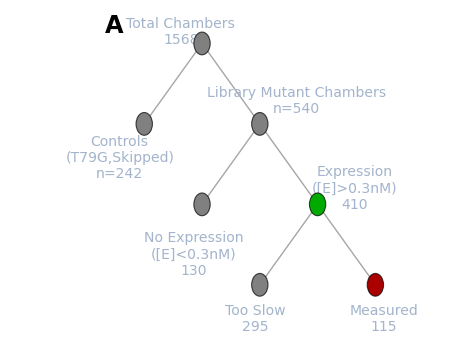

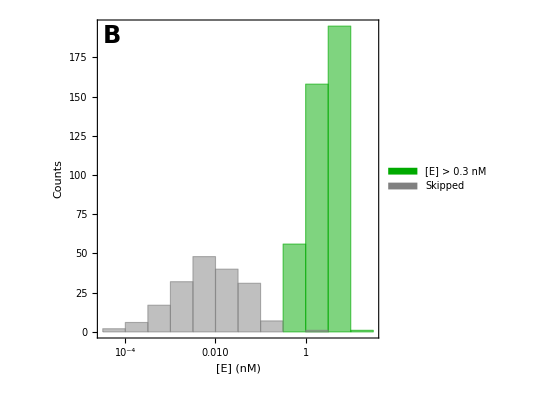

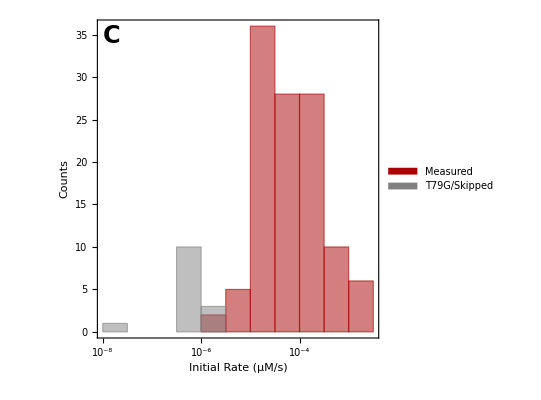

{{W102V,{0.152009,0.200277}},{K162V,{0.761319,1.14544}},{K162V,{1.17173,0.745837}},{K162V,{1.34627,2.24399}},{N100A,{0.283007,0.236247}}}

0.0142803

{{W102V,{0.152009,0.200277}},{K162V,{0.761319,1.14544}},{K162V,{1.17173,0.745837}},{K162V,{1.34627,2.24399}},{N100A,{0.283007,0.236247}}}

{{W102V,{160479.,192186.}},{K162V,{2288.01,2345.07}},{K162V,{2502.82,2372.65}},{K162V,{2407.04,2573.2}},{N100A,{337166.,314890.}}}

{{W102V,{0.947221,1.0421}},{K162V,{332.743,488.447}},{K162V,{468.163,314.348}},{K162V,{559.304,872.062}},{N100A,{0.839369,0.750251}}}

-Graphics- | -Graphics- | -Graphics-
-Graphics- |  | 
Experimental Summary. A) Counts of local limit of quantification control chambers (skipped and catalytically unresolvable mutants), library and known active site mutant chambers (library mutants), chambers which expressed >0.3 nM, and measured and chambers that were not sufficiently above the local limit of quantification (too slow). B) Distribution of enzyme concentrations in chambers with [E]>0.3 nM compared to the measured expression in the Skipped chambers. C) Distribution of rates measured in the chambers sufficiently above the local limit of quantification (Measured) compared to the rates measured in the control chambers, at the highest substrate concentration. D) Correlation between k_cat/K_M replicate measurements for measured library mutants. |  |

/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/temporary_PDF_0000.pdf

```mathematica
Dynamic[n]

start=AbsoluteTime[];

dataset=ds5[Select[#ExpIndex==1&&#AssayType==1&]];

Length[dataset]

Print["Fitting standard curves..."]
ProgressIndicator[Dynamic[count],{1,1568}]

addStandardCurveFits=Dataset@Table[Association[{"Indices"->Normal[dataset[count,"Indices"]],"StdCurveFitObject"->fitStdCurveNew[ToExpression[Normal[dataset[count,"SC_Concentrations"]]],If[NumberQ[ToExpression[Normal[dataset[count,"SC_Median_Chamber"]]][[1]]],ToExpression[Normal[dataset[count,"SC_Median_Chamber"]]],Missing[]]]}],{count,1,1568}];

addStandardCurveFits2=addStandardCurveFits[All,Append[#,{"StdCurveSlope"->If[MissingQ[#StdCurveFitObject],Missing["Nonexistent"],#StdCurveFitObject["BestFitParameters"][[2]]],"StdCurveIntercept"->If[MissingQ[#StdCurveFitObject],Missing["Nonexistent"],#StdCurveFitObject["BestFitParameters"][[1]]],"StdCurveRSquared"->If[MissingQ[#StdCurveFitObject],Missing["Nonexistent"],#StdCurveFitObject["RSquared"]]}]&];

withStdCurveFits=Dataset[JoinAcross[Normal[ds4],Normal[addStandardCurveFits2],{"Indices"},"Left"]];
Print["Adding standard curve plots..."]
ProgressIndicator[Dynamic[count2],{1,1568}]

withStdCurveFitsTemp=withStdCurveFits[Select[#ExpIndex==1&&#AssayType==1&]];

addStandardCurvePlots=Table[Association[{"Indices"->Normal[withStdCurveFitsTemp[count2,"Indices"]],"StandardCurvePlot"->makeStdCurvePlotNew[withStdCurveFitsTemp[count2,"StdCurveSlope"],withStdCurveFitsTemp[count2,"StdCurveIntercept"],ToExpression[withStdCurveFitsTemp[count2,"SC_Concentrations"]],ToExpression[withStdCurveFitsTemp[count2,"SC_Median_Chamber"]]]}],{count2,1,1568}];

AbsoluteTime[]-start

withStdCurvePlot=Dataset[JoinAcross[Normal[withStdCurveFits],addStandardCurvePlots,{"Indices"},"Left"]];

AbsoluteTime[]-start
withProgressCurves=withStdCurvePlot[All,Append[#,"TurnoverTimepoints(uM)"->convertTouM[ToExpression[#MedianIntensities],#StdCurveSlope,#StdCurveIntercept]]&];
cmupData=SemanticImport[cmupAggregatePath];
cmupParams=cmupData[All,{"MutantID","kcatNormMedian","KMMedian","kcat/KMNormMedianLimit","kcat/KMAggLimit"}];
cmupGrouped=cmupParams[GroupBy["MutantID"]];
wtkcatKm=cmupGrouped["WT",1,"kcat/KMNormMedianLimit"]
wtkcat=cmupGrouped["WT",1,"kcatNormMedian"]
wtKm=cmupGrouped["WT",1,"KMMedian"]
cmupParamsForCalc=Dataset[Table[Association[{"MutantID"->cmupGrouped[mutant,1,"MutantID"],"kcat"->If[cmupGrouped[mutant,1,"kcat/KMAggLimit"]==0,Select[Normal[cmupGrouped[mutant,All,"kcatNormMedian"]],NumberQ[#]&][[1]],Median[Select[Normal[cmupGrouped[mutant,All,"kcat/KMNormMedianLimit"]],#>0&]]/wtkcatKm*wtkcat],"Km"->If[cmupGrouped[mutant,1,"kcat/KMAggLimit"]==0,Select[Normal[cmupGrouped[mutant,All,"KMMedian"]],NumberQ[#]&][[1]],wtKm],"kobs"->Select[Normal[cmupGrouped[mutant,All,"kcat/KMNormMedianLimit"]],NumberQ[#]&][[1]],"Limit"->cmupGrouped[mutant,1,"kcat/KMAggLimit"]}],{mutant,1,Length[cmupGrouped]}]][GroupBy["MutantID"]]
obsProgressCurve[times_,concentrations_]:=Module[{temp1,fullProgressCurve},

If[MissingQ[concentrations],Missing[],

temp1={Normal[times],Normal[concentrations]};

fullProgressCurve=Sort[Table[{temp1[[1,n]],temp1[[2,n]]},{n,1,Length[temp1[[1]]]}],#1[[1]]<#2[[1]]&]]

]

progressCurveLambertW[kcat_?NumberQ,KM_,enz_,substrate_,time_]:=(substrate-KM*LambertW[substrate/KM*Exp[(substrate-kcat*enz*time)/KM]])

maxExponent=Round[Log[10,$MaxMachineNumber]]+1;

fitRateSuperposition[mutant_,progresscurve_,enzymeconc_,mecmupConc_]:=Module[{},

If[MissingQ[progresscurve],Table[Missing[],{7}],

chamberTestPC2=progresscurve;

econc=enzymeconc/1000.0;

cmupkcat=cmupParamsForCalc[mutant,1,"kcat"];
cmupKm=cmupParamsForCalc[mutant,1,"Km"];

limitQ=cmupParamsForCalc[mutant,1,"Limit"];

baseline=Min[chamberTestPC2[[All,2]]];

(* if we don't have measurements for kcat and Km then can't fit the superposition function - in these cases defaulting to a fit using the points at t>2500s *)
basicFit=LinearModelFit[Select[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],#[[1]]≥2500.0&],x,x];

basicFitRate=basicFit[[1,2,2]];

basicFitIntercept=basicFit[[1,2,1]];

pcBaselineCorrected=Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}];

p=Graphics[{EdgeForm[{Black,Thickness[0.125]}],FaceForm[Directive[GrayLevel[0.5],Opacity[0.7]]],Disk[],Opacity[0.1]}];

(* also modifying to fit only rates - the testing above is fitting the MecMUP kcat/KM *)

Which[NumberQ[cmupkcat]&&limitQ≠-1,

fit=Quiet[NMinimize[{Sum[((chamberTestPC2[[n,2]]-baseline)-(progressCurveLambertW[cmupkcat,cmupKm,econc,cmup,chamberTestPC2[[n,1]]]+(rate)*chamberTestPC2[[n,1]]))^2,{n,1,Length[chamberTestPC2]}],rate>-0.05&&rate<0.05&&cmup>0.0&&cmup<(mecmupConc/1000.0)},{cmup,rate}]];

lastFivePointsForFlag=Table[{chamberTestPC2[[n,1]],progressCurveLambertW[cmupkcat,cmupKm,econc,mecmupConc/1000.0,chamberTestPC2[[n,1]]]},{n,1,Length[chamberTestPC2]}];

flagFit=LinearModelFit[Select[lastFivePointsForFlag,#[[1]]≥2500.0&],x,x];

{fit[[2,1,2]],fit[[2,2,2]],Show[Plot[progressCurveLambertW[cmupkcat,cmupKm,econc,fit[[2,1,2]],t]+fit[[2,2,2]]*t,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.2,If[Max[chamberTestPC2[[All,2]]]>5.0,Max[chamberTestPC2[[All,2]]]+Abs[Max[chamberTestPC2[[All,2]]]]*0.5,5.5]},AspectRatio->0.8,PlotStyle->Gray],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotMarkers->{p,0.05}],Plot[progressCurveLambertW[cmupkcat,cmupKm,econc,fit[[2,1,2]],t],{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Directive[Gray,Dashed]],ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[18,Black,FontFamily->"Arial"],Epilog->Inset[mutant<>"\n"<>ToString[NumberForm[Round[fit[[2,2,2]],0.0000001],ScientificNotationThreshold->{-maxExponent,maxExponent}]]<>"μM/s"<>"\n[cMUP]="<>ToString[Round[fit[[2,1,2]],0.01]]<>" μM",Scaled[{0.80,0.3}]]],Abs[flagFit[[1,2,2]]],(fit[[2,2,2]]-trueBackgroundRate)/Abs[flagFit[[1,2,2]]],Show[Plot[progressCurveLambertW[cmupkcat,cmupKm,econc,fit[[2,1,2]],t]+fit[[2,2,2]]*t,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Darker[Red]],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotStyle->Directive[PointSize[0.02],Darker[Red],Opacity[0.5]]],PlotRange->All,AspectRatio->0.8,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[Black,18,FontFamily->"Arial"]],pcBaselineCorrected},

NumberQ[cmupkcat]&&limitQ==-1,

lastFivePointsForFlag=Table[{chamberTestPC2[[n,1]],progressCurveLambertW[cmupkcat,cmupKm,econc,mecmupConc/1000.0,chamberTestPC2[[n,1]]]},{n,1,Length[chamberTestPC2]}];

flagFit=LinearModelFit[Select[lastFivePointsForFlag,#[[1]]≥2500.0&],x,x];

{Missing[],basicFitRate,Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{If[(Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1)>0,0,Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1],If[Max[chamberTestPC2[[All,2]]]>5.0,Max[chamberTestPC2[[All,2]]]+Abs[Max[chamberTestPC2[[All,2]]]]*0.5,5.5]},AspectRatio->0.8,PlotStyle->Gray],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotMarkers->{p,0.05}],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[18,Black,FontFamily->"Arial"],Epilog->Inset[mutant<>"\n"<>ToString[NumberForm[Round[basicFitRate,0.0000001],ScientificNotationThreshold->{-maxExponent,maxExponent}]]<>"μM/s",Scaled[{0.80,0.2}]]],Abs[flagFit[[1,2,2]]],(fit[[2,2,2]]-trueBackgroundRate)/Abs[flagFit[[1,2,2]]],Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Darker[Red]],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotStyle->Directive[PointSize[0.02],Darker[Red],Opacity[0.5]]],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[Black,18,FontFamily->"Arial"]],pcBaselineCorrected},

NumberQ[cmupkcat]==False,

{Missing[],basicFitRate,Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{If[(Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1)>0,0,Min[chamberTestPC2[[All,2]]]-Abs[Max[chamberTestPC2[[All,2]]]]*0.1],If[Max[chamberTestPC2[[All,2]]]>5.0,Max[chamberTestPC2[[All,2]]]+Abs[Max[chamberTestPC2[[All,2]]]]*0.5,5.5]},AspectRatio->0.8,PlotStyle->Gray],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotMarkers->{p,0.05}],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[18,Black,FontFamily->"Arial"],Epilog->Inset[mutant<>"\n"<>ToString[NumberForm[Round[basicFitRate,0.0000001],ScientificNotationThreshold->{-maxExponent,maxExponent}]]<>"μM/s",Scaled[{0.80,0.2}]]],Missing[],Missing[],Show[Plot[basicFitRate*t+basicFitIntercept,{t,0,Max[chamberTestPC2[[All,1]]]*1.2},PlotRange->{0,All},PlotStyle->Darker[Red]],ListPlot[Table[{chamberTestPC2[[n,1]],chamberTestPC2[[n,2]]-baseline},{n,1,Length[chamberTestPC2]}],PlotRange->{-2,6},PlotStyle->Directive[PointSize[0.02],Darker[Red],Opacity[0.5]]],PlotRange->All,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"Time (s)","Product (μM)"},FrameStyle->Directive[Black,18,FontFamily->"Arial"]],pcBaselineCorrected}


]]

]
withProgressCurves2=withProgressCurves[All,Append[#,{"ProgressCurve"->obsProgressCurve[ToExpression[#Times],#["TurnoverTimepoints(uM)"]],"EnzymeConc"->(#eGFPSummedI/#eGFPSlope)}]&];
itr=0;

Dynamic[itr]

optDataPoints2=withProgressCurves2[All,Append[#,itrNew=itr+1;itr=itrNew;out=Quiet[fitRateSuperposition[#MutantID,#ProgressCurve,#EnzymeConc,#SubstrateConc]];{"OptLinFitSlope"->out[[2]],"OptLinFitSlopeMinusTrueBackground"->out[[2]]-trueBackgroundRate,"ContaminantConc"->out[[1]],"FitPlot"->out[[3]],"ContaminantRate"->out[[4]],"ContaminantRatio"->out[[5]],"BackgroundFitPlot"->out[[6]],"ProgressCurveBaselineCorrected"->out[[7]]}]&];
indices=Normal[optDataPoints2[Select[#ExpIndex==1&]][All,"Indices"]];
Length[indices]
Dynamic[ind]

nearestLocalBG=Table[Association["Indices"->indices[[ind]],"NearestLocalBackgroundChambers"->findNearestBackgroundChambers[optDataPoints2,indices[[ind]]]],{ind,1,Length[indices]}];
(*nearestBackgroundChambers=Import["/Users/craig/Dropbox/HTMEK_processing/current/per-experiment_QC/nearestLocalBackgroundChambers.wxf"];*)

(*nearestBackgroundChambers=Import["/Users/craig/Dropbox/HTMEK_processing/current/per-experiment_QC/nearestLocalBackgroundChambers_SlowestChip.wxf"];*)

withNearestChambers=Dataset[JoinAcross[Normal[optDataPoints2],nearestLocalBG,"Indices","Left"]];
start=AbsoluteTime[];

count2=0;
Dynamic[count]

withPCs2=withNearestChambers[All,Quiet[Append[#,(Clear[forSelect];count=count2+1;forSelect=#NearestLocalBackgroundChambers;sconc=#SubstrateConc;
expIndex=#ExpIndex;
indices=#Indices;count2=count;

If[MissingQ[#ProgressCurve],"ProgressCurveOptFit2"->Missing[],

bgProgressCurves=Normal[optDataPoints2[Select[MemberQ[forSelect,#Indices]&&#ExpIndex==expIndex&]][All,"FitPlot"]];

{"ProgressCurveOptFit2"->If[Length[bgProgressCurves]>0,Show[DeleteCases[DeleteCases[{#FitPlot,Normal[optDataPoints2[Select[MemberQ[forSelect,#Indices]&&#SubstrateConc==sconc&&#ExpIndex==expIndex&]][All,"BackgroundFitPlot"]]},Missing["Nonexistent"],Infinity],Missing[],Infinity],AspectRatio->0.8,ImageSize->400,AspectRatio->0.6,ImagePadding->{{75,2},{60,8}},Epilog->Inset[Style[ToString[Round[sconc]]<>" μM",16,Black,FontFamily->"Arial"],Scaled[{0.18,0.85}]]],Missing["Nonexistent"]]}]

)]&]];


(*{"ProgressCurveOptFit2"->If[Length[bgProgressCurves]>0,Show[DeleteCases[DeleteCases[{#FitPlot,Normal[optDataPoints2[Select[MemberQ[forSelect,#Indices]&&#SubstrateConc==sconc&&#ExpIndex==expIndex&]][All,"BackgroundFitPlot"]]},Missing["Nonexistent"],Infinity],Missing[]],AspectRatio->0.8,ImageSize->400,AspectRatio->0.6,ImagePadding->{{75,2},{60,8}},Epilog->Inset[Style[ToString[Round[sconc]]<>" μM",16,Black,FontFamily->"Arial"],Scaled[{0.18,0.85}]]],Missing["Nonexistent"]]}*)

AbsoluteTime[]-start
Dynamic[n]
Dynamic[column]

(*datasetIN=withPCs;*)

datasetIN=withPCs2;

inhibitorconcentrations=Normal[datasetIN[Select[#Indices=={1,1}&],"InhibitorConcentrations"]];
substrateconcentrations=Normal[datasetIN[Select[#Indices=={1,1}&],"SubstrateConc"]]
type=Normal[datasetIN[Select[#Indices=={1,1}&],"AssayType"]];

exptIndices=Normal[datasetIN[Select[#Indices=={1,1}&],"ExpIndex"]];

dataset2=datasetIN;

start=AbsoluteTime[];

interpolations=Flatten[Table[Association[{"x"->column,"ExpIndex"->exptIndices[[n]],"AssayType"->type[[n]],"Interpolation"->interpolateDeadMutantsPerColumn[mutantList,exptIndices[[n]],column,dataset2,"OptLinFitSlopeMinusTrueBackground"],"MutantsUsedForLocalBG"->mutantList}],{n,1,Length[substrateconcentrations]},{column,1,28}],1];

dataset3=Dataset[JoinAcross[Normal[dataset2],interpolations,{"x","ExpIndex","AssayType"},"Left"]];

AbsoluteTime[]-start
start=AbsoluteTime[];

dataset=dataset3;

temp=Values[Normal[dataset[All,{"Indices","ExpIndex","OptLinFitSlopeMinusTrueBackground","MutantID","Interpolation"}]]];

localBGs=Table[Association[{"Indices"->temp[[n,1]],"ExpIndex"->temp[[n,2]],"LocalBackgroundRatio"->If[MissingQ[temp[[n,3]]],Missing["Nonexistent"],(temp[[n,3]])/(temp[[n,5,temp[[n,1,2]]]])]}],{n,1,Length[temp]}];

withlocalBG=Dataset[JoinAcross[Normal[dataset],localBGs,{"Indices","ExpIndex"},"Left"]];

AbsoluteTime[]-start

Dynamic[n]

scaleEachAssay=0;

eGFPslope=withlocalBG[1,"eGFPSlope"];

start=AbsoluteTime[];

dataset2=withlocalBG;


boundingMutants={"WT","T79S"};

rateKey="OptLinFitSlopeMinusTrueBackground";

temp=dataset2[Select[#ExpIndex==whichExpt&],{"Indices","ExpIndex",rateKey,"MutantID","Interpolation"}];

upperBound=Mean[Select[Values[Normal[dataset2[Select[#MutantID==boundingMutants[[1]]&&#ExpIndex==whichExpt&&#eGFPSummedI>EcutoffForBG*eGFPslope&],{rateKey}]]],NumberQ[#[[1]]]==True&]][[1]];

lowerBound=Mean[Select[Values[Normal[dataset2[Select[#MutantID==boundingMutants[[2]]&&#ExpIndex==whichExpt&&#eGFPSummedI>EcutoffForBG*eGFPslope&],{rateKey}]]],NumberQ[#[[1]]]==True&]][[1]];

allinColumn=Join@@Flatten[Table[AssociationThread[Table[{column,row},{row,1,56}],Sort[Values[Normal[dataset2[Select[#Indices[[1]]==column&&#ExpIndex==whichExpt&],{"Indices",rateKey,"MutantID"}]]],#1[[1,2]]<#2[[1,2]]&]],{column,1,28}],2];

temp2=temp[All,Append[#,{"Indices"->Normal[#[[1]]],"MaxLocalBackgroundPlot"->generateLocalBGPlot[Normal[#["Indices"]],Normal[#["ExpIndex"]],Normal[#["Interpolation"]]]}]&];

withlocalBGPlots=Dataset[JoinAcross[Normal[dataset2],Normal[temp2],{"Indices"},"Left"]];

CloseKernels[];

LaunchKernels[4];

dataset=withlocalBGPlots;

len=1568;

numKernels=Length[Kernels[]]

chunksize=Round[len/numKernels];
firstChunks =Table[{(chunksize*(n-1))+1, n*chunksize}, {n, numKernels-1}];
intervals=Append[firstChunks, {(chunksize*(numKernels-1))+1, len}];

toCalculate=dataset[GroupBy["Indices"]];

chunked = toCalculate[[#[[1]];;#[[2]]]]&/@intervals;

flattened=Table[chunked[[n]][Catenate],{n,1,Length[chunked]}];

addedMMcalc=Join@@ParallelMap[Quiet[fitMichaelisMenten[#,"OptLinFitSlopeMinusTrueBackground","optlin",eGFPslope,scaleEachAssay]]&,flattened];

AbsoluteTime[]-start

CloseKernels[]
Dynamic[n]

grouped=addedMMcalc[GroupBy["Indices"]];

indicesOut=Values[#]&/@Values[Normal[grouped[All,1,{"MutantID","Indices","fit_mm_kcat","fit_mm_KM"}]]];

addkcatoverkm=Table[Association[{"MutantID"->indicesOut[[n,1]],"Indices"->indicesOut[[n,2]],"fit_mm_kcatoverKM_MMfit"->If[MissingQ[indicesOut[[n,3]]],Missing["Nonexistent"],indicesOut[[n,3]]/(indicesOut[[n,4]]*10^-6)]}],{n,1,1568}];

addedkcatoverkm=Dataset[JoinAcross[Normal[addedMMcalc],addkcatoverkm,"Indices","Left"]]//Quiet;


grouped=addedkcatoverkm[GroupBy["Indices"]];

indicesOut=Values[#]&/@Values[Normal[grouped[All,1,{"MutantID","Indices"}]]];

pGFP=Graphics[{EdgeForm[{Black,Thickness[0.125]}],FaceForm[Directive[Darker[Green],Opacity[0.7]]],Disk[],Opacity[0.1]}];

addedeGFPIntensityPlot=Table[Association[{"MutantID"->indicesOut[[n,1]],"Indices"->indicesOut[[n,2]],"eGFPIntensityPlot"->If[egfpSameFlag==0,ListPlot[Normal[grouped[n,All,"eGFPSummedI"]]/10^6,PlotRange->{0,Max[Normal[grouped[n,All,"eGFPSummedI"]]/10^6]*1.5},Frame->True,Axes->False,PlotMarkers->{pGFP,0.05},FrameStyle->Directive[20,Black,FontFamily->"Arial"],FrameLabel->{"Assay Number","eGFP Intensity (×10^6)"},ImagePadding->{{75,2},{65,5}},AspectRatio->0.8,ImageSize->400],ListPlot[{{1,Normal[grouped[n,1,"eGFPSummedI"]]/10^6}},PlotRange->{{0,Length[Normal[grouped[n,All,"eGFPSummedI"]]]},{0,Max[Normal[grouped[n,All,"eGFPSummedI"]]/10^6]*1.5}},Frame->True,Axes->False,PlotMarkers->{pGFP,0.05},GridLines->{None,{Normal[grouped[n,1,"eGFPSummedI"]]/10^6}},GridLinesStyle->Directive[Dashed,Darker[Green]],FrameStyle->Directive[20,Black,FontFamily->"Arial"],FrameLabel->{"Assay Number","eGFP Intensity (×10^6)"},ImagePadding->{{75,2},{65,5}},AspectRatio->0.8,ImageSize->400,FrameTicks->{{If[IntegerQ[#],#,N[#]]&/@FindDivisions[{0,Max[Normal[grouped[n,All,"eGFPSummedI"]]/10^6]},5],None},{If[IntegerQ[#],#,N[#]]&/@FindDivisions[{0,Length[Normal[grouped[n,All,"eGFPSummedI"]]]},Round[Length[Normal[grouped[n,All,"eGFPSummedI"]]]/2]],None}},Epilog->Inset[Style["eGFP measured\nbefore 1st assay only",14,Darker[Green]],Scaled[{0.7,0.3}]]]]}],{n,1,1568}];

addedeGFPIntensityPlotDataset=Dataset[JoinAcross[JoinAcross[Normal[addedkcatoverkm],addedeGFPIntensityPlot,"Indices","Left"],Normal[wxfForImageStamps[Select[#ExpIndex==1&],{"Indices","eGFPPostSDSImage"}]],"Indices","Left"]]//Quiet;

AbsoluteTime[]-start
normalizedDataset=Normal[addedeGFPIntensityPlotDataset];

replaced=Fold[Replace[#1,#2,Infinity]&,normalizedDataset,{_FittedModel->"NaN",_Graphics->"NaN",_Image->"NaN",_NonlinearModelFit->"NaN",_Times->"NaN",_Overlay->"NaN",_ReplaceAll->"NaN"}];

headers=Keys[replaced[[1]]];

(*values=Map[replaceBracketsBack,Values[replaced],{2}];*)

values=Values[replaced];

datasetForExport=Prepend[values,headers];

Export[StringJoin["~/Desktop/",addedkcatoverkm[1,"GlobalExperimentIndex"],"_MecMUP_LinComb.csv.bz2"],datasetForExport,"Data"];

(* summary table *)

fixLogPlots[gr_]:=gr/.f:(Charting`ScaledTicks|Charting`ScaledFrameTicks)[{Log,Exp}]:>(Part[#,;;, ;;3]&@*f);

p2=Graphics[{EdgeForm[{Black,Thickness[0.125]}],FaceForm[Directive[Gray,Opacity[0.7]]],Disk[],Opacity[0.1]}];

expressed=addedeGFPIntensityPlotDataset[Select[#ExpIndex==1&&#ManualGFPFlag==0&&#EnzymeConc>0.3&]];

Length[expressed]

skipped=addedeGFPIntensityPlotDataset[Select[#ExpIndex==1&&#ManualGFPFlag==0&&#MutantID=="Skipped"&]];

allLibraryChambers=addedeGFPIntensityPlotDataset[Select[#ExpIndex==1&&#MutantID≠"Skipped"&&#MutantID≠"T79G"&]];

expressedLibrary=allLibraryChambers[Select[#EnzymeConc>0.3&&#ManualGFPFlag==0&]];

Length[allLibraryChambers]
Length[expressedLibrary]

tooSlow=addedeGFPIntensityPlotDataset[Select[#ExpIndex==whichExpt&&#LocalBackgroundRatio≤5.0&&MemberQ[Normal[expressedLibrary[All,"Indices"]],#Indices]&]];

Length[tooSlow]

measured=addedeGFPIntensityPlotDataset[Select[#ExpIndex==whichExpt&&#LocalBackgroundRatio>5.0&&MemberQ[Normal[expressedLibrary[All,"Indices"]],#Indices]&]];

Length[measured]

countTree=TreePlot[{1->2,1->3,3->4,3->5,5->6,5->7},VertexSize->Medium,VertexCoordinates->{{0,0},{-1,-1},{1,-1},{0,-2},{2,-2},{1,-3},{3,-3}},EdgeStyle->Gray,Epilog->Inset[Style["A",24,Bold],Scaled[{0.0,1.0}]],VertexLabels->{1->Placed[Style["Total Chambers\n1568",14],{-0.8,1}],2->Placed[Style["Controls\n(T79G,Skipped)\nStyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[skipped]],14],{-1,-1}],3->Placed[Style["Library Mutant Chambers\nStyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[allLibraryChambers]],14],{2.75,1.5}],4->Placed[Style["No Expression\n([E]<0.3nM)\n"<>ToString[Length[allLibraryChambers]-Length[expressedLibrary]],14],{0,-1.7}],5->Placed[Style["Expression\n([E]>0.3nM)\n"<>ToString[Length[expressedLibrary]],14],{2.75,1.2}],7->Placed[Style["Measured\n"<>ToString[Length[measured]],14],{1,-1}],6->Placed[Style["Too Slow\n"<>ToString[Length[tooSlow]],14],{0.25,-1}]},ImageSize->450,VertexStyle->
Join[
{1->Gray}, 
#->Gray&/@{1,2,3,4,6},
#->Darker[Green]&/@{5},
#->Darker[Red]&/@{7}
]]

eConcHist=fixLogPlots@Histogram[{Normal[expressedLibrary[All,"EnzymeConc"]],Normal[skipped[All,"EnzymeConc"]]},"Log",ChartStyle->{Darker[Green],Gray},Frame->True,Axes->False,PlotRange->All,FrameStyle->Directive[20,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->400,FrameLabel->{Style["[E] (nM)",SingleLetterItalics->False],Style["Counts",SingleLetterItalics->False]},Epilog->{Inset[SwatchLegend[{Darker[Green],Gray},Style[#,16]&/@{"[E] > 0.3 nM","Skipped"}],Scaled[{0.25,0.9}]],Inset[Style["B",24,Bold],Scaled[{0.05,0.95}]]}]

rateHist=fixLogPlots@Histogram[{Normal[measured[All,"OptLinFitSlopeMinusTrueBackground"]],Normal[skipped[All,"OptLinFitSlopeMinusTrueBackground"]]},"Log",ChartStyle->{Darker[Red],Gray},Frame->True,Axes->False,PlotRange->All,FrameStyle->Directive[20,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->400,FrameLabel->{Style["Initial Rate (μM/s)",SingleLetterItalics->False],Style["Counts",SingleLetterItalics->False]},Epilog->{Inset[SwatchLegend[{Darker[Red],Gray},Style[#,16]&/@{"Measured","T79G/Skipped"}],Scaled[{0.8,0.9}]],Inset[Style["C",24,Bold],Scaled[{0.05,0.95}]]}]

measured2=measured;

measured3=measured2[All,{"MutantID","fit_mm_kcat"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured3[n,1,"MutantID"],#}&/@Partition[Normal[measured3[n,All,"fit_mm_kcat"]],2],{n,1,Length[measured3]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]]

measured2=measured[All,{"MutantID","fit_mm_kcat","fit_mm_KM","fit_mm_kcatoverKM_MMfit"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured2[n,1,"MutantID"],#}&/@Partition[Normal[measured2[n,All,"fit_mm_kcat"]],2],{n,1,Length[measured2]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]];

rmse=Sqrt[Mean[Table[(Log[10,pairs[[n,2,1]]]-Log[10,pairs[[n,2,2]]])^2,{n,1,Length[pairs]}]]];

pearsonR2=Correlation[Log[10,pairs[[All,2,1]]],Log[10,pairs[[All,2,2]]]]^2;

(*kcatplot=fixLogPlots@Show[ListLogLogPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[pairs[[n,2]],pairs[[n,1]]],pairs[[n,2]]],{n,1,Length[pairs]}],PlotRange->{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}},Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->500,PlotMarkers->{p2,0.02},FrameLabel->{"SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"] (rep.1) (/s)","SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"] (rep.2) (/s)"}],LogLogPlot[{x,x/2,x*2},{x,0.0001,10000},PlotStyle->Directive[Gray,Dashed]],ImagePadding->100];*)

kcatplot=Show[ListPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[Log[10,pairs[[n,2]]],pairs[[n,1]]],Log[10,pairs[[n,2]]]],{n,1,Length[pairs]}],PlotRange->Log[10,{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}}],Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->475,PlotMarkers->{p2,0.02},FrameLabel->{"Log10(SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]) (rep.1) (/s)","Log10(SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]) (rep.2) (/s)"},Epilog->{Inset[Style["SuperscriptBox[StyleBox[\"R\",FontSlant->\"Italic\"], \"2\"]="<>ToString[Round[pearsonR2,0.01]],14],Scaled[{0.2,0.9}]],Inset[Style["RMSE="<>ToString[Round[rmse,0.01]],14],Scaled[{0.2,0.8}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[pairs]],14],Scaled[{0.2,0.7}]],Inset[Style["D",24,Bold],Scaled[{0.05,0.95}]]}],Plot[{x,x-0.301,x+0.301},{x,-5,10},PlotStyle->Directive[Gray,Dashed]],ImagePadding->{{100,20},{100,50}}];

measured2=measured[All,{"MutantID","fit_mm_KM"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured2[n,1,"MutantID"],#}&/@Partition[Normal[measured2[n,All,"fit_mm_KM"]],2],{n,1,Length[measured2]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]];

rmse=Sqrt[Mean[Table[(Log[10,pairs[[n,2,1]]]-Log[10,pairs[[n,2,2]]])^2,{n,1,Length[pairs]}]]];

pearsonR2=Correlation[Log[10,pairs[[All,2,1]]],Log[10,pairs[[All,2,2]]]]^2;

KmPlot=Show[ListPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[Log[10,pairs[[n,2]]],pairs[[n,1]]],Log[10,pairs[[n,2]]]],{n,1,Length[pairs]}],PlotRange->Log[10,{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}}],Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->475,PlotMarkers->{p2,0.02},FrameLabel->{Style["Log[10,SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.1) (/s)",SingleLetterItalics->False],Style["Log[10,SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.2) (/s)",SingleLetterItalics->False]},Epilog->{Inset[Style["SuperscriptBox[StyleBox[\"R\",FontSlant->\"Italic\"], \"2\"]="<>ToString[Round[pearsonR2,0.01]],14],Scaled[{0.2,0.9}]],Inset[Style["RMSE="<>ToString[Round[rmse,0.01]],14],Scaled[{0.2,0.8}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[pairs]],14],Scaled[{0.2,0.7}]],Inset[Style["E",24,Bold],Scaled[{0.05,0.95}]]}],Plot[{x,x-0.301,x+0.301},{x,-5,10},PlotStyle->Directive[Gray,Dashed]],Plot[10,{x,-5,Log[10,0.5]},Filling->-5,FillingStyle->Directive[LightPink,Opacity[0.5]],PlotStyle->Directive[LightPink,Opacity[0.8]]],ImagePadding->{{100,20},{100,50}}];

measured2=measured[All,{"MutantID","fit_mm_kcatoverKM_MMfit"}][GroupBy["MutantID"]];

pairs=Flatten[Table[{measured2[n,1,"MutantID"],#}&/@Partition[Normal[measured2[n,All,"fit_mm_kcatoverKM_MMfit"]],2],{n,1,Length[measured2]}],1];
pairs[[1;;5]]

Min[Flatten[pairs[[All,2]]]];

rmse=Sqrt[Mean[Table[(Log[10,pairs[[n,2,1]]]-Log[10,pairs[[n,2,2]]])^2,{n,1,Length[pairs]}]]];

pearsonR2=Correlation[Log[10,pairs[[All,2,1]]],Log[10,pairs[[All,2,2]]]]^2;

kcatKMplot=Show[ListPlot[Table[If[pairs[[n,2,2]]/pairs[[n,2,1]]>3||pairs[[n,2,2]]/pairs[[n,2,1]]<(1/3),Callout[Log[10,pairs[[n,2]]],pairs[[n,1]]],Log[10,pairs[[n,2]]]],{n,1,Length[pairs]}],PlotRange->Log[10,{{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5},{Min[Flatten[pairs[[All,2]]]]/5,Max[Flatten[pairs[[All,2]]]]*5}}],Frame->True,Axes->False,FrameStyle->Directive[24,Black,FontFamily->"Arial"],AspectRatio->1,ImageSize->475,PlotMarkers->{p2,0.02},FrameLabel->{Style["Log[10,SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]/SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.1) (/M /s)",SingleLetterItalics->False],Style["Log[10,SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]/SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"]] (rep.2) (/M /s)",SingleLetterItalics->False]},Epilog->{Inset[Style["SuperscriptBox[StyleBox[\"R\",FontSlant->\"Italic\"], \"2\"]="<>ToString[Round[pearsonR2,0.01]],14],Scaled[{0.2,0.9}]],Inset[Style["RMSE="<>ToString[Round[rmse,0.01]],14],Scaled[{0.2,0.8}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"]="<>ToString[Length[pairs]],14],Scaled[{0.2,0.7}]],Inset[Style["F",24,Bold],Scaled[{0.05,0.95}]]}],Plot[{x,x-0.301,x+0.301},{x,-5,10},PlotStyle->Directive[Gray,Dashed]],ImagePadding->{{100,20},{100,50}}];

(*Grid[{{countTree,kcatplot},{eConcHist,KmPlot},{rateHist,kcatKMplot}}]*)

summaryGrid=Grid[{{countTree,eConcHist,rateHist},{kcatKMplot},{Style["Experimental Summary. A) Counts of local limit of quantification control chambers (skipped and catalytically unresolvable mutants), library and known active site mutant chambers (library mutants), chambers which expressed >0.3 nM, and measured and chambers that were not sufficiently above the local limit of quantification (too slow). B) Distribution of enzyme concentrations in chambers with [E]>0.3 nM compared to the measured expression in the Skipped chambers. C) Distribution of rates measured in the chambers sufficiently above the local limit of quantification (Measured) compared to the rates measured in the control chambers, at the highest substrate concentration. D) Correlation between SubscriptBox[StyleBox[\"k\",FontSlant->\"Italic\"], \"cat\"]/SubscriptBox[StyleBox[\"K\",FontSlant->\"Italic\"], \"M\"] replicate measurements for measured library mutants.",18,FontFamily->"Arial",TextAlignment->Left,SingleLetterItalics->False],SpanFromLeft}}]

Export[StringJoin["/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/temporary_PDF_","0000",".pdf"],summaryGrid,"AllowRasterization"->False]
```

```mathematica
dataset=addedeGFPIntensityPlotDataset;

indices=Sort[Normal[DeleteDuplicates[dataset[[All,"Indices"]]]]];

Do[

(* change 3rd argument to correspond to type of assay: cMUP, MeP, MecMUP, Inhibition *)
(* added 4th argument "unscaled" *)
out=makeGridMecMUP[dataset,indices[[n]],"MecMUP","unscaled"];

Export[StringJoin["/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/temporary_PDF_",StringPadLeft[ToString[n],4,"0"],".pdf"],out,"AllowRasterization"->False];

,{n,1,1568}];

session = StartExternalSession[<|"System"->"Python","Version"->"3.6", "SessionProlog"->{"import os", "from PyPDF2 import PdfFileMerger, PdfFileReader"}|>];

defineRoot = "root='/Users/craig/Dropbox/AP_enzymology/MITOMI/tempPDF/'";
getNames = "pdfs1=[os.path.join(root, dir) for dir in os.listdir(root) if '.pdf' in dir]";
getNames2="pdfs=sorted(pdfs1)";
createMerger = "merger = PdfFileMerger()";
executeMerge = "for pdf in pdfs: merger.append(PdfFileReader(pdf,'rb'))";
executeExport = StringJoin["merger.write('/Users/craig/Desktop/",Values[Normal[dataset[1,{"GlobalExperimentIndex"}]]][[1]],".pdf')"];
completionNotice = "print('PDF Concatenation Complete')";

ExternalEvaluate[session,{defineRoot, getNames,getNames2, createMerger, executeMerge, executeExport, completionNotice}];
```

ReplaceAll::reps: {1000.,Indeterminate} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$35094583={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$35094583).(Times[«3»]-Optimization`FindFit`y$35094583)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

Part::partw: Part 2 of NonlinearModelFit[{{500.,Indeterminate},{1000.,Indeterminate},{1500.,Indeterminate},{2000.,Indeterminate}},{(substrate Vmax)/(KM+substrate),KM>0.5&&Vmax>0},{Vmax,KM},substrate][ParameterErrors] does not exist.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$35094637={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$35094637).(Times[«3»]-Optimization`FindFit`y$35094637)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM} = {1.,1.5}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={500.,1000.,1500.,2000.},Optimization`FindFit`y$35094686={Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 (Times[«3»]-Optimization`FindFit`y$35094686).(Times[«3»]-Optimization`FindFit`y$35094686)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0}}},{{{1,2,817},{{{Hold[Block[«2»]],Block},Automatic,None,1,Automatic},{}}}},{8,3,{},0},{904,MachinePrecision,{None,{Hold[Block[{Set[«2»],Set[«2»]},1/2 Dot[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.5}.

General::stop: Further output of NonlinearModelFit::grad will be suppressed during this calculation.

ReplaceAll::reps: {1000.,Indeterminate} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{{500.,Indeterminate},{1000.,Indeterminate},{1500.,Indeterminate},{2000.,Indeterminate}},{(substrate Vmax)/(KM+substrate),KM>0.5&&Vmax>0},{Vmax,KM},substrate][ParameterErrors] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

PDF Concatenation Complete